```mathematica
On[Assert]
ClearAll["`*"]
```

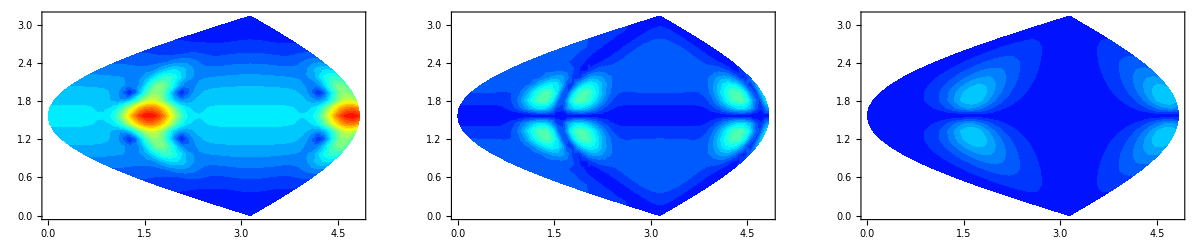

```mathematica
R={x,y,z};
u={0,0,1};
RcrossU=R×u;
RcrossU2=RcrossU.RcrossU;
ϵ=DiagonalMatrix[{1,1,ϵzz}];
ϵu=ϵ0 ϵzz;
ϵuni=ϵ0 ϵ;
rϵ=ϵu R.Inverse[ϵuni].R//Simplify;
gϵuni=ⅇ^(ⅈ k0 Sqrt[rϵ])/(4π Sqrt[rϵ])//Simplify;
rμ=R.R//Simplify;
gμuni=ⅇ^(ⅈ k0 Sqrt[rμ])/(4π Sqrt[rμ])//Simplify;
DelDel[f_]:=Table[D[f,R[[i]],R[[j]]],{i,1,3},{j,1,3}];
B=RcrossU⊗RcrossU/RcrossU2(ϵu/ϵ0 gϵuni-gμuni)+1/(ⅈ k0 RcrossU2)(IdentityMatrix[3]-u⊗u-2RcrossU⊗RcrossU/RcrossU2)(gϵuni Sqrt[rϵ]-gμuni Sqrt[rμ]);
GChen=-B+ϵu Inverse[ϵuni]gϵuni+1/(k0^2)DelDel[gϵuni];
rn=1;
sampleNumber=51;
ϵzzn=6;
margin=8/Sqrt@ϵzzn;
ϕn=Subdivide[Clip[π/2-margin,{0,2π}],Clip[π/2+margin,{0,2π}],sampleNumber];
θn=Subdivide[Clip[π/2-margin/2,{0,π}],Clip[π/2+margin/2,{0,π}],Round[sampleNumber/2]];
k0n=2π;
numeralize[g_]:=Parallelize@Outer[
Function[{θ,ϕ},
N[g/.{y->rn Cos[ϕ]Sin[θ],z->rn Sin[ϕ]Sin[θ],x->rn Cos[θ],ϵzz->ϵzzn,k0->k0n}]
],
θn,ϕn
];
Clear[dimKept];
dimKept=1;
GChen[[;;,2]]=0;
GChen[[;;,3]]=0;
jetColorFunction[x_]:=Blend[{Blue,Cyan,Yellow,Red},x]
plotGreen[g_]:=GraphicsGrid@Transpose@Module[{m},
m=Max[Abs[g]];
Table[
ListContourPlot[Flatten[MapIndexed[
{element,index}|->{(ϕn[[index[[2]]]]-π)Identity[Sin[θn[[index[[1]]]]]]+π,θn[[index[[1]]]],Abs[element[[i,j]]]},
g/m,{2}],1],
AspectRatio->1/2,
ContourLabels->Automatic,
PlotRange->{Automatic,Automatic,{0,1}},
Contours->Subdivide[0,1,21],
ColorFunction->jetColorFunction,
ContourStyle->None,
ColorFunctionScaling->False],
{i,1,3},{j,dimKept,dimKept}]
]
plotGreen@numeralize@GChen
```

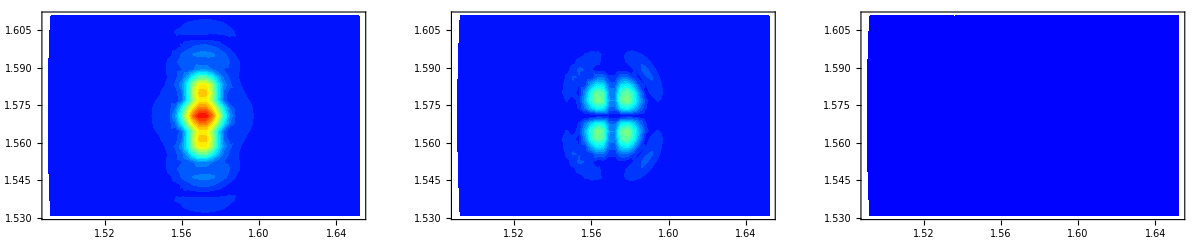

```mathematica
getData[ax_,ay_,az_]:=Module[{rawData,ex,ey,ez,g,linInd},
rawData=Import[FileNameJoin[{NotebookDirectory[],"data","mathematica","eps_"<>ToString@ϵzzn,ToString@ax<>ToString@ay<>ToString@az<>".txt"}],"Table"][[10;;,;;]];
ex=rawData[[;;,4]]+ⅉ rawData[[;;,5]];
ey=rawData[[;;,6]]+ⅉ rawData[[;;,7]];
ez=rawData[[;;,8]]+ⅉ rawData[[;;,9]];
Module[{i=0},Table[i++;
{{ex[[i]],0,0},{ey[[i]],0,0},{ez[[i]],0,0}},{iθ,1,Length@θn},{iϕ,1,Length@ϕn}]
]
]
cartesiansN=Association@Flatten@Table[{ax,ay,az}->getData[ax,ay,az],
{ax,0,maxOrder},{ay,0,Clip[maxOrder-ax,{0,maxOrder}]},{az,0,Clip[maxOrder-ax-ay,{0,maxOrder}]}];
sphericalsN=Association@Flatten@Table[{l,m}->Total@KeyValueMap[{α,value}|->value cartesiansN[α],sphericalToCartesian[{l,m}]],
{l,0,maxOrder},{m,-l,l}];
plotGreen@cartesiansN[{0,0,0}]
```

```mathematica
maxOrder=20;
Clear[cartesians];
(*cartesians[ax_,ay_,az_]:=cartesians[ax,ay,az]=If[ax>0,
D[cartesians[ax-1,ay,az],x],
If[ay>0,
D[cartesians[ax,ay-1,az],y],
If[az>0,
D[cartesians[ax,ay,az-1],z],
GChen
]]]*)
(*Table[cartesians[ax,ay,az],
{ax,0,maxOrder},{ay,0,Clip[maxOrder-ax,{0,maxOrder}]},{az,0,Clip[maxOrder-ax-ay,{0,maxOrder}]}];*)
ToMultiIndex[coefficient_,powers_]:=If[powers=={},
{},
Total@(UnitVector[3,#]&/@powers)->coefficient]
CoefficientArraysToMultiIndex[array_]:=If[Length@array==1,
<|{0,0,0}->array[[1]]|>,
Association@Select[Flatten@Select[MapIndexed[ToMultiIndex,#,{Length@Dimensions@#}]&/@array,Length@#>0&]/.(index_->0):>{},Length@#>0&]];
dr=dx Sin[θ]Cos[ϕ]+dy Sin[θ]Sin[ϕ]+dz Cos[θ];
sphericalToCartesian=Table[{l,m}->4π(-ⅈ)(-1)^l/k0n^(l+1)
CoefficientArraysToMultiIndex[CoefficientArrays[(dx^2+dy^2+dz^2)^(l/2)Simplify@TrigExpand@ExpToTrig@TransformedField[
"Spherical"->"Cartesian",
SphericalHarmonicY[l,m,θ,ϕ],
{ρ,θ,ϕ}->{dx,dy,dz}
],{dx,dy,dz}]],
{l,0,maxOrder},{m,-l,l}]//Association;
(*cartesiansN=Association@Flatten@Table[Print[ax,ay,az];{ax,ay,az}->numeralize[cartesians[ax,ay,az]],
{ax,0,maxOrder},{ay,0,Clip[maxOrder-ax,{0,maxOrder}]},{az,0,Clip[maxOrder-ax-ay,{0,maxOrder}]}];
sphericalsN=Association@Flatten@Table[{l,m}->Total@KeyValueMap[{α,value}|->value cartesiansN[α],sphericalToCartesian[{l,m}]],
{l,0,maxOrder},{m,-l,l}];*)
```

```mathematica
g000=cartesiansN[{0,0,0}];
gBaddy=cartesiansN[{0,0,2}];
```

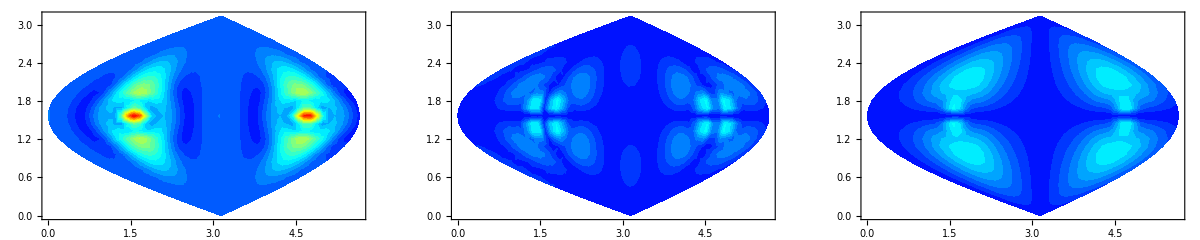

```mathematica
plotGreen@sphericalsN[{2,0}]
```

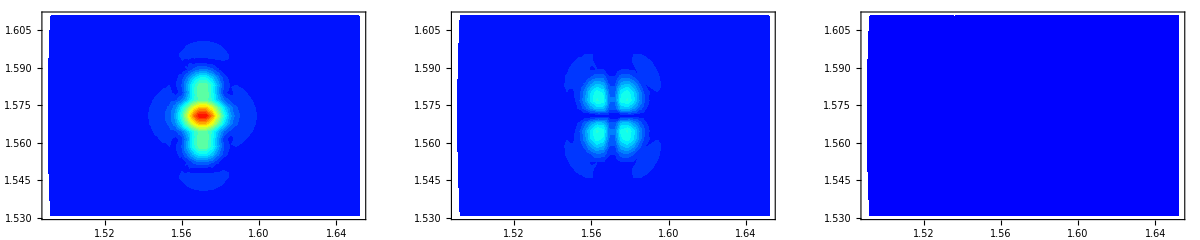

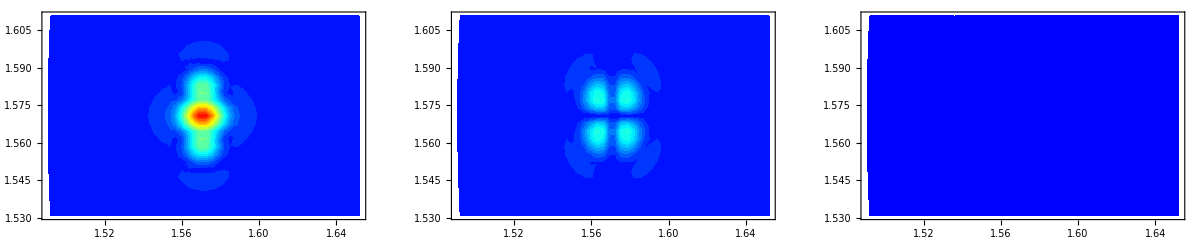

```mathematica
plotGreen@gBaddy
plotGreen[
-1.13/Max@Abs@sphericalsN[{0,0}]sphericalsN[{0,0}](*+0.02sphericalsN[{1,0}]+0(sphericalsN[{2,-2}]+sphericalsN[{2,2}])*)+0.36/Max@Abs@sphericalsN[{2,0}]sphericalsN[{2,0}]
]
```

```mathematica
Max@Abs@gBaddy
69Max@Abs@sphericalsN[{0,0}]
0.02Max@Abs@sphericalsN[{1,0}]
-0.00626Max@Abs@sphericalsN[{2,0}]
```

13661.8

15222.

7.30065

-5019.67

```mathematica
jacobian=Table[Sin[θn[[iθ]]],{iθ,1,Length@θn},{iϕ,1,Length@ϕn},{i,1,3},{j,1,3}];
maxOrder=2;
sphericalNorm[field_]:=Total[Abs[field]^2 jacobian,4]
optimizeCartesian[groundTruth_]:=Module[{cartesianCoeffs},
cartesianCoeffs=Flatten@Table[α[ax,ay,az,real],
{ax,0,maxOrder},{ay,0,Clip[maxOrder-ax,{0,maxOrder}]},{az,0,Clip[maxOrder-ax-ay,{0,maxOrder}]},{real,0,1}];
getCartesianField[coeffsList_]:=Total[If[#[[1]][[4]]==0,1,ⅈ]#[[2]]cartesiansN[#[[1]][[;;3]]]&/@coeffsList,1];
getCartesianError[coeffsList_,truth_]:=
sphericalNorm[getCartesianField[coeffsList]-truth]/sphericalNorm[truth];
formatCartesianOptimizationToNormal[coeffs_]:=Map[varName|->({{#1,#2,#3,#4},varName}&@@varName),coeffs];
cartesianFunToMinimize[coeffs_]:=getCartesianError[formatCartesianOptimizationToNormal[coeffs],groundTruth];
NMinimize[cartesianFunToMinimize@cartesianCoeffs,cartesianCoeffs]
]
optimizeSpherical[groundTruth_]:=Module[{sphericalCoeffs},
sphericalCoeffs=Flatten@Table[α[l,m,real],{l,0,maxOrder},{m,-l,l},{real,0,1}];
getSphericalField[coeffsList_]:=Total[If[#[[1]][[3]]==0,#[[2]],ⅈ#[[2]]]sphericalsN[#[[1]][[;;2]]]&/@coeffsList,1];
getSphericalError[coeffsList_,truth_]:=sphericalNorm[getSphericalField[coeffsList]-truth]/sphericalNorm[truth];
formatSphericalOptimizationToNormal[coeffs_]:=Map[varName|->({{#1,#2,#3},varName}&@@varName),coeffs];
sphericalFunToMinimize[coeffs_]:=getSphericalError[formatSphericalOptimizationToNormal[coeffs],groundTruth];
NMinimize[sphericalFunToMinimize@sphericalCoeffs,sphericalCoeffs]
]
(*resultSpherical=optimizeSpherical[gBaddy]*)
comparison[OptionsPattern[UseParallel->False]]:=Module[{p1,p2},
If[OptionValue[UseParallel],
p1=ParallelSubmit[optimizeCartesian[gBaddy]];
p2=ParallelSubmit[optimizeSpherical[gBaddy]];
WaitAll[{p1,p2}],
{optimizeCartesian[truth],optimizeSpherical[truth]}
]
]
result=comparison[UseParallel->True];
```

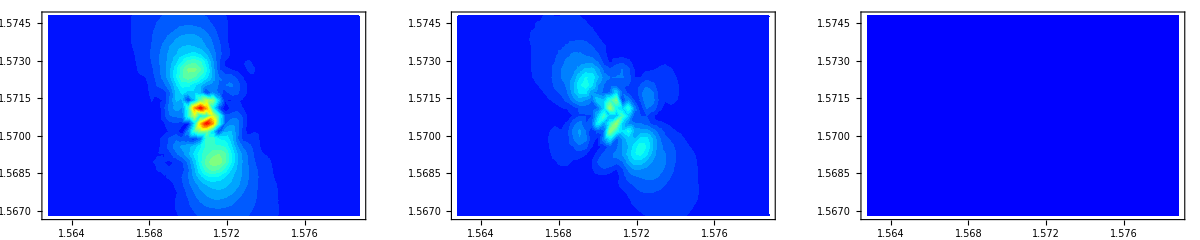

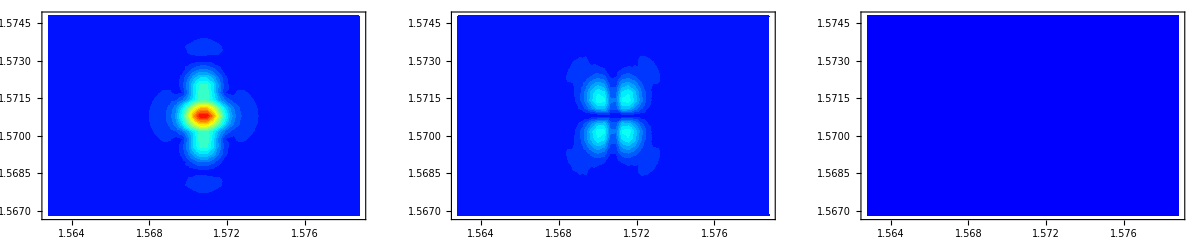

548.439

20.835

```mathematica
(*αGroundTruth=Keys[Association@processedData[[ind]]][[1]]*)
greenCartesian=getCartesianField@KeyValueMap[{key,value}|->{(({#1,#2,#3,#4}&@@key)),value},Association[result[[1]][[2]]]];
greenSpherical=getSphericalField@KeyValueMap[{key,value}|->{(({#1,#2,#3}&@@key)),value},Association[result[[2]][[2]]]];
plotGreen@greenCartesian
plotGreen@greenSpherical
Sqrt[result[[1]][[1]]]100
Sqrt[result[[2]][[1]]]100
```

```mathematica
gTest=Simplify[TransformedField["Cartesian"->"Spherical",D[GChen[[1,1]],{z,0}]/.{k0->k0n,ϵzz->4},R->{ρ,θ,ϕ}]/.ρ->rn];
```

```mathematica
groundTruthNorm=sphericalInt[Abs[gTest]^2];
sphericalInt[expr_]:=NIntegrate[expr Sin[θ],{θ,0,π},{ϕ,0,2π},
AccuracyGoal->7,PrecisionGoal->4,WorkingPrecision->50,MaxRecursion->20,Method->"GaussKronrodRule"]
lMax=12;
projectionResult=Flatten[Parallelize@Table[{l,m,sphericalInt[Conjugate[SphericalHarmonicY[l,m,θ,ϕ]]gTest]
},
{l,0,lMax},{m,-l,l}
],1];
projectionResult=Map[If[Abs@#<1*^-12,0,#]&,projectionResult,{
If[Length@gTest==1,2,3]
}];
```

```mathematica
plotResult=ParallelTable[{lMaxProj,Module[{GChenNumSpherical,error},
GChenNumSpherical=Total@Map[Function[{l,m,p},
If[l<=lMaxProj,
SphericalHarmonicY[l,m,θ,ϕ]p ,
0
]
]@@#&,projectionResult,{1}];
(*Print@GChenNumSpherical*)
error=sphericalInt[Total@Abs[GChenNumSpherical-gTest]^2]/groundTruthNorm 100
]},{lMaxProj,0,lMax}];
```

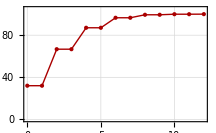

```mathematica
plotData=Map[{#[[1]],100-#[[2]]}&,plotResult];
plot=ListPlot[plotData,
Joined->True,
PlotStyle->{Darker@Red,Thick},
Frame->True,
PlotRange->{{0,lMax},{0,105}},
Mesh->All,
MeshStyle->{PointSize[Medium]},
FrameStyle->Directive[Black],
GridLines->Automatic,
BaseStyle->{FontFamily->"Times New Roman",FontSize->10},
ImageSize->{72 3,Automatic}
]
Export[FileNameJoin[{NotebookDirectory[],"figs","export4.svg"}],plot];
Export[FileNameJoin[{NotebookDirectory[],"figs","export4.csv"}],plotData];
```

```mathematica
Coefficient[Simplify[TransformedField["Cartesian"->"Cylindrical", GChen[[1,1]],R->{ρ,ϕ,zc}]]//Expand,ϵzz]
```

-(ⅇ^(ⅈ k0 √(zc^2+ϵzz ρ^2)) zc^2)/(4 k0^2 π (zc^2+ϵzz ρ^2)^(5/2))+(ⅇ^(ⅈ k0 √(zc^2+ϵzz ρ^2)) zc^4)/(8 π (zc^2+ϵzz ρ^2)^(5/2))+(ⅇ^(ⅈ k0 √(zc^2+ϵzz ρ^2)) zc^4 Cos[2 ϕ])/(8 π (zc^2+ϵzz ρ^2)^(5/2))

```mathematica
toSphericalTfm=MapThread[#1->#2&,{R,CoordinateTransformData["Spherical"->"Cartesian","Mapping"][{r,θ,ϕ}]}];
ϵzzn=1000^2;
subs={k0->k0n,ϵzz->ϵzzn,r->1,ρ->Sin[θ]};
g0=Exp[ⅉ k0 Sqrt[x^2+y^2+z^2]]/(4π  Sqrt[x^2+y^2+z^2]);
h0=-(ⅈ ⅇ^(ⅈ k0 z) ExpIntegralEi[ⅈ k0 (-z+√(x^2+y^2+z^2))])/(8 k0 π)-(ⅈ ⅇ^(-ⅈ k0 z) ExpIntegralEi[ⅈ k0 (z+√(x^2+y^2+z^2))])/(8 k0 π)(*-(ⅈ ⅇ^(-ⅈ k0 Abs@ z) Log[x^2+y^2])/(8 k0 π)*);
(*h0=(Exp[-1/2/(x^2+y^2)/ϵzz]/Sqrt@ϵzz Sin[k0 z])/k0;*)
GChenLar={{(-k0^2h0-D[h0,x,x]-D[h0,z,z])//Simplify,0,0},{-D[h0,x,y]//Simplify,0,0},{0,0,0}};
(*re=Sqrt[ϵzz]ρ;
c={0,0,1};
iTransverse=DiagonalMatrix[{1,1,0}];
ϵinvϵ=ϵzz iTransverse;
expTerm=Exp[ⅉ k0 re]/re;
GLar=-ϵzz Exp[ⅉ k0 re/2]/re Sin[k0 re/2]/(k0 re/2)(
IdentityMatrix[3]-c⊗c-2(R×c)⊗(R×c)/ρ^2
);
GChenLar=(1/(4π)GLar/.ρ->Sqrt[x^2+y^2]);*)
(*GChenLar={{ϵzz^2 Simplify@TransformedField["Cylindrical"->"Cartesian",Coefficient[Expand@Simplify[TransformedField["Cartesian"->"Cylindrical", GChen[[1,1]],R->{ρ,ϕ,zc}]],ϵzz^(1)],{ρ,ϕ,zc}->R],0,0},{0,0,0},{0,0,0}};*)
(*GChenLar={{ϵzz^1Simplify@ Coefficient[GChen[[1,1]],ϵzz^1],0,0},{0,0,0},{0,0,0}};*)
(*GChenLar={{Log[x^2+y^2]Sin[ϵzzn z]Sign[z],0,0},{0,0,0},{0,0,0}};*)
GChenSphere=Simplify[GChen/.toSphericalTfm/.subs];
GChenLarSphere=Simplify[GChenLar/.toSphericalTfm/.subs]/.{Sign'[x_]:>2DiracDelta[x],Sign''[x_]:>2DiracDelta'[x]}
smoothSymmetricStep=(Erf[ϵzzn θ-2]+Erf[ϵzzn(π-θ)-2])/2;
```

{{((2 π-2 π Cos[2 θ]+π Cos[2 θ-2 ϕ]-4 ⅈ Cos[2 ϕ]-2 π Cos[2 ϕ]+π Cos[2 (θ+ϕ)]) Csc[θ]^2)/(32 π^2),0,0},{((-2 ⅈ-π+π Cos[2 θ]) Csc[θ]^2 Sin[2 ϕ])/(16 π^2),0,0},{0,0,0}}

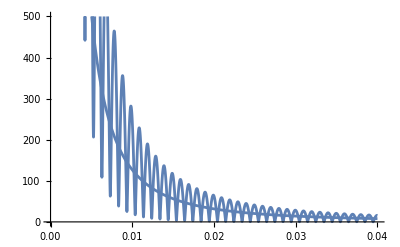

```mathematica
plotLine[expr_]:=Module[{p},p=expr[[1,1]]/.ϕ->0;
Plot[Abs@p,{θ,1/100/20,4/100/1},PlotRange->{0,10000/20}]
]
Show[plotLine[GChenSphere],
plotLine[GChenLarSphere ]]
```

299.704

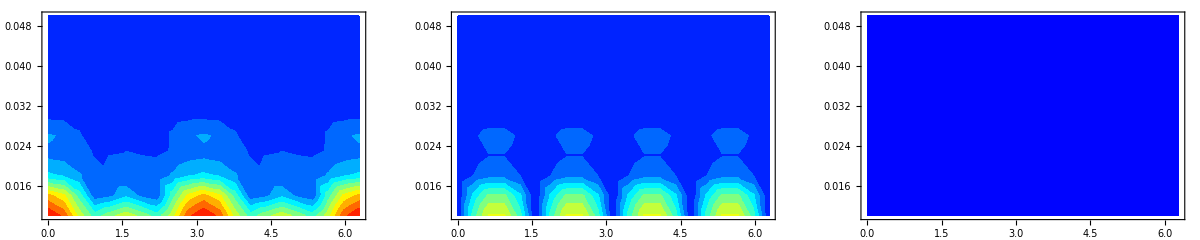

253.311

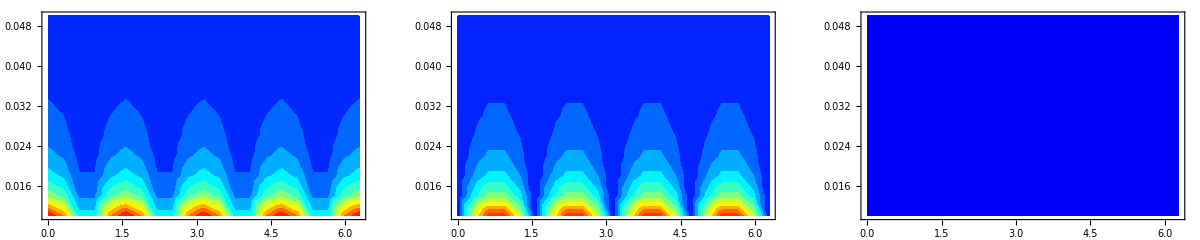

```mathematica
sampleNumber=20;
margin=1*^-2;
ϕn=Subdivide[0,2π,sampleNumber];
θn=Subdivide[1/Sqrt@ϵzzn,5/Sqrt@ϵzzn/1,sampleNumber/2];
numeralize[g_]:=Parallelize@Outer[
Function[{θ,ϕ},
N[g/.{x->rn Cos[ϕ]Sin[θ],y->rn Sin[ϕ]Sin[θ],z->rn Cos[θ],ϵzz->ϵzzn,k0->k0n}]
],
θn,ϕn
];
plotGreen[g_]:=GraphicsGrid@Transpose@Module[{m},
m=Max[Abs[g]];
Print@m;
Table[
ListContourPlot[Flatten[MapIndexed[
{element,index}|->{ϕn[[index[[2]]]],θn[[index[[1]]]],Abs[element[[i,j]]]},
g/m,{2}],1],
AspectRatio->1/2,
ContourLabels->Automatic,
PlotRange->{{0,2π},{Min@θn,Max@θn},{0,1}},
Contours->Subdivide[0,1,11],
ColorFunction->jetColorFunction,
ContourStyle->None,
ColorFunctionScaling->False
],
{i,1,3},{j,dimKept,dimKept}]
]
GChen[[;;,2;;]]=0;
plotGreen@numeralize@GChen
plotGreen@numeralize@(2GChenLar)
```

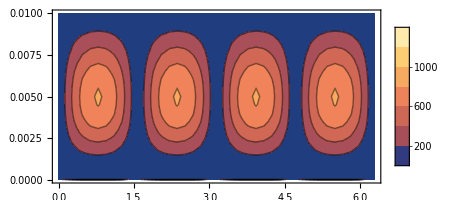

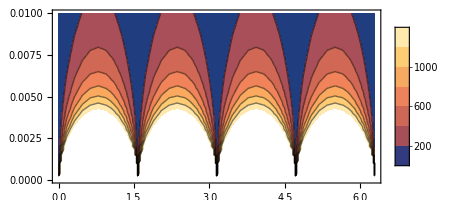

```mathematica
iPlot=2;
jPlot=1;
singularPlot[expr_]:=ContourPlot[Abs@expr[[iPlot,jPlot]],{ϕ,0,2π},{θ,0,.01},MaxRecursion->0,PlotPoints->{41,21},AspectRatio->1/2,PlotRange->{0,1400},PlotLegends->Automatic]
singularPlot[GChenSphere]
singularPlot[GChenLarSphere]
(*(*margin=1*^-6;*)
margin=.1/180π;
sphericalInt[expr_]:=NIntegrate[smoothSymmetricStep expr Sin[θ],{θ,margin,π-margin},{ϕ,0,2π},
AccuracyGoal->7,PrecisionGoal->4,WorkingPrecision->50,MaxRecursion->20,Method->"GaussKronrodRule"];
ParallelTable[Module[{GChenSphereNorm},
GChenSphereNorm=sphericalInt[Abs[GChenSphere[[iPlot,jPlot]]]^2];
If[GChenSphereNorm>1*^-6,
sphericalInt[Abs[GChenLarSphere[[iPlot,jPlot]]-GChenSphere[[iPlot,jPlot]]]^2]/GChenSphereNorm 100,
0]],
{iPlot,1,3},{jPlot,1,1},Method->"CoarsestGrained"]*)
```

```mathematica
saveToFile[α_]:=Module[{filename,fd,toExport},
filename=FileNameJoin[{NotebookDirectory[],"data","mathematica","eps_"<>ToString@ϵzzn<>"/"<>ToString@α[[1]]<>ToString@α[[2]]<>ToString@α[[3]]<>".txt"}];
fd=OpenWrite[filename];
Table[WriteString[filename,"This line empty on purpose\n"],{i,1,9}];
Close[fd];
fd=OpenAppend[filename];
toExport=cartesiansN[α];
Table[
WriteString[filename,
ToString[N[rn Cos[θn[[i]]]],CForm]<>" "<>
ToString[N[rn Cos[ϕn[[j]]]Sin[θn[[i]]]],CForm]<>" "<>
ToString[N[rn Sin[ϕn[[j]]]Sin[θn[[i]]]],CForm]<>" "<>
ToString[N[Re@toExport[[i,j,1,1]]],CForm]<>" "<>
ToString[N[Im@toExport[[i,j,1,1]]],CForm]<>" "<>
ToString[N[Re@toExport[[i,j,2,1]]],CForm]<>" "<>
ToString[N[Im@toExport[[i,j,2,1]]],CForm]<>" "<>
ToString[N[Re@toExport[[i,j,3,1]]],CForm]<>" "<>
ToString[N[Im@toExport[[i,j,3,1]]],CForm]<>" "<>
"\n"],
{i,1,Length@θn},{j,1,Length@ϕn}];
Close@fd;
]
Table[saveToFile[{ax,ay,az}],
{ax,0,maxOrder},{ay,0,Clip[maxOrder-ax,{0,maxOrder}]},{az,0,Clip[maxOrder-ax-ay,{0,maxOrder}]}];
```

```mathematica
sphericalToCartesian[{1,-1}]
```

<|{1,0,0}→(ⅈ √(3/2))/(2 π^(3/2)),{0,1,0}→(√(3/2))/(2 π^(3/2))|>

```mathematica
KeyValueMap[{lm,assoc}|->Module[{},ToString@lm<>":\n{"<>
KeyValueMap[{α,coeff}|->ToString[α]<>":"<>ToString[coeff,CForm]<>",\n"
,assoc]<>"}"],
sphericalToCartesian]
```

{{0, 0}:
{{0, 0, 0}:Complex(0,-1)/Sqrt(Pi),
},{1, -1}:
{{1, 0, 0}:(Complex(0,0.5)*Sqrt(1.5))/Power(Pi,1.5),
{0, 1, 0}:Sqrt(1.5)/(2.*Power(Pi,1.5)),
},{1, 0}:
{{0, 0, 1}:(Complex(0,0.5)*Sqrt(3))/Power(Pi,1.5),
},{1, 1}:
{{1, 0, 0}:(Complex(0,-0.5)*Sqrt(1.5))/Power(Pi,1.5),
{0, 1, 0}:Sqrt(1.5)/(2.*Power(Pi,1.5)),
},{2, -2}:
{{2, 0, 0}:(Complex(0,-0.125)*Sqrt(7.5))/Power(Pi,2.5),
{1, 1, 0}:-0.25*Sqrt(7.5)/Power(Pi,2.5),
{0, 2, 0}:(Complex(0,0.125)*Sqrt(7.5))/Power(Pi,2.5),
},{2, -1}:
{{1, 0, 1}:(Complex(0,-0.25)*Sqrt(7.5))/Power(Pi,2.5),
{0, 1, 1}:-0.25*Sqrt(7.5)/Power(Pi,2.5),
},{2, 0}:
{{2, 0, 0}:(Complex(0,0.125)*Sqrt(5))/Power(Pi,2.5),
{0, 2, 0}:(Complex(0,0.125)*Sqrt(5))/Power(Pi,2.5),
{0, 0, 2}:(Complex(0,-0.25)*Sqrt(5))/Power(Pi,2.5),
},{2, 1}:
{{1, 0, 1}:(Complex(0,0.25)*Sqrt(7.5))/Power(Pi,2.5),
{0, 1, 1}:-0.25*Sqrt(7.5)/Power(Pi,2.5),
},{2, 2}:
{{2, 0, 0}:(Complex(0,-0.125)*Sqrt(7.5))/Power(Pi,2.5),
{1, 1, 0}:Sqrt(7.5)/(4.*Power(Pi,2.5)),
{0, 2, 0}:(Complex(0,0.125)*Sqrt(7.5))/Power(Pi,2.5),
},{3, -3}:
{{3, 0, 0}:(Complex(0,0.03125)*Sqrt(35))/Power(Pi,3.5),
{2, 1, 0}:(3*Sqrt(35))/(32.*Power(Pi,3.5)),
{1, 2, 0}:(Complex(0,-0.09375)*Sqrt(35))/Power(Pi,3.5),
{0, 3, 0}:-0.03125*Sqrt(35)/Power(Pi,3.5),
},{3, -2}:
{{2, 0, 1}:(Complex(0,0.0625)*Sqrt(52.5))/Power(Pi,3.5),
{1, 1, 1}:Sqrt(52.5)/(8.*Power(Pi,3.5)),
{0, 2, 1}:(Complex(0,-0.0625)*Sqrt(52.5))/Power(Pi,3.5),
},{3, -1}:
{{3, 0, 0}:(Complex(0,-0.03125)*Sqrt(21))/Power(Pi,3.5),
{2, 1, 0}:-0.03125*Sqrt(21)/Power(Pi,3.5),
{1, 2, 0}:(Complex(0,-0.03125)*Sqrt(21))/Power(Pi,3.5),
{1, 0, 2}:(Complex(0,0.125)*Sqrt(21))/Power(Pi,3.5),
{0, 3, 0}:-0.03125*Sqrt(21)/Power(Pi,3.5),
{0, 1, 2}:Sqrt(21)/(8.*Power(Pi,3.5)),
},{3, 0}:
{{2, 0, 1}:(Complex(0,-0.1875)*Sqrt(7))/Power(Pi,3.5),
{0, 2, 1}:(Complex(0,-0.1875)*Sqrt(7))/Power(Pi,3.5),
{0, 0, 3}:(Complex(0,0.125)*Sqrt(7))/Power(Pi,3.5),
},{3, 1}:
{{3, 0, 0}:(Complex(0,0.03125)*Sqrt(21))/Power(Pi,3.5),
{2, 1, 0}:-0.03125*Sqrt(21)/Power(Pi,3.5),
{1, 2, 0}:(Complex(0,0.03125)*Sqrt(21))/Power(Pi,3.5),
{1, 0, 2}:(Complex(0,-0.125)*Sqrt(21))/Power(Pi,3.5),
{0, 3, 0}:-0.03125*Sqrt(21)/Power(Pi,3.5),
{0, 1, 2}:Sqrt(21)/(8.*Power(Pi,3.5)),
},{3, 2}:
{{2, 0, 1}:(Complex(0,0.0625)*Sqrt(52.5))/Power(Pi,3.5),
{1, 1, 1}:-0.125*Sqrt(52.5)/Power(Pi,3.5),
{0, 2, 1}:(Complex(0,-0.0625)*Sqrt(52.5))/Power(Pi,3.5),
},{3, 3}:
{{3, 0, 0}:(Complex(0,-0.03125)*Sqrt(35))/Power(Pi,3.5),
{2, 1, 0}:(3*Sqrt(35))/(32.*Power(Pi,3.5)),
{1, 2, 0}:(Complex(0,0.09375)*Sqrt(35))/Power(Pi,3.5),
{0, 3, 0}:-0.03125*Sqrt(35)/Power(Pi,3.5),
},{4, -4}:
{{4, 0, 0}:(Complex(0,-0.0234375)*Sqrt(17.5))/Power(Pi,4.5),
{3, 1, 0}:(-3*Sqrt(17.5))/(32.*Power(Pi,4.5)),
{2, 2, 0}:(Complex(0,0.140625)*Sqrt(17.5))/Power(Pi,4.5),
{1, 3, 0}:(3*Sqrt(17.5))/(32.*Power(Pi,4.5)),
{0, 4, 0}:(Complex(0,-0.0234375)*Sqrt(17.5))/Power(Pi,4.5),
},{4, -3}:
{{3, 0, 1}:(Complex(0,-0.046875)*Sqrt(35))/Power(Pi,4.5),
{2, 1, 1}:(-9*Sqrt(35))/(64.*Power(Pi,4.5)),
{1, 2, 1}:(Complex(0,0.140625)*Sqrt(35))/Power(Pi,4.5),
{0, 3, 1}:(3*Sqrt(35))/(64.*Power(Pi,4.5)),
},{4, -2}:
{{4, 0, 0}:(Complex(0,0.046875)*Sqrt(2.5))/Power(Pi,4.5),
{3, 1, 0}:(3*Sqrt(2.5))/(32.*Power(Pi,4.5)),
{2, 0, 2}:(Complex(0,-0.28125)*Sqrt(2.5))/Power(Pi,4.5),
{1, 3, 0}:(3*Sqrt(2.5))/(32.*Power(Pi,4.5)),
{1, 1, 2}:(-9*Sqrt(2.5))/(16.*Power(Pi,4.5)),
{0, 4, 0}:(Complex(0,-0.046875)*Sqrt(2.5))/Power(Pi,4.5),
{0, 2, 2}:(Complex(0,0.28125)*Sqrt(2.5))/Power(Pi,4.5),
},{4, -1}:
{{3, 0, 1}:(Complex(0,0.140625)*Sqrt(5))/Power(Pi,4.5),
{2, 1, 1}:(9*Sqrt(5))/(64.*Power(Pi,4.5)),
{1, 2, 1}:(Complex(0,0.140625)*Sqrt(5))/Power(Pi,4.5),
{1, 0, 3}:(Complex(0,-0.1875)*Sqrt(5))/Power(Pi,4.5),
{0, 3, 1}:(9*Sqrt(5))/(64.*Power(Pi,4.5)),
{0, 1, 3}:(-3*Sqrt(5))/(16.*Power(Pi,4.5)),
},{4, 0}:
{{4, 0, 0}:Complex(0,-0.0703125)/Power(Pi,4.5),
{2, 2, 0}:Complex(0,-0.140625)/Power(Pi,4.5),
{2, 0, 2}:Complex(0,0.5625)/Power(Pi,4.5),
{0, 4, 0}:Complex(0,-0.0703125)/Power(Pi,4.5),
{0, 2, 2}:Complex(0,0.5625)/Power(Pi,4.5),
{0, 0, 4}:Complex(0,-0.1875)/Power(Pi,4.5),
},{4, 1}:
{{3, 0, 1}:(Complex(0,-0.140625)*Sqrt(5))/Power(Pi,4.5),
{2, 1, 1}:(9*Sqrt(5))/(64.*Power(Pi,4.5)),
{1, 2, 1}:(Complex(0,-0.140625)*Sqrt(5))/Power(Pi,4.5),
{1, 0, 3}:(Complex(0,0.1875)*Sqrt(5))/Power(Pi,4.5),
{0, 3, 1}:(9*Sqrt(5))/(64.*Power(Pi,4.5)),
{0, 1, 3}:(-3*Sqrt(5))/(16.*Power(Pi,4.5)),
},{4, 2}:
{{4, 0, 0}:(Complex(0,0.046875)*Sqrt(2.5))/Power(Pi,4.5),
{3, 1, 0}:(-3*Sqrt(2.5))/(32.*Power(Pi,4.5)),
{2, 0, 2}:(Complex(0,-0.28125)*Sqrt(2.5))/Power(Pi,4.5),
{1, 3, 0}:(-3*Sqrt(2.5))/(32.*Power(Pi,4.5)),
{1, 1, 2}:(9*Sqrt(2.5))/(16.*Power(Pi,4.5)),
{0, 4, 0}:(Complex(0,-0.046875)*Sqrt(2.5))/Power(Pi,4.5),
{0, 2, 2}:(Complex(0,0.28125)*Sqrt(2.5))/Power(Pi,4.5),
},{4, 3}:
{{3, 0, 1}:(Complex(0,0.046875)*Sqrt(35))/Power(Pi,4.5),
{2, 1, 1}:(-9*Sqrt(35))/(64.*Power(Pi,4.5)),
{1, 2, 1}:(Complex(0,-0.140625)*Sqrt(35))/Power(Pi,4.5),
{0, 3, 1}:(3*Sqrt(35))/(64.*Power(Pi,4.5)),
},{4, 4}:
{{4, 0, 0}:(Complex(0,-0.0234375)*Sqrt(17.5))/Power(Pi,4.5),
{3, 1, 0}:(3*Sqrt(17.5))/(32.*Power(Pi,4.5)),
{2, 2, 0}:(Complex(0,0.140625)*Sqrt(17.5))/Power(Pi,4.5),
{1, 3, 0}:(-3*Sqrt(17.5))/(32.*Power(Pi,4.5)),
{0, 4, 0}:(Complex(0,-0.0234375)*Sqrt(17.5))/Power(Pi,4.5),
},{5, -5}:
{{5, 0, 0}:(Complex(0,0.005859375)*Sqrt(77))/Power(Pi,5.5),
{4, 1, 0}:(15*Sqrt(77))/(512.*Power(Pi,5.5)),
{3, 2, 0}:(Complex(0,-0.05859375)*Sqrt(77))/Power(Pi,5.5),
{2, 3, 0}:(-15*Sqrt(77))/(256.*Power(Pi,5.5)),
{1, 4, 0}:(Complex(0,0.029296875)*Sqrt(77))/Power(Pi,5.5),
{0, 5, 0}:(3*Sqrt(77))/(512.*Power(Pi,5.5)),
},{5, -4}:
{{4, 0, 1}:(Complex(0,0.01171875)*Sqrt(192.5))/Power(Pi,5.5),
{3, 1, 1}:(3*Sqrt(192.5))/(64.*Power(Pi,5.5)),
{2, 2, 1}:(Complex(0,-0.0703125)*Sqrt(192.5))/Power(Pi,5.5),
{1, 3, 1}:(-3*Sqrt(192.5))/(64.*Power(Pi,5.5)),
{0, 4, 1}:(Complex(0,0.01171875)*Sqrt(192.5))/Power(Pi,5.5),
},{5, -3}:
{{5, 0, 0}:(Complex(0,-0.001953125)*Sqrt(385))/Power(Pi,5.5),
{4, 1, 0}:(-3*Sqrt(385))/(512.*Power(Pi,5.5)),
{3, 2, 0}:(Complex(0,0.00390625)*Sqrt(385))/Power(Pi,5.5),
{3, 0, 2}:(Complex(0,0.015625)*Sqrt(385))/Power(Pi,5.5),
{2, 3, 0}:-0.00390625*Sqrt(385)/Power(Pi,5.5),
{2, 1, 2}:(3*Sqrt(385))/(64.*Power(Pi,5.5)),
{1, 4, 0}:(Complex(0,0.005859375)*Sqrt(385))/Power(Pi,5.5),
{1, 2, 2}:(Complex(0,-0.046875)*Sqrt(385))/Power(Pi,5.5),
{0, 5, 0}:Sqrt(385)/(512.*Power(Pi,5.5)),
{0, 3, 2}:-0.015625*Sqrt(385)/Power(Pi,5.5),
},{5, -2}:
{{4, 0, 1}:(Complex(0,-0.0078125)*Sqrt(577.5))/Power(Pi,5.5),
{3, 1, 1}:-0.015625*Sqrt(577.5)/Power(Pi,5.5),
{2, 0, 3}:(Complex(0,0.015625)*Sqrt(577.5))/Power(Pi,5.5),
{1, 3, 1}:-0.015625*Sqrt(577.5)/Power(Pi,5.5),
{1, 1, 3}:Sqrt(577.5)/(32.*Power(Pi,5.5)),
{0, 4, 1}:(Complex(0,0.0078125)*Sqrt(577.5))/Power(Pi,5.5),
{0, 2, 3}:(Complex(0,-0.015625)*Sqrt(577.5))/Power(Pi,5.5),
},{5, -1}:
{{5, 0, 0}:(Complex(0,0.00390625)*Sqrt(82.5))/Power(Pi,5.5),
{4, 1, 0}:Sqrt(82.5)/(256.*Power(Pi,5.5)),
{3, 2, 0}:(Complex(0,0.0078125)*Sqrt(82.5))/Power(Pi,5.5),
{3, 0, 2}:(Complex(0,-0.046875)*Sqrt(82.5))/Power(Pi,5.5),
{2, 3, 0}:Sqrt(82.5)/(128.*Power(Pi,5.5)),
{2, 1, 2}:(-3*Sqrt(82.5))/(64.*Power(Pi,5.5)),
{1, 4, 0}:(Complex(0,0.00390625)*Sqrt(82.5))/Power(Pi,5.5),
{1, 2, 2}:(Complex(0,-0.046875)*Sqrt(82.5))/Power(Pi,5.5),
{1, 0, 4}:(Complex(0,0.03125)*Sqrt(82.5))/Power(Pi,5.5),
{0, 5, 0}:Sqrt(82.5)/(256.*Power(Pi,5.5)),
{0, 3, 2}:(-3*Sqrt(82.5))/(64.*Power(Pi,5.5)),
{0, 1, 4}:Sqrt(82.5)/(32.*Power(Pi,5.5)),
},{5, 0}:
{{4, 0, 1}:(Complex(0,0.05859375)*Sqrt(11))/Power(Pi,5.5),
{2, 2, 1}:(Complex(0,0.1171875)*Sqrt(11))/Power(Pi,5.5),
{2, 0, 3}:(Complex(0,-0.15625)*Sqrt(11))/Power(Pi,5.5),
{0, 4, 1}:(Complex(0,0.05859375)*Sqrt(11))/Power(Pi,5.5),
{0, 2, 3}:(Complex(0,-0.15625)*Sqrt(11))/Power(Pi,5.5),
{0, 0, 5}:(Complex(0,0.03125)*Sqrt(11))/Power(Pi,5.5),
},{5, 1}:
{{5, 0, 0}:(Complex(0,-0.00390625)*Sqrt(82.5))/Power(Pi,5.5),
{4, 1, 0}:Sqrt(82.5)/(256.*Power(Pi,5.5)),
{3, 2, 0}:(Complex(0,-0.0078125)*Sqrt(82.5))/Power(Pi,5.5),
{3, 0, 2}:(Complex(0,0.046875)*Sqrt(82.5))/Power(Pi,5.5),
{2, 3, 0}:Sqrt(82.5)/(128.*Power(Pi,5.5)),
{2, 1, 2}:(-3*Sqrt(82.5))/(64.*Power(Pi,5.5)),
{1, 4, 0}:(Complex(0,-0.00390625)*Sqrt(82.5))/Power(Pi,5.5),
{1, 2, 2}:(Complex(0,0.046875)*Sqrt(82.5))/Power(Pi,5.5),
{1, 0, 4}:(Complex(0,-0.03125)*Sqrt(82.5))/Power(Pi,5.5),
{0, 5, 0}:Sqrt(82.5)/(256.*Power(Pi,5.5)),
{0, 3, 2}:(-3*Sqrt(82.5))/(64.*Power(Pi,5.5)),
{0, 1, 4}:Sqrt(82.5)/(32.*Power(Pi,5.5)),
},{5, 2}:
{{4, 0, 1}:(Complex(0,-0.0078125)*Sqrt(577.5))/Power(Pi,5.5),
{3, 1, 1}:Sqrt(577.5)/(64.*Power(Pi,5.5)),
{2, 0, 3}:(Complex(0,0.015625)*Sqrt(577.5))/Power(Pi,5.5),
{1, 3, 1}:Sqrt(577.5)/(64.*Power(Pi,5.5)),
{1, 1, 3}:-0.03125*Sqrt(577.5)/Power(Pi,5.5),
{0, 4, 1}:(Complex(0,0.0078125)*Sqrt(577.5))/Power(Pi,5.5),
{0, 2, 3}:(Complex(0,-0.015625)*Sqrt(577.5))/Power(Pi,5.5),
},{5, 3}:
{{5, 0, 0}:(Complex(0,0.001953125)*Sqrt(385))/Power(Pi,5.5),
{4, 1, 0}:(-3*Sqrt(385))/(512.*Power(Pi,5.5)),
{3, 2, 0}:(Complex(0,-0.00390625)*Sqrt(385))/Power(Pi,5.5),
{3, 0, 2}:(Complex(0,-0.015625)*Sqrt(385))/Power(Pi,5.5),
{2, 3, 0}:-0.00390625*Sqrt(385)/Power(Pi,5.5),
{2, 1, 2}:(3*Sqrt(385))/(64.*Power(Pi,5.5)),
{1, 4, 0}:(Complex(0,-0.005859375)*Sqrt(385))/Power(Pi,5.5),
{1, 2, 2}:(Complex(0,0.046875)*Sqrt(385))/Power(Pi,5.5),
{0, 5, 0}:Sqrt(385)/(512.*Power(Pi,5.5)),
{0, 3, 2}:-0.015625*Sqrt(385)/Power(Pi,5.5),
},{5, 4}:
{{4, 0, 1}:(Complex(0,0.01171875)*Sqrt(192.5))/Power(Pi,5.5),
{3, 1, 1}:(-3*Sqrt(192.5))/(64.*Power(Pi,5.5)),
{2, 2, 1}:(Complex(0,-0.0703125)*Sqrt(192.5))/Power(Pi,5.5),
{1, 3, 1}:(3*Sqrt(192.5))/(64.*Power(Pi,5.5)),
{0, 4, 1}:(Complex(0,0.01171875)*Sqrt(192.5))/Power(Pi,5.5),
},{5, 5}:
{{5, 0, 0}:(Complex(0,-0.005859375)*Sqrt(77))/Power(Pi,5.5),
{4, 1, 0}:(15*Sqrt(77))/(512.*Power(Pi,5.5)),
{3, 2, 0}:(Complex(0,0.05859375)*Sqrt(77))/Power(Pi,5.5),
{2, 3, 0}:(-15*Sqrt(77))/(256.*Power(Pi,5.5)),
{1, 4, 0}:(Complex(0,-0.029296875)*Sqrt(77))/Power(Pi,5.5),
{0, 5, 0}:(3*Sqrt(77))/(512.*Power(Pi,5.5)),
},{6, -6}:
{{6, 0, 0}:(Complex(0,-0.00048828125)*Sqrt(3003))/Power(Pi,6.5),
{5, 1, 0}:(-3*Sqrt(3003))/(1024.*Power(Pi,6.5)),
{4, 2, 0}:(Complex(0,0.00732421875)*Sqrt(3003))/Power(Pi,6.5),
{3, 3, 0}:(5*Sqrt(3003))/(512.*Power(Pi,6.5)),
{2, 4, 0}:(Complex(0,-0.00732421875)*Sqrt(3003))/Power(Pi,6.5),
{1, 5, 0}:(-3*Sqrt(3003))/(1024.*Power(Pi,6.5)),
{0, 6, 0}:(Complex(0,0.00048828125)*Sqrt(3003))/Power(Pi,6.5),
},{6, -5}:
{{5, 0, 1}:(Complex(0,-0.0029296875)*Sqrt(1001))/Power(Pi,6.5),
{4, 1, 1}:(-15*Sqrt(1001))/(1024.*Power(Pi,6.5)),
{3, 2, 1}:(Complex(0,0.029296875)*Sqrt(1001))/Power(Pi,6.5),
{2, 3, 1}:(15*Sqrt(1001))/(512.*Power(Pi,6.5)),
{1, 4, 1}:(Complex(0,-0.0146484375)*Sqrt(1001))/Power(Pi,6.5),
{0, 5, 1}:(-3*Sqrt(1001))/(1024.*Power(Pi,6.5)),
},{6, -4}:
{{6, 0, 0}:(Complex(0,0.0029296875)*Sqrt(45.5))/Power(Pi,6.5),
{5, 1, 0}:(3*Sqrt(45.5))/(256.*Power(Pi,6.5)),
{4, 2, 0}:(Complex(0,-0.0146484375)*Sqrt(45.5))/Power(Pi,6.5),
{4, 0, 2}:(Complex(0,-0.029296875)*Sqrt(45.5))/Power(Pi,6.5),
{3, 1, 2}:(-15*Sqrt(45.5))/(128.*Power(Pi,6.5)),
{2, 4, 0}:(Complex(0,-0.0146484375)*Sqrt(45.5))/Power(Pi,6.5),
{2, 2, 2}:(Complex(0,0.17578125)*Sqrt(45.5))/Power(Pi,6.5),
{1, 5, 0}:(-3*Sqrt(45.5))/(256.*Power(Pi,6.5)),
{1, 3, 2}:(15*Sqrt(45.5))/(128.*Power(Pi,6.5)),
{0, 6, 0}:(Complex(0,0.0029296875)*Sqrt(45.5))/Power(Pi,6.5),
{0, 4, 2}:(Complex(0,-0.029296875)*Sqrt(45.5))/Power(Pi,6.5),
},{6, -3}:
{{5, 0, 1}:(Complex(0,0.0029296875)*Sqrt(1365))/Power(Pi,6.5),
{4, 1, 1}:(9*Sqrt(1365))/(1024.*Power(Pi,6.5)),
{3, 2, 1}:(Complex(0,-0.005859375)*Sqrt(1365))/Power(Pi,6.5),
{3, 0, 3}:(Complex(0,-0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{2, 3, 1}:(3*Sqrt(1365))/(512.*Power(Pi,6.5)),
{2, 1, 3}:(-3*Sqrt(1365))/(128.*Power(Pi,6.5)),
{1, 4, 1}:(Complex(0,-0.0087890625)*Sqrt(1365))/Power(Pi,6.5),
{1, 2, 3}:(Complex(0,0.0234375)*Sqrt(1365))/Power(Pi,6.5),
{0, 5, 1}:(-3*Sqrt(1365))/(1024.*Power(Pi,6.5)),
{0, 3, 3}:Sqrt(1365)/(128.*Power(Pi,6.5)),
},{6, -2}:
{{6, 0, 0}:(Complex(0,-0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{5, 1, 0}:-0.0009765625*Sqrt(1365)/Power(Pi,6.5),
{4, 2, 0}:(Complex(0,-0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{4, 0, 2}:(Complex(0,0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{3, 3, 0}:-0.001953125*Sqrt(1365)/Power(Pi,6.5),
{3, 1, 2}:Sqrt(1365)/(64.*Power(Pi,6.5)),
{2, 4, 0}:(Complex(0,0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{2, 0, 4}:(Complex(0,-0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{1, 5, 0}:-0.0009765625*Sqrt(1365)/Power(Pi,6.5),
{1, 3, 2}:Sqrt(1365)/(64.*Power(Pi,6.5)),
{1, 1, 4}:-0.015625*Sqrt(1365)/Power(Pi,6.5),
{0, 6, 0}:(Complex(0,0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{0, 4, 2}:(Complex(0,-0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{0, 2, 4}:(Complex(0,0.0078125)*Sqrt(1365))/Power(Pi,6.5),
},{6, -1}:
{{5, 0, 1}:(Complex(0,-0.009765625)*Sqrt(136.5))/Power(Pi,6.5),
{4, 1, 1}:(-5*Sqrt(136.5))/(512.*Power(Pi,6.5)),
{3, 2, 1}:(Complex(0,-0.01953125)*Sqrt(136.5))/Power(Pi,6.5),
{3, 0, 3}:(Complex(0,0.0390625)*Sqrt(136.5))/Power(Pi,6.5),
{2, 3, 1}:(-5*Sqrt(136.5))/(256.*Power(Pi,6.5)),
{2, 1, 3}:(5*Sqrt(136.5))/(128.*Power(Pi,6.5)),
{1, 4, 1}:(Complex(0,-0.009765625)*Sqrt(136.5))/Power(Pi,6.5),
{1, 2, 3}:(Complex(0,0.0390625)*Sqrt(136.5))/Power(Pi,6.5),
{1, 0, 5}:(Complex(0,-0.015625)*Sqrt(136.5))/Power(Pi,6.5),
{0, 5, 1}:(-5*Sqrt(136.5))/(512.*Power(Pi,6.5)),
{0, 3, 3}:(5*Sqrt(136.5))/(128.*Power(Pi,6.5)),
{0, 1, 5}:-0.015625*Sqrt(136.5)/Power(Pi,6.5),
},{6, 0}:
{{6, 0, 0}:(Complex(0,0.0048828125)*Sqrt(13))/Power(Pi,6.5),
{4, 2, 0}:(Complex(0,0.0146484375)*Sqrt(13))/Power(Pi,6.5),
{4, 0, 2}:(Complex(0,-0.087890625)*Sqrt(13))/Power(Pi,6.5),
{2, 4, 0}:(Complex(0,0.0146484375)*Sqrt(13))/Power(Pi,6.5),
{2, 2, 2}:(Complex(0,-0.17578125)*Sqrt(13))/Power(Pi,6.5),
{2, 0, 4}:(Complex(0,0.1171875)*Sqrt(13))/Power(Pi,6.5),
{0, 6, 0}:(Complex(0,0.0048828125)*Sqrt(13))/Power(Pi,6.5),
{0, 4, 2}:(Complex(0,-0.087890625)*Sqrt(13))/Power(Pi,6.5),
{0, 2, 4}:(Complex(0,0.1171875)*Sqrt(13))/Power(Pi,6.5),
{0, 0, 6}:(Complex(0,-0.015625)*Sqrt(13))/Power(Pi,6.5),
},{6, 1}:
{{5, 0, 1}:(Complex(0,0.009765625)*Sqrt(136.5))/Power(Pi,6.5),
{4, 1, 1}:(-5*Sqrt(136.5))/(512.*Power(Pi,6.5)),
{3, 2, 1}:(Complex(0,0.01953125)*Sqrt(136.5))/Power(Pi,6.5),
{3, 0, 3}:(Complex(0,-0.0390625)*Sqrt(136.5))/Power(Pi,6.5),
{2, 3, 1}:(-5*Sqrt(136.5))/(256.*Power(Pi,6.5)),
{2, 1, 3}:(5*Sqrt(136.5))/(128.*Power(Pi,6.5)),
{1, 4, 1}:(Complex(0,0.009765625)*Sqrt(136.5))/Power(Pi,6.5),
{1, 2, 3}:(Complex(0,-0.0390625)*Sqrt(136.5))/Power(Pi,6.5),
{1, 0, 5}:(Complex(0,0.015625)*Sqrt(136.5))/Power(Pi,6.5),
{0, 5, 1}:(-5*Sqrt(136.5))/(512.*Power(Pi,6.5)),
{0, 3, 3}:(5*Sqrt(136.5))/(128.*Power(Pi,6.5)),
{0, 1, 5}:-0.015625*Sqrt(136.5)/Power(Pi,6.5),
},{6, 2}:
{{6, 0, 0}:(Complex(0,-0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{5, 1, 0}:Sqrt(1365)/(1024.*Power(Pi,6.5)),
{4, 2, 0}:(Complex(0,-0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{4, 0, 2}:(Complex(0,0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{3, 3, 0}:Sqrt(1365)/(512.*Power(Pi,6.5)),
{3, 1, 2}:-0.015625*Sqrt(1365)/Power(Pi,6.5),
{2, 4, 0}:(Complex(0,0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{2, 0, 4}:(Complex(0,-0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{1, 5, 0}:Sqrt(1365)/(1024.*Power(Pi,6.5)),
{1, 3, 2}:-0.015625*Sqrt(1365)/Power(Pi,6.5),
{1, 1, 4}:Sqrt(1365)/(64.*Power(Pi,6.5)),
{0, 6, 0}:(Complex(0,0.00048828125)*Sqrt(1365))/Power(Pi,6.5),
{0, 4, 2}:(Complex(0,-0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{0, 2, 4}:(Complex(0,0.0078125)*Sqrt(1365))/Power(Pi,6.5),
},{6, 3}:
{{5, 0, 1}:(Complex(0,-0.0029296875)*Sqrt(1365))/Power(Pi,6.5),
{4, 1, 1}:(9*Sqrt(1365))/(1024.*Power(Pi,6.5)),
{3, 2, 1}:(Complex(0,0.005859375)*Sqrt(1365))/Power(Pi,6.5),
{3, 0, 3}:(Complex(0,0.0078125)*Sqrt(1365))/Power(Pi,6.5),
{2, 3, 1}:(3*Sqrt(1365))/(512.*Power(Pi,6.5)),
{2, 1, 3}:(-3*Sqrt(1365))/(128.*Power(Pi,6.5)),
{1, 4, 1}:(Complex(0,0.0087890625)*Sqrt(1365))/Power(Pi,6.5),
{1, 2, 3}:(Complex(0,-0.0234375)*Sqrt(1365))/Power(Pi,6.5),
{0, 5, 1}:(-3*Sqrt(1365))/(1024.*Power(Pi,6.5)),
{0, 3, 3}:Sqrt(1365)/(128.*Power(Pi,6.5)),
},{6, 4}:
{{6, 0, 0}:(Complex(0,0.0029296875)*Sqrt(45.5))/Power(Pi,6.5),
{5, 1, 0}:(-3*Sqrt(45.5))/(256.*Power(Pi,6.5)),
{4, 2, 0}:(Complex(0,-0.0146484375)*Sqrt(45.5))/Power(Pi,6.5),
{4, 0, 2}:(Complex(0,-0.029296875)*Sqrt(45.5))/Power(Pi,6.5),
{3, 1, 2}:(15*Sqrt(45.5))/(128.*Power(Pi,6.5)),
{2, 4, 0}:(Complex(0,-0.0146484375)*Sqrt(45.5))/Power(Pi,6.5),
{2, 2, 2}:(Complex(0,0.17578125)*Sqrt(45.5))/Power(Pi,6.5),
{1, 5, 0}:(3*Sqrt(45.5))/(256.*Power(Pi,6.5)),
{1, 3, 2}:(-15*Sqrt(45.5))/(128.*Power(Pi,6.5)),
{0, 6, 0}:(Complex(0,0.0029296875)*Sqrt(45.5))/Power(Pi,6.5),
{0, 4, 2}:(Complex(0,-0.029296875)*Sqrt(45.5))/Power(Pi,6.5),
},{6, 5}:
{{5, 0, 1}:(Complex(0,0.0029296875)*Sqrt(1001))/Power(Pi,6.5),
{4, 1, 1}:(-15*Sqrt(1001))/(1024.*Power(Pi,6.5)),
{3, 2, 1}:(Complex(0,-0.029296875)*Sqrt(1001))/Power(Pi,6.5),
{2, 3, 1}:(15*Sqrt(1001))/(512.*Power(Pi,6.5)),
{1, 4, 1}:(Complex(0,0.0146484375)*Sqrt(1001))/Power(Pi,6.5),
{0, 5, 1}:(-3*Sqrt(1001))/(1024.*Power(Pi,6.5)),
},{6, 6}:
{{6, 0, 0}:(Complex(0,-0.00048828125)*Sqrt(3003))/Power(Pi,6.5),
{5, 1, 0}:(3*Sqrt(3003))/(1024.*Power(Pi,6.5)),
{4, 2, 0}:(Complex(0,0.00732421875)*Sqrt(3003))/Power(Pi,6.5),
{3, 3, 0}:(-5*Sqrt(3003))/(512.*Power(Pi,6.5)),
{2, 4, 0}:(Complex(0,-0.00732421875)*Sqrt(3003))/Power(Pi,6.5),
{1, 5, 0}:(3*Sqrt(3003))/(1024.*Power(Pi,6.5)),
{0, 6, 0}:(Complex(0,0.00048828125)*Sqrt(3003))/Power(Pi,6.5),
},{7, -7}:
{{7, 0, 0}:(Complex(0,0.000732421875)*Sqrt(357.5))/Power(Pi,7.5),
{6, 1, 0}:(21*Sqrt(357.5))/(4096.*Power(Pi,7.5)),
{5, 2, 0}:(Complex(0,-0.015380859375)*Sqrt(357.5))/Power(Pi,7.5),
{4, 3, 0}:(-105*Sqrt(357.5))/(4096.*Power(Pi,7.5)),
{3, 4, 0}:(Complex(0,0.025634765625)*Sqrt(357.5))/Power(Pi,7.5),
{2, 5, 0}:(63*Sqrt(357.5))/(4096.*Power(Pi,7.5)),
{1, 6, 0}:(Complex(0,-0.005126953125)*Sqrt(357.5))/Power(Pi,7.5),
{0, 7, 0}:(-3*Sqrt(357.5))/(4096.*Power(Pi,7.5)),
},{7, -6}:
{{6, 0, 1}:(Complex(0,0.000732421875)*Sqrt(5005))/Power(Pi,7.5),
{5, 1, 1}:(9*Sqrt(5005))/(2048.*Power(Pi,7.5)),
{4, 2, 1}:(Complex(0,-0.010986328125)*Sqrt(5005))/Power(Pi,7.5),
{3, 3, 1}:(-15*Sqrt(5005))/(1024.*Power(Pi,7.5)),
{2, 4, 1}:(Complex(0,0.010986328125)*Sqrt(5005))/Power(Pi,7.5),
{1, 5, 1}:(9*Sqrt(5005))/(2048.*Power(Pi,7.5)),
{0, 6, 1}:(Complex(0,-0.000732421875)*Sqrt(5005))/Power(Pi,7.5),
},{7, -5}:
{{7, 0, 0}:(Complex(0,-0.000732421875)*Sqrt(192.5))/Power(Pi,7.5),
{6, 1, 0}:(-15*Sqrt(192.5))/(4096.*Power(Pi,7.5)),
{5, 2, 0}:(Complex(0,0.006591796875)*Sqrt(192.5))/Power(Pi,7.5),
{5, 0, 2}:(Complex(0,0.0087890625)*Sqrt(192.5))/Power(Pi,7.5),
{4, 3, 0}:(15*Sqrt(192.5))/(4096.*Power(Pi,7.5)),
{4, 1, 2}:(45*Sqrt(192.5))/(1024.*Power(Pi,7.5)),
{3, 4, 0}:(Complex(0,0.003662109375)*Sqrt(192.5))/Power(Pi,7.5),
{3, 2, 2}:(Complex(0,-0.087890625)*Sqrt(192.5))/Power(Pi,7.5),
{2, 5, 0}:(27*Sqrt(192.5))/(4096.*Power(Pi,7.5)),
{2, 3, 2}:(-45*Sqrt(192.5))/(512.*Power(Pi,7.5)),
{1, 6, 0}:(Complex(0,-0.003662109375)*Sqrt(192.5))/Power(Pi,7.5),
{1, 4, 2}:(Complex(0,0.0439453125)*Sqrt(192.5))/Power(Pi,7.5),
{0, 7, 0}:(-3*Sqrt(192.5))/(4096.*Power(Pi,7.5)),
{0, 5, 2}:(9*Sqrt(192.5))/(1024.*Power(Pi,7.5)),
},{7, -4}:
{{6, 0, 1}:(Complex(0,-0.00439453125)*Sqrt(192.5))/Power(Pi,7.5),
{5, 1, 1}:(-9*Sqrt(192.5))/(512.*Power(Pi,7.5)),
{4, 2, 1}:(Complex(0,0.02197265625)*Sqrt(192.5))/Power(Pi,7.5),
{4, 0, 3}:(Complex(0,0.0146484375)*Sqrt(192.5))/Power(Pi,7.5),
{3, 1, 3}:(15*Sqrt(192.5))/(256.*Power(Pi,7.5)),
{2, 4, 1}:(Complex(0,0.02197265625)*Sqrt(192.5))/Power(Pi,7.5),
{2, 2, 3}:(Complex(0,-0.087890625)*Sqrt(192.5))/Power(Pi,7.5),
{1, 5, 1}:(9*Sqrt(192.5))/(512.*Power(Pi,7.5)),
{1, 3, 3}:(-15*Sqrt(192.5))/(256.*Power(Pi,7.5)),
{0, 6, 1}:(Complex(0,-0.00439453125)*Sqrt(192.5))/Power(Pi,7.5),
{0, 4, 3}:(Complex(0,0.0146484375)*Sqrt(192.5))/Power(Pi,7.5),
},{7, -3}:
{{7, 0, 0}:(Complex(0,0.002197265625)*Sqrt(17.5))/Power(Pi,7.5),
{6, 1, 0}:(27*Sqrt(17.5))/(4096.*Power(Pi,7.5)),
{5, 2, 0}:(Complex(0,-0.002197265625)*Sqrt(17.5))/Power(Pi,7.5),
{5, 0, 2}:(Complex(0,-0.0439453125)*Sqrt(17.5))/Power(Pi,7.5),
{4, 3, 0}:(45*Sqrt(17.5))/(4096.*Power(Pi,7.5)),
{4, 1, 2}:(-135*Sqrt(17.5))/(1024.*Power(Pi,7.5)),
{3, 4, 0}:(Complex(0,-0.010986328125)*Sqrt(17.5))/Power(Pi,7.5),
{3, 2, 2}:(Complex(0,0.087890625)*Sqrt(17.5))/Power(Pi,7.5),
{3, 0, 4}:(Complex(0,0.05859375)*Sqrt(17.5))/Power(Pi,7.5),
{2, 5, 0}:(9*Sqrt(17.5))/(4096.*Power(Pi,7.5)),
{2, 3, 2}:(-45*Sqrt(17.5))/(512.*Power(Pi,7.5)),
{2, 1, 4}:(45*Sqrt(17.5))/(256.*Power(Pi,7.5)),
{1, 6, 0}:(Complex(0,-0.006591796875)*Sqrt(17.5))/Power(Pi,7.5),
{1, 4, 2}:(Complex(0,0.1318359375)*Sqrt(17.5))/Power(Pi,7.5),
{1, 2, 4}:(Complex(0,-0.17578125)*Sqrt(17.5))/Power(Pi,7.5),
{0, 7, 0}:(-9*Sqrt(17.5))/(4096.*Power(Pi,7.5)),
{0, 5, 2}:(45*Sqrt(17.5))/(1024.*Power(Pi,7.5)),
{0, 3, 4}:(-15*Sqrt(17.5))/(256.*Power(Pi,7.5)),
},{7, -2}:
{{6, 0, 1}:(Complex(0,0.010986328125)*Sqrt(35))/Power(Pi,7.5),
{5, 1, 1}:(45*Sqrt(35))/(2048.*Power(Pi,7.5)),
{4, 2, 1}:(Complex(0,0.010986328125)*Sqrt(35))/Power(Pi,7.5),
{4, 0, 3}:(Complex(0,-0.05859375)*Sqrt(35))/Power(Pi,7.5),
{3, 3, 1}:(45*Sqrt(35))/(1024.*Power(Pi,7.5)),
{3, 1, 3}:(-15*Sqrt(35))/(128.*Power(Pi,7.5)),
{2, 4, 1}:(Complex(0,-0.010986328125)*Sqrt(35))/Power(Pi,7.5),
{2, 0, 5}:(Complex(0,0.03515625)*Sqrt(35))/Power(Pi,7.5),
{1, 5, 1}:(45*Sqrt(35))/(2048.*Power(Pi,7.5)),
{1, 3, 3}:(-15*Sqrt(35))/(128.*Power(Pi,7.5)),
{1, 1, 5}:(9*Sqrt(35))/(128.*Power(Pi,7.5)),
{0, 6, 1}:(Complex(0,-0.010986328125)*Sqrt(35))/Power(Pi,7.5),
{0, 4, 3}:(Complex(0,0.05859375)*Sqrt(35))/Power(Pi,7.5),
{0, 2, 5}:(Complex(0,-0.03515625)*Sqrt(35))/Power(Pi,7.5),
},{7, -1}:
{{7, 0, 0}:(Complex(0,-0.001220703125)*Sqrt(52.5))/Power(Pi,7.5),
{6, 1, 0}:(-5*Sqrt(52.5))/(4096.*Power(Pi,7.5)),
{5, 2, 0}:(Complex(0,-0.003662109375)*Sqrt(52.5))/Power(Pi,7.5),
{5, 0, 2}:(Complex(0,0.029296875)*Sqrt(52.5))/Power(Pi,7.5),
{4, 3, 0}:(-15*Sqrt(52.5))/(4096.*Power(Pi,7.5)),
{4, 1, 2}:(15*Sqrt(52.5))/(512.*Power(Pi,7.5)),
{3, 4, 0}:(Complex(0,-0.003662109375)*Sqrt(52.5))/Power(Pi,7.5),
{3, 2, 2}:(Complex(0,0.05859375)*Sqrt(52.5))/Power(Pi,7.5),
{3, 0, 4}:(Complex(0,-0.05859375)*Sqrt(52.5))/Power(Pi,7.5),
{2, 5, 0}:(-15*Sqrt(52.5))/(4096.*Power(Pi,7.5)),
{2, 3, 2}:(15*Sqrt(52.5))/(256.*Power(Pi,7.5)),
{2, 1, 4}:(-15*Sqrt(52.5))/(256.*Power(Pi,7.5)),
{1, 6, 0}:(Complex(0,-0.001220703125)*Sqrt(52.5))/Power(Pi,7.5),
{1, 4, 2}:(Complex(0,0.029296875)*Sqrt(52.5))/Power(Pi,7.5),
{1, 2, 4}:(Complex(0,-0.05859375)*Sqrt(52.5))/Power(Pi,7.5),
{1, 0, 6}:(Complex(0,0.015625)*Sqrt(52.5))/Power(Pi,7.5),
{0, 7, 0}:(-5*Sqrt(52.5))/(4096.*Power(Pi,7.5)),
{0, 5, 2}:(15*Sqrt(52.5))/(512.*Power(Pi,7.5)),
{0, 3, 4}:(-15*Sqrt(52.5))/(256.*Power(Pi,7.5)),
{0, 1, 6}:Sqrt(52.5)/(64.*Power(Pi,7.5)),
},{7, 0}:
{{6, 0, 1}:(Complex(0,-0.01708984375)*Sqrt(15))/Power(Pi,7.5),
{4, 2, 1}:(Complex(0,-0.05126953125)*Sqrt(15))/Power(Pi,7.5),
{4, 0, 3}:(Complex(0,0.1025390625)*Sqrt(15))/Power(Pi,7.5),
{2, 4, 1}:(Complex(0,-0.05126953125)*Sqrt(15))/Power(Pi,7.5),
{2, 2, 3}:(Complex(0,0.205078125)*Sqrt(15))/Power(Pi,7.5),
{2, 0, 5}:(Complex(0,-0.08203125)*Sqrt(15))/Power(Pi,7.5),
{0, 6, 1}:(Complex(0,-0.01708984375)*Sqrt(15))/Power(Pi,7.5),
{0, 4, 3}:(Complex(0,0.1025390625)*Sqrt(15))/Power(Pi,7.5),
{0, 2, 5}:(Complex(0,-0.08203125)*Sqrt(15))/Power(Pi,7.5),
{0, 0, 7}:(Complex(0,0.0078125)*Sqrt(15))/Power(Pi,7.5),
},{7, 1}:
{{7, 0, 0}:(Complex(0,0.001220703125)*Sqrt(52.5))/Power(Pi,7.5),
{6, 1, 0}:(-5*Sqrt(52.5))/(4096.*Power(Pi,7.5)),
{5, 2, 0}:(Complex(0,0.003662109375)*Sqrt(52.5))/Power(Pi,7.5),
{5, 0, 2}:(Complex(0,-0.029296875)*Sqrt(52.5))/Power(Pi,7.5),
{4, 3, 0}:(-15*Sqrt(52.5))/(4096.*Power(Pi,7.5)),
{4, 1, 2}:(15*Sqrt(52.5))/(512.*Power(Pi,7.5)),
{3, 4, 0}:(Complex(0,0.003662109375)*Sqrt(52.5))/Power(Pi,7.5),
{3, 2, 2}:(Complex(0,-0.05859375)*Sqrt(52.5))/Power(Pi,7.5),
{3, 0, 4}:(Complex(0,0.05859375)*Sqrt(52.5))/Power(Pi,7.5),
{2, 5, 0}:(-15*Sqrt(52.5))/(4096.*Power(Pi,7.5)),
{2, 3, 2}:(15*Sqrt(52.5))/(256.*Power(Pi,7.5)),
{2, 1, 4}:(-15*Sqrt(52.5))/(256.*Power(Pi,7.5)),
{1, 6, 0}:(Complex(0,0.001220703125)*Sqrt(52.5))/Power(Pi,7.5),
{1, 4, 2}:(Complex(0,-0.029296875)*Sqrt(52.5))/Power(Pi,7.5),
{1, 2, 4}:(Complex(0,0.05859375)*Sqrt(52.5))/Power(Pi,7.5),
{1, 0, 6}:(Complex(0,-0.015625)*Sqrt(52.5))/Power(Pi,7.5),
{0, 7, 0}:(-5*Sqrt(52.5))/(4096.*Power(Pi,7.5)),
{0, 5, 2}:(15*Sqrt(52.5))/(512.*Power(Pi,7.5)),
{0, 3, 4}:(-15*Sqrt(52.5))/(256.*Power(Pi,7.5)),
{0, 1, 6}:Sqrt(52.5)/(64.*Power(Pi,7.5)),
},{7, 2}:
{{6, 0, 1}:(Complex(0,0.010986328125)*Sqrt(35))/Power(Pi,7.5),
{5, 1, 1}:(-45*Sqrt(35))/(2048.*Power(Pi,7.5)),
{4, 2, 1}:(Complex(0,0.010986328125)*Sqrt(35))/Power(Pi,7.5),
{4, 0, 3}:(Complex(0,-0.05859375)*Sqrt(35))/Power(Pi,7.5),
{3, 3, 1}:(-45*Sqrt(35))/(1024.*Power(Pi,7.5)),
{3, 1, 3}:(15*Sqrt(35))/(128.*Power(Pi,7.5)),
{2, 4, 1}:(Complex(0,-0.010986328125)*Sqrt(35))/Power(Pi,7.5),
{2, 0, 5}:(Complex(0,0.03515625)*Sqrt(35))/Power(Pi,7.5),
{1, 5, 1}:(-45*Sqrt(35))/(2048.*Power(Pi,7.5)),
{1, 3, 3}:(15*Sqrt(35))/(128.*Power(Pi,7.5)),
{1, 1, 5}:(-9*Sqrt(35))/(128.*Power(Pi,7.5)),
{0, 6, 1}:(Complex(0,-0.010986328125)*Sqrt(35))/Power(Pi,7.5),
{0, 4, 3}:(Complex(0,0.05859375)*Sqrt(35))/Power(Pi,7.5),
{0, 2, 5}:(Complex(0,-0.03515625)*Sqrt(35))/Power(Pi,7.5),
},{7, 3}:
{{7, 0, 0}:(Complex(0,-0.002197265625)*Sqrt(17.5))/Power(Pi,7.5),
{6, 1, 0}:(27*Sqrt(17.5))/(4096.*Power(Pi,7.5)),
{5, 2, 0}:(Complex(0,0.002197265625)*Sqrt(17.5))/Power(Pi,7.5),
{5, 0, 2}:(Complex(0,0.0439453125)*Sqrt(17.5))/Power(Pi,7.5),
{4, 3, 0}:(45*Sqrt(17.5))/(4096.*Power(Pi,7.5)),
{4, 1, 2}:(-135*Sqrt(17.5))/(1024.*Power(Pi,7.5)),
{3, 4, 0}:(Complex(0,0.010986328125)*Sqrt(17.5))/Power(Pi,7.5),
{3, 2, 2}:(Complex(0,-0.087890625)*Sqrt(17.5))/Power(Pi,7.5),
{3, 0, 4}:(Complex(0,-0.05859375)*Sqrt(17.5))/Power(Pi,7.5),
{2, 5, 0}:(9*Sqrt(17.5))/(4096.*Power(Pi,7.5)),
{2, 3, 2}:(-45*Sqrt(17.5))/(512.*Power(Pi,7.5)),
{2, 1, 4}:(45*Sqrt(17.5))/(256.*Power(Pi,7.5)),
{1, 6, 0}:(Complex(0,0.006591796875)*Sqrt(17.5))/Power(Pi,7.5),
{1, 4, 2}:(Complex(0,-0.1318359375)*Sqrt(17.5))/Power(Pi,7.5),
{1, 2, 4}:(Complex(0,0.17578125)*Sqrt(17.5))/Power(Pi,7.5),
{0, 7, 0}:(-9*Sqrt(17.5))/(4096.*Power(Pi,7.5)),
{0, 5, 2}:(45*Sqrt(17.5))/(1024.*Power(Pi,7.5)),
{0, 3, 4}:(-15*Sqrt(17.5))/(256.*Power(Pi,7.5)),
},{7, 4}:
{{6, 0, 1}:(Complex(0,-0.00439453125)*Sqrt(192.5))/Power(Pi,7.5),
{5, 1, 1}:(9*Sqrt(192.5))/(512.*Power(Pi,7.5)),
{4, 2, 1}:(Complex(0,0.02197265625)*Sqrt(192.5))/Power(Pi,7.5),
{4, 0, 3}:(Complex(0,0.0146484375)*Sqrt(192.5))/Power(Pi,7.5),
{3, 1, 3}:(-15*Sqrt(192.5))/(256.*Power(Pi,7.5)),
{2, 4, 1}:(Complex(0,0.02197265625)*Sqrt(192.5))/Power(Pi,7.5),
{2, 2, 3}:(Complex(0,-0.087890625)*Sqrt(192.5))/Power(Pi,7.5),
{1, 5, 1}:(-9*Sqrt(192.5))/(512.*Power(Pi,7.5)),
{1, 3, 3}:(15*Sqrt(192.5))/(256.*Power(Pi,7.5)),
{0, 6, 1}:(Complex(0,-0.00439453125)*Sqrt(192.5))/Power(Pi,7.5),
{0, 4, 3}:(Complex(0,0.0146484375)*Sqrt(192.5))/Power(Pi,7.5),
},{7, 5}:
{{7, 0, 0}:(Complex(0,0.000732421875)*Sqrt(192.5))/Power(Pi,7.5),
{6, 1, 0}:(-15*Sqrt(192.5))/(4096.*Power(Pi,7.5)),
{5, 2, 0}:(Complex(0,-0.006591796875)*Sqrt(192.5))/Power(Pi,7.5),
{5, 0, 2}:(Complex(0,-0.0087890625)*Sqrt(192.5))/Power(Pi,7.5),
{4, 3, 0}:(15*Sqrt(192.5))/(4096.*Power(Pi,7.5)),
{4, 1, 2}:(45*Sqrt(192.5))/(1024.*Power(Pi,7.5)),
{3, 4, 0}:(Complex(0,-0.003662109375)*Sqrt(192.5))/Power(Pi,7.5),
{3, 2, 2}:(Complex(0,0.087890625)*Sqrt(192.5))/Power(Pi,7.5),
{2, 5, 0}:(27*Sqrt(192.5))/(4096.*Power(Pi,7.5)),
{2, 3, 2}:(-45*Sqrt(192.5))/(512.*Power(Pi,7.5)),
{1, 6, 0}:(Complex(0,0.003662109375)*Sqrt(192.5))/Power(Pi,7.5),
{1, 4, 2}:(Complex(0,-0.0439453125)*Sqrt(192.5))/Power(Pi,7.5),
{0, 7, 0}:(-3*Sqrt(192.5))/(4096.*Power(Pi,7.5)),
{0, 5, 2}:(9*Sqrt(192.5))/(1024.*Power(Pi,7.5)),
},{7, 6}:
{{6, 0, 1}:(Complex(0,0.000732421875)*Sqrt(5005))/Power(Pi,7.5),
{5, 1, 1}:(-9*Sqrt(5005))/(2048.*Power(Pi,7.5)),
{4, 2, 1}:(Complex(0,-0.010986328125)*Sqrt(5005))/Power(Pi,7.5),
{3, 3, 1}:(15*Sqrt(5005))/(1024.*Power(Pi,7.5)),
{2, 4, 1}:(Complex(0,0.010986328125)*Sqrt(5005))/Power(Pi,7.5),
{1, 5, 1}:(-9*Sqrt(5005))/(2048.*Power(Pi,7.5)),
{0, 6, 1}:(Complex(0,-0.000732421875)*Sqrt(5005))/Power(Pi,7.5),
},{7, 7}:
{{7, 0, 0}:(Complex(0,-0.000732421875)*Sqrt(357.5))/Power(Pi,7.5),
{6, 1, 0}:(21*Sqrt(357.5))/(4096.*Power(Pi,7.5)),
{5, 2, 0}:(Complex(0,0.015380859375)*Sqrt(357.5))/Power(Pi,7.5),
{4, 3, 0}:(-105*Sqrt(357.5))/(4096.*Power(Pi,7.5)),
{3, 4, 0}:(Complex(0,-0.025634765625)*Sqrt(357.5))/Power(Pi,7.5),
{2, 5, 0}:(63*Sqrt(357.5))/(4096.*Power(Pi,7.5)),
{1, 6, 0}:(Complex(0,0.005126953125)*Sqrt(357.5))/Power(Pi,7.5),
{0, 7, 0}:(-3*Sqrt(357.5))/(4096.*Power(Pi,7.5)),
},{8, -8}:
{{8, 0, 0}:(Complex(0,-0.000091552734375)*Sqrt(6077.5))/Power(Pi,8.5),
{7, 1, 0}:(-3*Sqrt(6077.5))/(4096.*Power(Pi,8.5)),
{6, 2, 0}:(Complex(0,0.0025634765625)*Sqrt(6077.5))/Power(Pi,8.5),
{5, 3, 0}:(21*Sqrt(6077.5))/(4096.*Power(Pi,8.5)),
{4, 4, 0}:(Complex(0,-0.00640869140625)*Sqrt(6077.5))/Power(Pi,8.5),
{3, 5, 0}:(-21*Sqrt(6077.5))/(4096.*Power(Pi,8.5)),
{2, 6, 0}:(Complex(0,0.0025634765625)*Sqrt(6077.5))/Power(Pi,8.5),
{1, 7, 0}:(3*Sqrt(6077.5))/(4096.*Power(Pi,8.5)),
{0, 8, 0}:(Complex(0,-0.000091552734375)*Sqrt(6077.5))/Power(Pi,8.5),
},{8, -7}:
{{7, 0, 1}:(Complex(0,-0.0003662109375)*Sqrt(6077.5))/Power(Pi,8.5),
{6, 1, 1}:(-21*Sqrt(6077.5))/(8192.*Power(Pi,8.5)),
{5, 2, 1}:(Complex(0,0.0076904296875)*Sqrt(6077.5))/Power(Pi,8.5),
{4, 3, 1}:(105*Sqrt(6077.5))/(8192.*Power(Pi,8.5)),
{3, 4, 1}:(Complex(0,-0.0128173828125)*Sqrt(6077.5))/Power(Pi,8.5),
{2, 5, 1}:(-63*Sqrt(6077.5))/(8192.*Power(Pi,8.5)),
{1, 6, 1}:(Complex(0,0.0025634765625)*Sqrt(6077.5))/Power(Pi,8.5),
{0, 7, 1}:(3*Sqrt(6077.5))/(8192.*Power(Pi,8.5)),
},{8, -6}:
{{8, 0, 0}:(Complex(0,0.00006103515625)*Sqrt(7293))/Power(Pi,8.5),
{7, 1, 0}:(3*Sqrt(7293))/(8192.*Power(Pi,8.5)),
{6, 2, 0}:(Complex(0,-0.0008544921875)*Sqrt(7293))/Power(Pi,8.5),
{6, 0, 2}:(Complex(0,-0.0008544921875)*Sqrt(7293))/Power(Pi,8.5),
{5, 3, 0}:(-7*Sqrt(7293))/(8192.*Power(Pi,8.5)),
{5, 1, 2}:(-21*Sqrt(7293))/(4096.*Power(Pi,8.5)),
{4, 2, 2}:(Complex(0,0.0128173828125)*Sqrt(7293))/Power(Pi,8.5),
{3, 5, 0}:(-7*Sqrt(7293))/(8192.*Power(Pi,8.5)),
{3, 3, 2}:(35*Sqrt(7293))/(2048.*Power(Pi,8.5)),
{2, 6, 0}:(Complex(0,0.0008544921875)*Sqrt(7293))/Power(Pi,8.5),
{2, 4, 2}:(Complex(0,-0.0128173828125)*Sqrt(7293))/Power(Pi,8.5),
{1, 7, 0}:(3*Sqrt(7293))/(8192.*Power(Pi,8.5)),
{1, 5, 2}:(-21*Sqrt(7293))/(4096.*Power(Pi,8.5)),
{0, 8, 0}:(Complex(0,-0.00006103515625)*Sqrt(7293))/Power(Pi,8.5),
{0, 6, 2}:(Complex(0,0.0008544921875)*Sqrt(7293))/Power(Pi,8.5),
},{8, -5}:
{{7, 0, 1}:(Complex(0,0.0003662109375)*Sqrt(8508.5))/Power(Pi,8.5),
{6, 1, 1}:(15*Sqrt(8508.5))/(8192.*Power(Pi,8.5)),
{5, 2, 1}:(Complex(0,-0.0032958984375)*Sqrt(8508.5))/Power(Pi,8.5),
{5, 0, 3}:(Complex(0,-0.00146484375)*Sqrt(8508.5))/Power(Pi,8.5),
{4, 3, 1}:(-15*Sqrt(8508.5))/(8192.*Power(Pi,8.5)),
{4, 1, 3}:(-15*Sqrt(8508.5))/(2048.*Power(Pi,8.5)),
{3, 4, 1}:(Complex(0,-0.0018310546875)*Sqrt(8508.5))/Power(Pi,8.5),
{3, 2, 3}:(Complex(0,0.0146484375)*Sqrt(8508.5))/Power(Pi,8.5),
{2, 5, 1}:(-27*Sqrt(8508.5))/(8192.*Power(Pi,8.5)),
{2, 3, 3}:(15*Sqrt(8508.5))/(1024.*Power(Pi,8.5)),
{1, 6, 1}:(Complex(0,0.0018310546875)*Sqrt(8508.5))/Power(Pi,8.5),
{1, 4, 3}:(Complex(0,-0.00732421875)*Sqrt(8508.5))/Power(Pi,8.5),
{0, 7, 1}:(3*Sqrt(8508.5))/(8192.*Power(Pi,8.5)),
{0, 5, 3}:(-3*Sqrt(8508.5))/(2048.*Power(Pi,8.5)),
},{8, -4}:
{{8, 0, 0}:(Complex(0,-0.00018310546875)*Sqrt(654.5))/Power(Pi,8.5),
{7, 1, 0}:(-3*Sqrt(654.5))/(4096.*Power(Pi,8.5)),
{6, 2, 0}:(Complex(0,0.000732421875)*Sqrt(654.5))/Power(Pi,8.5),
{6, 0, 2}:(Complex(0,0.00439453125)*Sqrt(654.5))/Power(Pi,8.5),
{5, 3, 0}:(-3*Sqrt(654.5))/(4096.*Power(Pi,8.5)),
{5, 1, 2}:(9*Sqrt(654.5))/(512.*Power(Pi,8.5)),
{4, 4, 0}:(Complex(0,0.0018310546875)*Sqrt(654.5))/Power(Pi,8.5),
{4, 2, 2}:(Complex(0,-0.02197265625)*Sqrt(654.5))/Power(Pi,8.5),
{4, 0, 4}:(Complex(0,-0.00732421875)*Sqrt(654.5))/Power(Pi,8.5),
{3, 5, 0}:(3*Sqrt(654.5))/(4096.*Power(Pi,8.5)),
{3, 1, 4}:(-15*Sqrt(654.5))/(512.*Power(Pi,8.5)),
{2, 6, 0}:(Complex(0,0.000732421875)*Sqrt(654.5))/Power(Pi,8.5),
{2, 4, 2}:(Complex(0,-0.02197265625)*Sqrt(654.5))/Power(Pi,8.5),
{2, 2, 4}:(Complex(0,0.0439453125)*Sqrt(654.5))/Power(Pi,8.5),
{1, 7, 0}:(3*Sqrt(654.5))/(4096.*Power(Pi,8.5)),
{1, 5, 2}:(-9*Sqrt(654.5))/(512.*Power(Pi,8.5)),
{1, 3, 4}:(15*Sqrt(654.5))/(512.*Power(Pi,8.5)),
{0, 8, 0}:(Complex(0,-0.00018310546875)*Sqrt(654.5))/Power(Pi,8.5),
{0, 6, 2}:(Complex(0,0.00439453125)*Sqrt(654.5))/Power(Pi,8.5),
{0, 4, 4}:(Complex(0,-0.00732421875)*Sqrt(654.5))/Power(Pi,8.5),
},{8, -3}:
{{7, 0, 1}:(Complex(0,-0.0003662109375)*Sqrt(9817.5))/Power(Pi,8.5),
{6, 1, 1}:(-9*Sqrt(9817.5))/(8192.*Power(Pi,8.5)),
{5, 2, 1}:(Complex(0,0.0003662109375)*Sqrt(9817.5))/Power(Pi,8.5),
{5, 0, 3}:(Complex(0,0.00244140625)*Sqrt(9817.5))/Power(Pi,8.5),
{4, 3, 1}:(-15*Sqrt(9817.5))/(8192.*Power(Pi,8.5)),
{4, 1, 3}:(15*Sqrt(9817.5))/(2048.*Power(Pi,8.5)),
{3, 4, 1}:(Complex(0,0.0018310546875)*Sqrt(9817.5))/Power(Pi,8.5),
{3, 2, 3}:(Complex(0,-0.0048828125)*Sqrt(9817.5))/Power(Pi,8.5),
{3, 0, 5}:(Complex(0,-0.001953125)*Sqrt(9817.5))/Power(Pi,8.5),
{2, 5, 1}:(-3*Sqrt(9817.5))/(8192.*Power(Pi,8.5)),
{2, 3, 3}:(5*Sqrt(9817.5))/(1024.*Power(Pi,8.5)),
{2, 1, 5}:(-3*Sqrt(9817.5))/(512.*Power(Pi,8.5)),
{1, 6, 1}:(Complex(0,0.0010986328125)*Sqrt(9817.5))/Power(Pi,8.5),
{1, 4, 3}:(Complex(0,-0.00732421875)*Sqrt(9817.5))/Power(Pi,8.5),
{1, 2, 5}:(Complex(0,0.005859375)*Sqrt(9817.5))/Power(Pi,8.5),
{0, 7, 1}:(3*Sqrt(9817.5))/(8192.*Power(Pi,8.5)),
{0, 5, 3}:(-5*Sqrt(9817.5))/(2048.*Power(Pi,8.5)),
{0, 3, 5}:Sqrt(9817.5)/(512.*Power(Pi,8.5)),
},{8, -2}:
{{8, 0, 0}:(Complex(0,0.00018310546875)*Sqrt(595))/Power(Pi,8.5),
{7, 1, 0}:(3*Sqrt(595))/(8192.*Power(Pi,8.5)),
{6, 2, 0}:(Complex(0,0.0003662109375)*Sqrt(595))/Power(Pi,8.5),
{6, 0, 2}:(Complex(0,-0.0054931640625)*Sqrt(595))/Power(Pi,8.5),
{5, 3, 0}:(9*Sqrt(595))/(8192.*Power(Pi,8.5)),
{5, 1, 2}:(-45*Sqrt(595))/(4096.*Power(Pi,8.5)),
{4, 2, 2}:(Complex(0,-0.0054931640625)*Sqrt(595))/Power(Pi,8.5),
{4, 0, 4}:(Complex(0,0.0146484375)*Sqrt(595))/Power(Pi,8.5),
{3, 5, 0}:(9*Sqrt(595))/(8192.*Power(Pi,8.5)),
{3, 3, 2}:(-45*Sqrt(595))/(2048.*Power(Pi,8.5)),
{3, 1, 4}:(15*Sqrt(595))/(512.*Power(Pi,8.5)),
{2, 6, 0}:(Complex(0,-0.0003662109375)*Sqrt(595))/Power(Pi,8.5),
{2, 4, 2}:(Complex(0,0.0054931640625)*Sqrt(595))/Power(Pi,8.5),
{2, 0, 6}:(Complex(0,-0.005859375)*Sqrt(595))/Power(Pi,8.5),
{1, 7, 0}:(3*Sqrt(595))/(8192.*Power(Pi,8.5)),
{1, 5, 2}:(-45*Sqrt(595))/(4096.*Power(Pi,8.5)),
{1, 3, 4}:(15*Sqrt(595))/(512.*Power(Pi,8.5)),
{1, 1, 6}:(-3*Sqrt(595))/(256.*Power(Pi,8.5)),
{0, 8, 0}:(Complex(0,-0.00018310546875)*Sqrt(595))/Power(Pi,8.5),
{0, 6, 2}:(Complex(0,0.0054931640625)*Sqrt(595))/Power(Pi,8.5),
{0, 4, 4}:(Complex(0,-0.0146484375)*Sqrt(595))/Power(Pi,8.5),
{0, 2, 6}:(Complex(0,0.005859375)*Sqrt(595))/Power(Pi,8.5),
},{8, -1}:
{{7, 0, 1}:(Complex(0,0.0128173828125)*Sqrt(8.5))/Power(Pi,8.5),
{6, 1, 1}:(105*Sqrt(8.5))/(8192.*Power(Pi,8.5)),
{5, 2, 1}:(Complex(0,0.0384521484375)*Sqrt(8.5))/Power(Pi,8.5),
{5, 0, 3}:(Complex(0,-0.1025390625)*Sqrt(8.5))/Power(Pi,8.5),
{4, 3, 1}:(315*Sqrt(8.5))/(8192.*Power(Pi,8.5)),
{4, 1, 3}:(-105*Sqrt(8.5))/(1024.*Power(Pi,8.5)),
{3, 4, 1}:(Complex(0,0.0384521484375)*Sqrt(8.5))/Power(Pi,8.5),
{3, 2, 3}:(Complex(0,-0.205078125)*Sqrt(8.5))/Power(Pi,8.5),
{3, 0, 5}:(Complex(0,0.123046875)*Sqrt(8.5))/Power(Pi,8.5),
{2, 5, 1}:(315*Sqrt(8.5))/(8192.*Power(Pi,8.5)),
{2, 3, 3}:(-105*Sqrt(8.5))/(512.*Power(Pi,8.5)),
{2, 1, 5}:(63*Sqrt(8.5))/(512.*Power(Pi,8.5)),
{1, 6, 1}:(Complex(0,0.0128173828125)*Sqrt(8.5))/Power(Pi,8.5),
{1, 4, 3}:(Complex(0,-0.1025390625)*Sqrt(8.5))/Power(Pi,8.5),
{1, 2, 5}:(Complex(0,0.123046875)*Sqrt(8.5))/Power(Pi,8.5),
{1, 0, 7}:(Complex(0,-0.0234375)*Sqrt(8.5))/Power(Pi,8.5),
{0, 7, 1}:(105*Sqrt(8.5))/(8192.*Power(Pi,8.5)),
{0, 5, 3}:(-105*Sqrt(8.5))/(1024.*Power(Pi,8.5)),
{0, 3, 5}:(63*Sqrt(8.5))/(512.*Power(Pi,8.5)),
{0, 1, 7}:(-3*Sqrt(8.5))/(128.*Power(Pi,8.5)),
},{8, 0}:
{{8, 0, 0}:(Complex(0,-0.001068115234375)*Sqrt(17))/Power(Pi,8.5),
{6, 2, 0}:(Complex(0,-0.0042724609375)*Sqrt(17))/Power(Pi,8.5),
{6, 0, 2}:(Complex(0,0.0341796875)*Sqrt(17))/Power(Pi,8.5),
{4, 4, 0}:(Complex(0,-0.00640869140625)*Sqrt(17))/Power(Pi,8.5),
{4, 2, 2}:(Complex(0,0.1025390625)*Sqrt(17))/Power(Pi,8.5),
{4, 0, 4}:(Complex(0,-0.1025390625)*Sqrt(17))/Power(Pi,8.5),
{2, 6, 0}:(Complex(0,-0.0042724609375)*Sqrt(17))/Power(Pi,8.5),
{2, 4, 2}:(Complex(0,0.1025390625)*Sqrt(17))/Power(Pi,8.5),
{2, 2, 4}:(Complex(0,-0.205078125)*Sqrt(17))/Power(Pi,8.5),
{2, 0, 6}:(Complex(0,0.0546875)*Sqrt(17))/Power(Pi,8.5),
{0, 8, 0}:(Complex(0,-0.001068115234375)*Sqrt(17))/Power(Pi,8.5),
{0, 6, 2}:(Complex(0,0.0341796875)*Sqrt(17))/Power(Pi,8.5),
{0, 4, 4}:(Complex(0,-0.1025390625)*Sqrt(17))/Power(Pi,8.5),
{0, 2, 6}:(Complex(0,0.0546875)*Sqrt(17))/Power(Pi,8.5),
{0, 0, 8}:(Complex(0,-0.00390625)*Sqrt(17))/Power(Pi,8.5),
},{8, 1}:
{{7, 0, 1}:(Complex(0,-0.0128173828125)*Sqrt(8.5))/Power(Pi,8.5),
{6, 1, 1}:(105*Sqrt(8.5))/(8192.*Power(Pi,8.5)),
{5, 2, 1}:(Complex(0,-0.0384521484375)*Sqrt(8.5))/Power(Pi,8.5),
{5, 0, 3}:(Complex(0,0.1025390625)*Sqrt(8.5))/Power(Pi,8.5),
{4, 3, 1}:(315*Sqrt(8.5))/(8192.*Power(Pi,8.5)),
{4, 1, 3}:(-105*Sqrt(8.5))/(1024.*Power(Pi,8.5)),
{3, 4, 1}:(Complex(0,-0.0384521484375)*Sqrt(8.5))/Power(Pi,8.5),
{3, 2, 3}:(Complex(0,0.205078125)*Sqrt(8.5))/Power(Pi,8.5),
{3, 0, 5}:(Complex(0,-0.123046875)*Sqrt(8.5))/Power(Pi,8.5),
{2, 5, 1}:(315*Sqrt(8.5))/(8192.*Power(Pi,8.5)),
{2, 3, 3}:(-105*Sqrt(8.5))/(512.*Power(Pi,8.5)),
{2, 1, 5}:(63*Sqrt(8.5))/(512.*Power(Pi,8.5)),
{1, 6, 1}:(Complex(0,-0.0128173828125)*Sqrt(8.5))/Power(Pi,8.5),
{1, 4, 3}:(Complex(0,0.1025390625)*Sqrt(8.5))/Power(Pi,8.5),
{1, 2, 5}:(Complex(0,-0.123046875)*Sqrt(8.5))/Power(Pi,8.5),
{1, 0, 7}:(Complex(0,0.0234375)*Sqrt(8.5))/Power(Pi,8.5),
{0, 7, 1}:(105*Sqrt(8.5))/(8192.*Power(Pi,8.5)),
{0, 5, 3}:(-105*Sqrt(8.5))/(1024.*Power(Pi,8.5)),
{0, 3, 5}:(63*Sqrt(8.5))/(512.*Power(Pi,8.5)),
{0, 1, 7}:(-3*Sqrt(8.5))/(128.*Power(Pi,8.5)),
},{8, 2}:
{{8, 0, 0}:(Complex(0,0.00018310546875)*Sqrt(595))/Power(Pi,8.5),
{7, 1, 0}:(-3*Sqrt(595))/(8192.*Power(Pi,8.5)),
{6, 2, 0}:(Complex(0,0.0003662109375)*Sqrt(595))/Power(Pi,8.5),
{6, 0, 2}:(Complex(0,-0.0054931640625)*Sqrt(595))/Power(Pi,8.5),
{5, 3, 0}:(-9*Sqrt(595))/(8192.*Power(Pi,8.5)),
{5, 1, 2}:(45*Sqrt(595))/(4096.*Power(Pi,8.5)),
{4, 2, 2}:(Complex(0,-0.0054931640625)*Sqrt(595))/Power(Pi,8.5),
{4, 0, 4}:(Complex(0,0.0146484375)*Sqrt(595))/Power(Pi,8.5),
{3, 5, 0}:(-9*Sqrt(595))/(8192.*Power(Pi,8.5)),
{3, 3, 2}:(45*Sqrt(595))/(2048.*Power(Pi,8.5)),
{3, 1, 4}:(-15*Sqrt(595))/(512.*Power(Pi,8.5)),
{2, 6, 0}:(Complex(0,-0.0003662109375)*Sqrt(595))/Power(Pi,8.5),
{2, 4, 2}:(Complex(0,0.0054931640625)*Sqrt(595))/Power(Pi,8.5),
{2, 0, 6}:(Complex(0,-0.005859375)*Sqrt(595))/Power(Pi,8.5),
{1, 7, 0}:(-3*Sqrt(595))/(8192.*Power(Pi,8.5)),
{1, 5, 2}:(45*Sqrt(595))/(4096.*Power(Pi,8.5)),
{1, 3, 4}:(-15*Sqrt(595))/(512.*Power(Pi,8.5)),
{1, 1, 6}:(3*Sqrt(595))/(256.*Power(Pi,8.5)),
{0, 8, 0}:(Complex(0,-0.00018310546875)*Sqrt(595))/Power(Pi,8.5),
{0, 6, 2}:(Complex(0,0.0054931640625)*Sqrt(595))/Power(Pi,8.5),
{0, 4, 4}:(Complex(0,-0.0146484375)*Sqrt(595))/Power(Pi,8.5),
{0, 2, 6}:(Complex(0,0.005859375)*Sqrt(595))/Power(Pi,8.5),
},{8, 3}:
{{7, 0, 1}:(Complex(0,0.0003662109375)*Sqrt(9817.5))/Power(Pi,8.5),
{6, 1, 1}:(-9*Sqrt(9817.5))/(8192.*Power(Pi,8.5)),
{5, 2, 1}:(Complex(0,-0.0003662109375)*Sqrt(9817.5))/Power(Pi,8.5),
{5, 0, 3}:(Complex(0,-0.00244140625)*Sqrt(9817.5))/Power(Pi,8.5),
{4, 3, 1}:(-15*Sqrt(9817.5))/(8192.*Power(Pi,8.5)),
{4, 1, 3}:(15*Sqrt(9817.5))/(2048.*Power(Pi,8.5)),
{3, 4, 1}:(Complex(0,-0.0018310546875)*Sqrt(9817.5))/Power(Pi,8.5),
{3, 2, 3}:(Complex(0,0.0048828125)*Sqrt(9817.5))/Power(Pi,8.5),
{3, 0, 5}:(Complex(0,0.001953125)*Sqrt(9817.5))/Power(Pi,8.5),
{2, 5, 1}:(-3*Sqrt(9817.5))/(8192.*Power(Pi,8.5)),
{2, 3, 3}:(5*Sqrt(9817.5))/(1024.*Power(Pi,8.5)),
{2, 1, 5}:(-3*Sqrt(9817.5))/(512.*Power(Pi,8.5)),
{1, 6, 1}:(Complex(0,-0.0010986328125)*Sqrt(9817.5))/Power(Pi,8.5),
{1, 4, 3}:(Complex(0,0.00732421875)*Sqrt(9817.5))/Power(Pi,8.5),
{1, 2, 5}:(Complex(0,-0.005859375)*Sqrt(9817.5))/Power(Pi,8.5),
{0, 7, 1}:(3*Sqrt(9817.5))/(8192.*Power(Pi,8.5)),
{0, 5, 3}:(-5*Sqrt(9817.5))/(2048.*Power(Pi,8.5)),
{0, 3, 5}:Sqrt(9817.5)/(512.*Power(Pi,8.5)),
},{8, 4}:
{{8, 0, 0}:(Complex(0,-0.00018310546875)*Sqrt(654.5))/Power(Pi,8.5),
{7, 1, 0}:(3*Sqrt(654.5))/(4096.*Power(Pi,8.5)),
{6, 2, 0}:(Complex(0,0.000732421875)*Sqrt(654.5))/Power(Pi,8.5),
{6, 0, 2}:(Complex(0,0.00439453125)*Sqrt(654.5))/Power(Pi,8.5),
{5, 3, 0}:(3*Sqrt(654.5))/(4096.*Power(Pi,8.5)),
{5, 1, 2}:(-9*Sqrt(654.5))/(512.*Power(Pi,8.5)),
{4, 4, 0}:(Complex(0,0.0018310546875)*Sqrt(654.5))/Power(Pi,8.5),
{4, 2, 2}:(Complex(0,-0.02197265625)*Sqrt(654.5))/Power(Pi,8.5),
{4, 0, 4}:(Complex(0,-0.00732421875)*Sqrt(654.5))/Power(Pi,8.5),
{3, 5, 0}:(-3*Sqrt(654.5))/(4096.*Power(Pi,8.5)),
{3, 1, 4}:(15*Sqrt(654.5))/(512.*Power(Pi,8.5)),
{2, 6, 0}:(Complex(0,0.000732421875)*Sqrt(654.5))/Power(Pi,8.5),
{2, 4, 2}:(Complex(0,-0.02197265625)*Sqrt(654.5))/Power(Pi,8.5),
{2, 2, 4}:(Complex(0,0.0439453125)*Sqrt(654.5))/Power(Pi,8.5),
{1, 7, 0}:(-3*Sqrt(654.5))/(4096.*Power(Pi,8.5)),
{1, 5, 2}:(9*Sqrt(654.5))/(512.*Power(Pi,8.5)),
{1, 3, 4}:(-15*Sqrt(654.5))/(512.*Power(Pi,8.5)),
{0, 8, 0}:(Complex(0,-0.00018310546875)*Sqrt(654.5))/Power(Pi,8.5),
{0, 6, 2}:(Complex(0,0.00439453125)*Sqrt(654.5))/Power(Pi,8.5),
{0, 4, 4}:(Complex(0,-0.00732421875)*Sqrt(654.5))/Power(Pi,8.5),
},{8, 5}:
{{7, 0, 1}:(Complex(0,-0.0003662109375)*Sqrt(8508.5))/Power(Pi,8.5),
{6, 1, 1}:(15*Sqrt(8508.5))/(8192.*Power(Pi,8.5)),
{5, 2, 1}:(Complex(0,0.0032958984375)*Sqrt(8508.5))/Power(Pi,8.5),
{5, 0, 3}:(Complex(0,0.00146484375)*Sqrt(8508.5))/Power(Pi,8.5),
{4, 3, 1}:(-15*Sqrt(8508.5))/(8192.*Power(Pi,8.5)),
{4, 1, 3}:(-15*Sqrt(8508.5))/(2048.*Power(Pi,8.5)),
{3, 4, 1}:(Complex(0,0.0018310546875)*Sqrt(8508.5))/Power(Pi,8.5),
{3, 2, 3}:(Complex(0,-0.0146484375)*Sqrt(8508.5))/Power(Pi,8.5),
{2, 5, 1}:(-27*Sqrt(8508.5))/(8192.*Power(Pi,8.5)),
{2, 3, 3}:(15*Sqrt(8508.5))/(1024.*Power(Pi,8.5)),
{1, 6, 1}:(Complex(0,-0.0018310546875)*Sqrt(8508.5))/Power(Pi,8.5),
{1, 4, 3}:(Complex(0,0.00732421875)*Sqrt(8508.5))/Power(Pi,8.5),
{0, 7, 1}:(3*Sqrt(8508.5))/(8192.*Power(Pi,8.5)),
{0, 5, 3}:(-3*Sqrt(8508.5))/(2048.*Power(Pi,8.5)),
},{8, 6}:
{{8, 0, 0}:(Complex(0,0.00006103515625)*Sqrt(7293))/Power(Pi,8.5),
{7, 1, 0}:(-3*Sqrt(7293))/(8192.*Power(Pi,8.5)),
{6, 2, 0}:(Complex(0,-0.0008544921875)*Sqrt(7293))/Power(Pi,8.5),
{6, 0, 2}:(Complex(0,-0.0008544921875)*Sqrt(7293))/Power(Pi,8.5),
{5, 3, 0}:(7*Sqrt(7293))/(8192.*Power(Pi,8.5)),
{5, 1, 2}:(21*Sqrt(7293))/(4096.*Power(Pi,8.5)),
{4, 2, 2}:(Complex(0,0.0128173828125)*Sqrt(7293))/Power(Pi,8.5),
{3, 5, 0}:(7*Sqrt(7293))/(8192.*Power(Pi,8.5)),
{3, 3, 2}:(-35*Sqrt(7293))/(2048.*Power(Pi,8.5)),
{2, 6, 0}:(Complex(0,0.0008544921875)*Sqrt(7293))/Power(Pi,8.5),
{2, 4, 2}:(Complex(0,-0.0128173828125)*Sqrt(7293))/Power(Pi,8.5),
{1, 7, 0}:(-3*Sqrt(7293))/(8192.*Power(Pi,8.5)),
{1, 5, 2}:(21*Sqrt(7293))/(4096.*Power(Pi,8.5)),
{0, 8, 0}:(Complex(0,-0.00006103515625)*Sqrt(7293))/Power(Pi,8.5),
{0, 6, 2}:(Complex(0,0.0008544921875)*Sqrt(7293))/Power(Pi,8.5),
},{8, 7}:
{{7, 0, 1}:(Complex(0,0.0003662109375)*Sqrt(6077.5))/Power(Pi,8.5),
{6, 1, 1}:(-21*Sqrt(6077.5))/(8192.*Power(Pi,8.5)),
{5, 2, 1}:(Complex(0,-0.0076904296875)*Sqrt(6077.5))/Power(Pi,8.5),
{4, 3, 1}:(105*Sqrt(6077.5))/(8192.*Power(Pi,8.5)),
{3, 4, 1}:(Complex(0,0.0128173828125)*Sqrt(6077.5))/Power(Pi,8.5),
{2, 5, 1}:(-63*Sqrt(6077.5))/(8192.*Power(Pi,8.5)),
{1, 6, 1}:(Complex(0,-0.0025634765625)*Sqrt(6077.5))/Power(Pi,8.5),
{0, 7, 1}:(3*Sqrt(6077.5))/(8192.*Power(Pi,8.5)),
},{8, 8}:
{{8, 0, 0}:(Complex(0,-0.000091552734375)*Sqrt(6077.5))/Power(Pi,8.5),
{7, 1, 0}:(3*Sqrt(6077.5))/(4096.*Power(Pi,8.5)),
{6, 2, 0}:(Complex(0,0.0025634765625)*Sqrt(6077.5))/Power(Pi,8.5),
{5, 3, 0}:(-21*Sqrt(6077.5))/(4096.*Power(Pi,8.5)),
{4, 4, 0}:(Complex(0,-0.00640869140625)*Sqrt(6077.5))/Power(Pi,8.5),
{3, 5, 0}:(21*Sqrt(6077.5))/(4096.*Power(Pi,8.5)),
{2, 6, 0}:(Complex(0,0.0025634765625)*Sqrt(6077.5))/Power(Pi,8.5),
{1, 7, 0}:(-3*Sqrt(6077.5))/(4096.*Power(Pi,8.5)),
{0, 8, 0}:(Complex(0,-0.000091552734375)*Sqrt(6077.5))/Power(Pi,8.5),
},{9, -9}:
{{9, 0, 0}:(Complex(0,7.62939453125e-6)*Sqrt(230945))/Power(Pi,9.5),
{8, 1, 0}:(9*Sqrt(230945))/(131072.*Power(Pi,9.5)),
{7, 2, 0}:(Complex(0,-0.000274658203125)*Sqrt(230945))/Power(Pi,9.5),
{6, 3, 0}:(-21*Sqrt(230945))/(32768.*Power(Pi,9.5)),
{5, 4, 0}:(Complex(0,0.0009613037109375)*Sqrt(230945))/Power(Pi,9.5),
{4, 5, 0}:(63*Sqrt(230945))/(65536.*Power(Pi,9.5)),
{3, 6, 0}:(Complex(0,-0.000640869140625)*Sqrt(230945))/Power(Pi,9.5),
{2, 7, 0}:(-9*Sqrt(230945))/(32768.*Power(Pi,9.5)),
{1, 8, 0}:(Complex(0,0.00006866455078125)*Sqrt(230945))/Power(Pi,9.5),
{0, 9, 0}:Sqrt(230945)/(131072.*Power(Pi,9.5)),
},{9, -8}:
{{8, 0, 1}:(Complex(0,0.0000457763671875)*Sqrt(115472.5))/Power(Pi,9.5),
{7, 1, 1}:(3*Sqrt(115472.5))/(8192.*Power(Pi,9.5)),
{6, 2, 1}:(Complex(0,-0.00128173828125)*Sqrt(115472.5))/Power(Pi,9.5),
{5, 3, 1}:(-21*Sqrt(115472.5))/(8192.*Power(Pi,9.5)),
{4, 4, 1}:(Complex(0,0.003204345703125)*Sqrt(115472.5))/Power(Pi,9.5),
{3, 5, 1}:(21*Sqrt(115472.5))/(8192.*Power(Pi,9.5)),
{2, 6, 1}:(Complex(0,-0.00128173828125)*Sqrt(115472.5))/Power(Pi,9.5),
{1, 7, 1}:(-3*Sqrt(115472.5))/(8192.*Power(Pi,9.5)),
{0, 8, 1}:(Complex(0,0.0000457763671875)*Sqrt(115472.5))/Power(Pi,9.5),
},{9, -7}:
{{9, 0, 0}:(Complex(0,-0.00002288818359375)*Sqrt(13585))/Power(Pi,9.5),
{8, 1, 0}:(-21*Sqrt(13585))/(131072.*Power(Pi,9.5)),
{7, 2, 0}:(Complex(0,0.000457763671875)*Sqrt(13585))/Power(Pi,9.5),
{7, 0, 2}:(Complex(0,0.0003662109375)*Sqrt(13585))/Power(Pi,9.5),
{6, 3, 0}:(21*Sqrt(13585))/(32768.*Power(Pi,9.5)),
{6, 1, 2}:(21*Sqrt(13585))/(8192.*Power(Pi,9.5)),
{5, 4, 0}:(Complex(0,-0.0003204345703125)*Sqrt(13585))/Power(Pi,9.5),
{5, 2, 2}:(Complex(0,-0.0076904296875)*Sqrt(13585))/Power(Pi,9.5),
{4, 5, 0}:(21*Sqrt(13585))/(65536.*Power(Pi,9.5)),
{4, 3, 2}:(-105*Sqrt(13585))/(8192.*Power(Pi,9.5)),
{3, 6, 0}:(Complex(0,-0.000640869140625)*Sqrt(13585))/Power(Pi,9.5),
{3, 4, 2}:(Complex(0,0.0128173828125)*Sqrt(13585))/Power(Pi,9.5),
{2, 7, 0}:(-15*Sqrt(13585))/(32768.*Power(Pi,9.5)),
{2, 5, 2}:(63*Sqrt(13585))/(8192.*Power(Pi,9.5)),
{1, 8, 0}:(Complex(0,0.00016021728515625)*Sqrt(13585))/Power(Pi,9.5),
{1, 6, 2}:(Complex(0,-0.0025634765625)*Sqrt(13585))/Power(Pi,9.5),
{0, 9, 0}:(3*Sqrt(13585))/(131072.*Power(Pi,9.5)),
{0, 7, 2}:(-3*Sqrt(13585))/(8192.*Power(Pi,9.5)),
},{9, -6}:
{{8, 0, 1}:(Complex(0,-0.000091552734375)*Sqrt(40755))/Power(Pi,9.5),
{7, 1, 1}:(-9*Sqrt(40755))/(16384.*Power(Pi,9.5)),
{6, 2, 1}:(Complex(0,0.00128173828125)*Sqrt(40755))/Power(Pi,9.5),
{6, 0, 3}:(Complex(0,0.00042724609375)*Sqrt(40755))/Power(Pi,9.5),
{5, 3, 1}:(21*Sqrt(40755))/(16384.*Power(Pi,9.5)),
{5, 1, 3}:(21*Sqrt(40755))/(8192.*Power(Pi,9.5)),
{4, 2, 3}:(Complex(0,-0.00640869140625)*Sqrt(40755))/Power(Pi,9.5),
{3, 5, 1}:(21*Sqrt(40755))/(16384.*Power(Pi,9.5)),
{3, 3, 3}:(-35*Sqrt(40755))/(4096.*Power(Pi,9.5)),
{2, 6, 1}:(Complex(0,-0.00128173828125)*Sqrt(40755))/Power(Pi,9.5),
{2, 4, 3}:(Complex(0,0.00640869140625)*Sqrt(40755))/Power(Pi,9.5),
{1, 7, 1}:(-9*Sqrt(40755))/(16384.*Power(Pi,9.5)),
{1, 5, 3}:(21*Sqrt(40755))/(8192.*Power(Pi,9.5)),
{0, 8, 1}:(Complex(0,0.000091552734375)*Sqrt(40755))/Power(Pi,9.5),
{0, 6, 3}:(Complex(0,-0.00042724609375)*Sqrt(40755))/Power(Pi,9.5),
},{9, -5}:
{{9, 0, 0}:(Complex(0,0.0000457763671875)*Sqrt(2717))/Power(Pi,9.5),
{8, 1, 0}:(15*Sqrt(2717))/(65536.*Power(Pi,9.5)),
{7, 2, 0}:(Complex(0,-0.0003662109375)*Sqrt(2717))/Power(Pi,9.5),
{7, 0, 2}:(Complex(0,-0.00128173828125)*Sqrt(2717))/Power(Pi,9.5),
{6, 1, 2}:(-105*Sqrt(2717))/(16384.*Power(Pi,9.5)),
{5, 4, 0}:(Complex(0,-0.000640869140625)*Sqrt(2717))/Power(Pi,9.5),
{5, 2, 2}:(Complex(0,0.01153564453125)*Sqrt(2717))/Power(Pi,9.5),
{5, 0, 4}:(Complex(0,0.0025634765625)*Sqrt(2717))/Power(Pi,9.5),
{4, 5, 0}:(-21*Sqrt(2717))/(32768.*Power(Pi,9.5)),
{4, 3, 2}:(105*Sqrt(2717))/(16384.*Power(Pi,9.5)),
{4, 1, 4}:(105*Sqrt(2717))/(8192.*Power(Pi,9.5)),
{3, 4, 2}:(Complex(0,0.00640869140625)*Sqrt(2717))/Power(Pi,9.5),
{3, 2, 4}:(Complex(0,-0.025634765625)*Sqrt(2717))/Power(Pi,9.5),
{2, 7, 0}:(-3*Sqrt(2717))/(8192.*Power(Pi,9.5)),
{2, 5, 2}:(189*Sqrt(2717))/(16384.*Power(Pi,9.5)),
{2, 3, 4}:(-105*Sqrt(2717))/(4096.*Power(Pi,9.5)),
{1, 8, 0}:(Complex(0,0.0002288818359375)*Sqrt(2717))/Power(Pi,9.5),
{1, 6, 2}:(Complex(0,-0.00640869140625)*Sqrt(2717))/Power(Pi,9.5),
{1, 4, 4}:(Complex(0,0.0128173828125)*Sqrt(2717))/Power(Pi,9.5),
{0, 9, 0}:(3*Sqrt(2717))/(65536.*Power(Pi,9.5)),
{0, 7, 2}:(-21*Sqrt(2717))/(16384.*Power(Pi,9.5)),
{0, 5, 4}:(21*Sqrt(2717))/(8192.*Power(Pi,9.5)),
},{9, -4}:
{{8, 0, 1}:(Complex(0,0.000091552734375)*Sqrt(47547.5))/Power(Pi,9.5),
{7, 1, 1}:(3*Sqrt(47547.5))/(8192.*Power(Pi,9.5)),
{6, 2, 1}:(Complex(0,-0.0003662109375)*Sqrt(47547.5))/Power(Pi,9.5),
{6, 0, 3}:(Complex(0,-0.000732421875)*Sqrt(47547.5))/Power(Pi,9.5),
{5, 3, 1}:(3*Sqrt(47547.5))/(8192.*Power(Pi,9.5)),
{5, 1, 3}:(-3*Sqrt(47547.5))/(1024.*Power(Pi,9.5)),
{4, 4, 1}:(Complex(0,-0.00091552734375)*Sqrt(47547.5))/Power(Pi,9.5),
{4, 2, 3}:(Complex(0,0.003662109375)*Sqrt(47547.5))/Power(Pi,9.5),
{4, 0, 5}:(Complex(0,0.000732421875)*Sqrt(47547.5))/Power(Pi,9.5),
{3, 5, 1}:(-3*Sqrt(47547.5))/(8192.*Power(Pi,9.5)),
{3, 1, 5}:(3*Sqrt(47547.5))/(1024.*Power(Pi,9.5)),
{2, 6, 1}:(Complex(0,-0.0003662109375)*Sqrt(47547.5))/Power(Pi,9.5),
{2, 4, 3}:(Complex(0,0.003662109375)*Sqrt(47547.5))/Power(Pi,9.5),
{2, 2, 5}:(Complex(0,-0.00439453125)*Sqrt(47547.5))/Power(Pi,9.5),
{1, 7, 1}:(-3*Sqrt(47547.5))/(8192.*Power(Pi,9.5)),
{1, 5, 3}:(3*Sqrt(47547.5))/(1024.*Power(Pi,9.5)),
{1, 3, 5}:(-3*Sqrt(47547.5))/(1024.*Power(Pi,9.5)),
{0, 8, 1}:(Complex(0,0.000091552734375)*Sqrt(47547.5))/Power(Pi,9.5),
{0, 6, 3}:(Complex(0,-0.000732421875)*Sqrt(47547.5))/Power(Pi,9.5),
{0, 4, 5}:(Complex(0,0.000732421875)*Sqrt(47547.5))/Power(Pi,9.5),
},{9, -3}:
{{9, 0, 0}:(Complex(0,-0.0000152587890625)*Sqrt(21945))/Power(Pi,9.5),
{8, 1, 0}:(-3*Sqrt(21945))/(65536.*Power(Pi,9.5)),
{7, 0, 2}:(Complex(0,0.00054931640625)*Sqrt(21945))/Power(Pi,9.5),
{6, 3, 0}:-0.0001220703125*Sqrt(21945)/Power(Pi,9.5),
{6, 1, 2}:(27*Sqrt(21945))/(16384.*Power(Pi,9.5)),
{5, 4, 0}:(Complex(0,0.000091552734375)*Sqrt(21945))/Power(Pi,9.5),
{5, 2, 2}:(Complex(0,-0.00054931640625)*Sqrt(21945))/Power(Pi,9.5),
{5, 0, 4}:(Complex(0,-0.0018310546875)*Sqrt(21945))/Power(Pi,9.5),
{4, 5, 0}:(-3*Sqrt(21945))/(32768.*Power(Pi,9.5)),
{4, 3, 2}:(45*Sqrt(21945))/(16384.*Power(Pi,9.5)),
{4, 1, 4}:(-45*Sqrt(21945))/(8192.*Power(Pi,9.5)),
{3, 6, 0}:(Complex(0,0.0001220703125)*Sqrt(21945))/Power(Pi,9.5),
{3, 4, 2}:(Complex(0,-0.00274658203125)*Sqrt(21945))/Power(Pi,9.5),
{3, 2, 4}:(Complex(0,0.003662109375)*Sqrt(21945))/Power(Pi,9.5),
{3, 0, 6}:(Complex(0,0.0009765625)*Sqrt(21945))/Power(Pi,9.5),
{2, 5, 2}:(9*Sqrt(21945))/(16384.*Power(Pi,9.5)),
{2, 3, 4}:(-15*Sqrt(21945))/(4096.*Power(Pi,9.5)),
{2, 1, 6}:(3*Sqrt(21945))/(1024.*Power(Pi,9.5)),
{1, 8, 0}:(Complex(0,0.0000457763671875)*Sqrt(21945))/Power(Pi,9.5),
{1, 6, 2}:(Complex(0,-0.00164794921875)*Sqrt(21945))/Power(Pi,9.5),
{1, 4, 4}:(Complex(0,0.0054931640625)*Sqrt(21945))/Power(Pi,9.5),
{1, 2, 6}:(Complex(0,-0.0029296875)*Sqrt(21945))/Power(Pi,9.5),
{0, 9, 0}:Sqrt(21945)/(65536.*Power(Pi,9.5)),
{0, 7, 2}:(-9*Sqrt(21945))/(16384.*Power(Pi,9.5)),
{0, 5, 4}:(15*Sqrt(21945))/(8192.*Power(Pi,9.5)),
{0, 3, 6}:-0.0009765625*Sqrt(21945)/Power(Pi,9.5),
},{9, -2}:
{{8, 0, 1}:(Complex(0,-0.000640869140625)*Sqrt(1045))/Power(Pi,9.5),
{7, 1, 1}:(-21*Sqrt(1045))/(16384.*Power(Pi,9.5)),
{6, 2, 1}:(Complex(0,-0.00128173828125)*Sqrt(1045))/Power(Pi,9.5),
{6, 0, 3}:(Complex(0,0.00640869140625)*Sqrt(1045))/Power(Pi,9.5),
{5, 3, 1}:(-63*Sqrt(1045))/(16384.*Power(Pi,9.5)),
{5, 1, 3}:(105*Sqrt(1045))/(8192.*Power(Pi,9.5)),
{4, 2, 3}:(Complex(0,0.00640869140625)*Sqrt(1045))/Power(Pi,9.5),
{4, 0, 5}:(Complex(0,-0.01025390625)*Sqrt(1045))/Power(Pi,9.5),
{3, 5, 1}:(-63*Sqrt(1045))/(16384.*Power(Pi,9.5)),
{3, 3, 3}:(105*Sqrt(1045))/(4096.*Power(Pi,9.5)),
{3, 1, 5}:(-21*Sqrt(1045))/(1024.*Power(Pi,9.5)),
{2, 6, 1}:(Complex(0,0.00128173828125)*Sqrt(1045))/Power(Pi,9.5),
{2, 4, 3}:(Complex(0,-0.00640869140625)*Sqrt(1045))/Power(Pi,9.5),
{2, 0, 7}:(Complex(0,0.0029296875)*Sqrt(1045))/Power(Pi,9.5),
{1, 7, 1}:(-21*Sqrt(1045))/(16384.*Power(Pi,9.5)),
{1, 5, 3}:(105*Sqrt(1045))/(8192.*Power(Pi,9.5)),
{1, 3, 5}:(-21*Sqrt(1045))/(1024.*Power(Pi,9.5)),
{1, 1, 7}:(3*Sqrt(1045))/(512.*Power(Pi,9.5)),
{0, 8, 1}:(Complex(0,0.000640869140625)*Sqrt(1045))/Power(Pi,9.5),
{0, 6, 3}:(Complex(0,-0.00640869140625)*Sqrt(1045))/Power(Pi,9.5),
{0, 4, 5}:(Complex(0,0.01025390625)*Sqrt(1045))/Power(Pi,9.5),
{0, 2, 7}:(Complex(0,-0.0029296875)*Sqrt(1045))/Power(Pi,9.5),
},{9, -1}:
{{9, 0, 0}:(Complex(0,0.0003204345703125)*Sqrt(47.5))/Power(Pi,9.5),
{8, 1, 0}:(21*Sqrt(47.5))/(65536.*Power(Pi,9.5)),
{7, 2, 0}:(Complex(0,0.00128173828125)*Sqrt(47.5))/Power(Pi,9.5),
{7, 0, 2}:(Complex(0,-0.0128173828125)*Sqrt(47.5))/Power(Pi,9.5),
{6, 3, 0}:(21*Sqrt(47.5))/(16384.*Power(Pi,9.5)),
{6, 1, 2}:(-105*Sqrt(47.5))/(8192.*Power(Pi,9.5)),
{5, 4, 0}:(Complex(0,0.001922607421875)*Sqrt(47.5))/Power(Pi,9.5),
{5, 2, 2}:(Complex(0,-0.0384521484375)*Sqrt(47.5))/Power(Pi,9.5),
{5, 0, 4}:(Complex(0,0.05126953125)*Sqrt(47.5))/Power(Pi,9.5),
{4, 5, 0}:(63*Sqrt(47.5))/(32768.*Power(Pi,9.5)),
{4, 3, 2}:(-315*Sqrt(47.5))/(8192.*Power(Pi,9.5)),
{4, 1, 4}:(105*Sqrt(47.5))/(2048.*Power(Pi,9.5)),
{3, 6, 0}:(Complex(0,0.00128173828125)*Sqrt(47.5))/Power(Pi,9.5),
{3, 4, 2}:(Complex(0,-0.0384521484375)*Sqrt(47.5))/Power(Pi,9.5),
{3, 2, 4}:(Complex(0,0.1025390625)*Sqrt(47.5))/Power(Pi,9.5),
{3, 0, 6}:(Complex(0,-0.041015625)*Sqrt(47.5))/Power(Pi,9.5),
{2, 7, 0}:(21*Sqrt(47.5))/(16384.*Power(Pi,9.5)),
{2, 5, 2}:(-315*Sqrt(47.5))/(8192.*Power(Pi,9.5)),
{2, 3, 4}:(105*Sqrt(47.5))/(1024.*Power(Pi,9.5)),
{2, 1, 6}:(-21*Sqrt(47.5))/(512.*Power(Pi,9.5)),
{1, 8, 0}:(Complex(0,0.0003204345703125)*Sqrt(47.5))/Power(Pi,9.5),
{1, 6, 2}:(Complex(0,-0.0128173828125)*Sqrt(47.5))/Power(Pi,9.5),
{1, 4, 4}:(Complex(0,0.05126953125)*Sqrt(47.5))/Power(Pi,9.5),
{1, 2, 6}:(Complex(0,-0.041015625)*Sqrt(47.5))/Power(Pi,9.5),
{1, 0, 8}:(Complex(0,0.005859375)*Sqrt(47.5))/Power(Pi,9.5),
{0, 9, 0}:(21*Sqrt(47.5))/(65536.*Power(Pi,9.5)),
{0, 7, 2}:(-105*Sqrt(47.5))/(8192.*Power(Pi,9.5)),
{0, 5, 4}:(105*Sqrt(47.5))/(2048.*Power(Pi,9.5)),
{0, 3, 6}:(-21*Sqrt(47.5))/(512.*Power(Pi,9.5)),
{0, 1, 8}:(3*Sqrt(47.5))/(512.*Power(Pi,9.5)),
},{9, 0}:
{{8, 0, 1}:(Complex(0,0.0048065185546875)*Sqrt(19))/Power(Pi,9.5),
{6, 2, 1}:(Complex(0,0.01922607421875)*Sqrt(19))/Power(Pi,9.5),
{6, 0, 3}:(Complex(0,-0.05126953125)*Sqrt(19))/Power(Pi,9.5),
{4, 4, 1}:(Complex(0,0.028839111328125)*Sqrt(19))/Power(Pi,9.5),
{4, 2, 3}:(Complex(0,-0.15380859375)*Sqrt(19))/Power(Pi,9.5),
{4, 0, 5}:(Complex(0,0.09228515625)*Sqrt(19))/Power(Pi,9.5),
{2, 6, 1}:(Complex(0,0.01922607421875)*Sqrt(19))/Power(Pi,9.5),
{2, 4, 3}:(Complex(0,-0.15380859375)*Sqrt(19))/Power(Pi,9.5),
{2, 2, 5}:(Complex(0,0.1845703125)*Sqrt(19))/Power(Pi,9.5),
{2, 0, 7}:(Complex(0,-0.03515625)*Sqrt(19))/Power(Pi,9.5),
{0, 8, 1}:(Complex(0,0.0048065185546875)*Sqrt(19))/Power(Pi,9.5),
{0, 6, 3}:(Complex(0,-0.05126953125)*Sqrt(19))/Power(Pi,9.5),
{0, 4, 5}:(Complex(0,0.09228515625)*Sqrt(19))/Power(Pi,9.5),
{0, 2, 7}:(Complex(0,-0.03515625)*Sqrt(19))/Power(Pi,9.5),
{0, 0, 9}:(Complex(0,0.001953125)*Sqrt(19))/Power(Pi,9.5),
},{9, 1}:
{{9, 0, 0}:(Complex(0,-0.0003204345703125)*Sqrt(47.5))/Power(Pi,9.5),
{8, 1, 0}:(21*Sqrt(47.5))/(65536.*Power(Pi,9.5)),
{7, 2, 0}:(Complex(0,-0.00128173828125)*Sqrt(47.5))/Power(Pi,9.5),
{7, 0, 2}:(Complex(0,0.0128173828125)*Sqrt(47.5))/Power(Pi,9.5),
{6, 3, 0}:(21*Sqrt(47.5))/(16384.*Power(Pi,9.5)),
{6, 1, 2}:(-105*Sqrt(47.5))/(8192.*Power(Pi,9.5)),
{5, 4, 0}:(Complex(0,-0.001922607421875)*Sqrt(47.5))/Power(Pi,9.5),
{5, 2, 2}:(Complex(0,0.0384521484375)*Sqrt(47.5))/Power(Pi,9.5),
{5, 0, 4}:(Complex(0,-0.05126953125)*Sqrt(47.5))/Power(Pi,9.5),
{4, 5, 0}:(63*Sqrt(47.5))/(32768.*Power(Pi,9.5)),
{4, 3, 2}:(-315*Sqrt(47.5))/(8192.*Power(Pi,9.5)),
{4, 1, 4}:(105*Sqrt(47.5))/(2048.*Power(Pi,9.5)),
{3, 6, 0}:(Complex(0,-0.00128173828125)*Sqrt(47.5))/Power(Pi,9.5),
{3, 4, 2}:(Complex(0,0.0384521484375)*Sqrt(47.5))/Power(Pi,9.5),
{3, 2, 4}:(Complex(0,-0.1025390625)*Sqrt(47.5))/Power(Pi,9.5),
{3, 0, 6}:(Complex(0,0.041015625)*Sqrt(47.5))/Power(Pi,9.5),
{2, 7, 0}:(21*Sqrt(47.5))/(16384.*Power(Pi,9.5)),
{2, 5, 2}:(-315*Sqrt(47.5))/(8192.*Power(Pi,9.5)),
{2, 3, 4}:(105*Sqrt(47.5))/(1024.*Power(Pi,9.5)),
{2, 1, 6}:(-21*Sqrt(47.5))/(512.*Power(Pi,9.5)),
{1, 8, 0}:(Complex(0,-0.0003204345703125)*Sqrt(47.5))/Power(Pi,9.5),
{1, 6, 2}:(Complex(0,0.0128173828125)*Sqrt(47.5))/Power(Pi,9.5),
{1, 4, 4}:(Complex(0,-0.05126953125)*Sqrt(47.5))/Power(Pi,9.5),
{1, 2, 6}:(Complex(0,0.041015625)*Sqrt(47.5))/Power(Pi,9.5),
{1, 0, 8}:(Complex(0,-0.005859375)*Sqrt(47.5))/Power(Pi,9.5),
{0, 9, 0}:(21*Sqrt(47.5))/(65536.*Power(Pi,9.5)),
{0, 7, 2}:(-105*Sqrt(47.5))/(8192.*Power(Pi,9.5)),
{0, 5, 4}:(105*Sqrt(47.5))/(2048.*Power(Pi,9.5)),
{0, 3, 6}:(-21*Sqrt(47.5))/(512.*Power(Pi,9.5)),
{0, 1, 8}:(3*Sqrt(47.5))/(512.*Power(Pi,9.5)),
},{9, 2}:
{{8, 0, 1}:(Complex(0,-0.000640869140625)*Sqrt(1045))/Power(Pi,9.5),
{7, 1, 1}:(21*Sqrt(1045))/(16384.*Power(Pi,9.5)),
{6, 2, 1}:(Complex(0,-0.00128173828125)*Sqrt(1045))/Power(Pi,9.5),
{6, 0, 3}:(Complex(0,0.00640869140625)*Sqrt(1045))/Power(Pi,9.5),
{5, 3, 1}:(63*Sqrt(1045))/(16384.*Power(Pi,9.5)),
{5, 1, 3}:(-105*Sqrt(1045))/(8192.*Power(Pi,9.5)),
{4, 2, 3}:(Complex(0,0.00640869140625)*Sqrt(1045))/Power(Pi,9.5),
{4, 0, 5}:(Complex(0,-0.01025390625)*Sqrt(1045))/Power(Pi,9.5),
{3, 5, 1}:(63*Sqrt(1045))/(16384.*Power(Pi,9.5)),
{3, 3, 3}:(-105*Sqrt(1045))/(4096.*Power(Pi,9.5)),
{3, 1, 5}:(21*Sqrt(1045))/(1024.*Power(Pi,9.5)),
{2, 6, 1}:(Complex(0,0.00128173828125)*Sqrt(1045))/Power(Pi,9.5),
{2, 4, 3}:(Complex(0,-0.00640869140625)*Sqrt(1045))/Power(Pi,9.5),
{2, 0, 7}:(Complex(0,0.0029296875)*Sqrt(1045))/Power(Pi,9.5),
{1, 7, 1}:(21*Sqrt(1045))/(16384.*Power(Pi,9.5)),
{1, 5, 3}:(-105*Sqrt(1045))/(8192.*Power(Pi,9.5)),
{1, 3, 5}:(21*Sqrt(1045))/(1024.*Power(Pi,9.5)),
{1, 1, 7}:(-3*Sqrt(1045))/(512.*Power(Pi,9.5)),
{0, 8, 1}:(Complex(0,0.000640869140625)*Sqrt(1045))/Power(Pi,9.5),
{0, 6, 3}:(Complex(0,-0.00640869140625)*Sqrt(1045))/Power(Pi,9.5),
{0, 4, 5}:(Complex(0,0.01025390625)*Sqrt(1045))/Power(Pi,9.5),
{0, 2, 7}:(Complex(0,-0.0029296875)*Sqrt(1045))/Power(Pi,9.5),
},{9, 3}:
{{9, 0, 0}:(Complex(0,0.0000152587890625)*Sqrt(21945))/Power(Pi,9.5),
{8, 1, 0}:(-3*Sqrt(21945))/(65536.*Power(Pi,9.5)),
{7, 0, 2}:(Complex(0,-0.00054931640625)*Sqrt(21945))/Power(Pi,9.5),
{6, 3, 0}:-0.0001220703125*Sqrt(21945)/Power(Pi,9.5),
{6, 1, 2}:(27*Sqrt(21945))/(16384.*Power(Pi,9.5)),
{5, 4, 0}:(Complex(0,-0.000091552734375)*Sqrt(21945))/Power(Pi,9.5),
{5, 2, 2}:(Complex(0,0.00054931640625)*Sqrt(21945))/Power(Pi,9.5),
{5, 0, 4}:(Complex(0,0.0018310546875)*Sqrt(21945))/Power(Pi,9.5),
{4, 5, 0}:(-3*Sqrt(21945))/(32768.*Power(Pi,9.5)),
{4, 3, 2}:(45*Sqrt(21945))/(16384.*Power(Pi,9.5)),
{4, 1, 4}:(-45*Sqrt(21945))/(8192.*Power(Pi,9.5)),
{3, 6, 0}:(Complex(0,-0.0001220703125)*Sqrt(21945))/Power(Pi,9.5),
{3, 4, 2}:(Complex(0,0.00274658203125)*Sqrt(21945))/Power(Pi,9.5),
{3, 2, 4}:(Complex(0,-0.003662109375)*Sqrt(21945))/Power(Pi,9.5),
{3, 0, 6}:(Complex(0,-0.0009765625)*Sqrt(21945))/Power(Pi,9.5),
{2, 5, 2}:(9*Sqrt(21945))/(16384.*Power(Pi,9.5)),
{2, 3, 4}:(-15*Sqrt(21945))/(4096.*Power(Pi,9.5)),
{2, 1, 6}:(3*Sqrt(21945))/(1024.*Power(Pi,9.5)),
{1, 8, 0}:(Complex(0,-0.0000457763671875)*Sqrt(21945))/Power(Pi,9.5),
{1, 6, 2}:(Complex(0,0.00164794921875)*Sqrt(21945))/Power(Pi,9.5),
{1, 4, 4}:(Complex(0,-0.0054931640625)*Sqrt(21945))/Power(Pi,9.5),
{1, 2, 6}:(Complex(0,0.0029296875)*Sqrt(21945))/Power(Pi,9.5),
{0, 9, 0}:Sqrt(21945)/(65536.*Power(Pi,9.5)),
{0, 7, 2}:(-9*Sqrt(21945))/(16384.*Power(Pi,9.5)),
{0, 5, 4}:(15*Sqrt(21945))/(8192.*Power(Pi,9.5)),
{0, 3, 6}:-0.0009765625*Sqrt(21945)/Power(Pi,9.5),
},{9, 4}:
{{8, 0, 1}:(Complex(0,0.000091552734375)*Sqrt(47547.5))/Power(Pi,9.5),
{7, 1, 1}:(-3*Sqrt(47547.5))/(8192.*Power(Pi,9.5)),
{6, 2, 1}:(Complex(0,-0.0003662109375)*Sqrt(47547.5))/Power(Pi,9.5),
{6, 0, 3}:(Complex(0,-0.000732421875)*Sqrt(47547.5))/Power(Pi,9.5),
{5, 3, 1}:(-3*Sqrt(47547.5))/(8192.*Power(Pi,9.5)),
{5, 1, 3}:(3*Sqrt(47547.5))/(1024.*Power(Pi,9.5)),
{4, 4, 1}:(Complex(0,-0.00091552734375)*Sqrt(47547.5))/Power(Pi,9.5),
{4, 2, 3}:(Complex(0,0.003662109375)*Sqrt(47547.5))/Power(Pi,9.5),
{4, 0, 5}:(Complex(0,0.000732421875)*Sqrt(47547.5))/Power(Pi,9.5),
{3, 5, 1}:(3*Sqrt(47547.5))/(8192.*Power(Pi,9.5)),
{3, 1, 5}:(-3*Sqrt(47547.5))/(1024.*Power(Pi,9.5)),
{2, 6, 1}:(Complex(0,-0.0003662109375)*Sqrt(47547.5))/Power(Pi,9.5),
{2, 4, 3}:(Complex(0,0.003662109375)*Sqrt(47547.5))/Power(Pi,9.5),
{2, 2, 5}:(Complex(0,-0.00439453125)*Sqrt(47547.5))/Power(Pi,9.5),
{1, 7, 1}:(3*Sqrt(47547.5))/(8192.*Power(Pi,9.5)),
{1, 5, 3}:(-3*Sqrt(47547.5))/(1024.*Power(Pi,9.5)),
{1, 3, 5}:(3*Sqrt(47547.5))/(1024.*Power(Pi,9.5)),
{0, 8, 1}:(Complex(0,0.000091552734375)*Sqrt(47547.5))/Power(Pi,9.5),
{0, 6, 3}:(Complex(0,-0.000732421875)*Sqrt(47547.5))/Power(Pi,9.5),
{0, 4, 5}:(Complex(0,0.000732421875)*Sqrt(47547.5))/Power(Pi,9.5),
},{9, 5}:
{{9, 0, 0}:(Complex(0,-0.0000457763671875)*Sqrt(2717))/Power(Pi,9.5),
{8, 1, 0}:(15*Sqrt(2717))/(65536.*Power(Pi,9.5)),
{7, 2, 0}:(Complex(0,0.0003662109375)*Sqrt(2717))/Power(Pi,9.5),
{7, 0, 2}:(Complex(0,0.00128173828125)*Sqrt(2717))/Power(Pi,9.5),
{6, 1, 2}:(-105*Sqrt(2717))/(16384.*Power(Pi,9.5)),
{5, 4, 0}:(Complex(0,0.000640869140625)*Sqrt(2717))/Power(Pi,9.5),
{5, 2, 2}:(Complex(0,-0.01153564453125)*Sqrt(2717))/Power(Pi,9.5),
{5, 0, 4}:(Complex(0,-0.0025634765625)*Sqrt(2717))/Power(Pi,9.5),
{4, 5, 0}:(-21*Sqrt(2717))/(32768.*Power(Pi,9.5)),
{4, 3, 2}:(105*Sqrt(2717))/(16384.*Power(Pi,9.5)),
{4, 1, 4}:(105*Sqrt(2717))/(8192.*Power(Pi,9.5)),
{3, 4, 2}:(Complex(0,-0.00640869140625)*Sqrt(2717))/Power(Pi,9.5),
{3, 2, 4}:(Complex(0,0.025634765625)*Sqrt(2717))/Power(Pi,9.5),
{2, 7, 0}:(-3*Sqrt(2717))/(8192.*Power(Pi,9.5)),
{2, 5, 2}:(189*Sqrt(2717))/(16384.*Power(Pi,9.5)),
{2, 3, 4}:(-105*Sqrt(2717))/(4096.*Power(Pi,9.5)),
{1, 8, 0}:(Complex(0,-0.0002288818359375)*Sqrt(2717))/Power(Pi,9.5),
{1, 6, 2}:(Complex(0,0.00640869140625)*Sqrt(2717))/Power(Pi,9.5),
{1, 4, 4}:(Complex(0,-0.0128173828125)*Sqrt(2717))/Power(Pi,9.5),
{0, 9, 0}:(3*Sqrt(2717))/(65536.*Power(Pi,9.5)),
{0, 7, 2}:(-21*Sqrt(2717))/(16384.*Power(Pi,9.5)),
{0, 5, 4}:(21*Sqrt(2717))/(8192.*Power(Pi,9.5)),
},{9, 6}:
{{8, 0, 1}:(Complex(0,-0.000091552734375)*Sqrt(40755))/Power(Pi,9.5),
{7, 1, 1}:(9*Sqrt(40755))/(16384.*Power(Pi,9.5)),
{6, 2, 1}:(Complex(0,0.00128173828125)*Sqrt(40755))/Power(Pi,9.5),
{6, 0, 3}:(Complex(0,0.00042724609375)*Sqrt(40755))/Power(Pi,9.5),
{5, 3, 1}:(-21*Sqrt(40755))/(16384.*Power(Pi,9.5)),
{5, 1, 3}:(-21*Sqrt(40755))/(8192.*Power(Pi,9.5)),
{4, 2, 3}:(Complex(0,-0.00640869140625)*Sqrt(40755))/Power(Pi,9.5),
{3, 5, 1}:(-21*Sqrt(40755))/(16384.*Power(Pi,9.5)),
{3, 3, 3}:(35*Sqrt(40755))/(4096.*Power(Pi,9.5)),
{2, 6, 1}:(Complex(0,-0.00128173828125)*Sqrt(40755))/Power(Pi,9.5),
{2, 4, 3}:(Complex(0,0.00640869140625)*Sqrt(40755))/Power(Pi,9.5),
{1, 7, 1}:(9*Sqrt(40755))/(16384.*Power(Pi,9.5)),
{1, 5, 3}:(-21*Sqrt(40755))/(8192.*Power(Pi,9.5)),
{0, 8, 1}:(Complex(0,0.000091552734375)*Sqrt(40755))/Power(Pi,9.5),
{0, 6, 3}:(Complex(0,-0.00042724609375)*Sqrt(40755))/Power(Pi,9.5),
},{9, 7}:
{{9, 0, 0}:(Complex(0,0.00002288818359375)*Sqrt(13585))/Power(Pi,9.5),
{8, 1, 0}:(-21*Sqrt(13585))/(131072.*Power(Pi,9.5)),
{7, 2, 0}:(Complex(0,-0.000457763671875)*Sqrt(13585))/Power(Pi,9.5),
{7, 0, 2}:(Complex(0,-0.0003662109375)*Sqrt(13585))/Power(Pi,9.5),
{6, 3, 0}:(21*Sqrt(13585))/(32768.*Power(Pi,9.5)),
{6, 1, 2}:(21*Sqrt(13585))/(8192.*Power(Pi,9.5)),
{5, 4, 0}:(Complex(0,0.0003204345703125)*Sqrt(13585))/Power(Pi,9.5),
{5, 2, 2}:(Complex(0,0.0076904296875)*Sqrt(13585))/Power(Pi,9.5),
{4, 5, 0}:(21*Sqrt(13585))/(65536.*Power(Pi,9.5)),
{4, 3, 2}:(-105*Sqrt(13585))/(8192.*Power(Pi,9.5)),
{3, 6, 0}:(Complex(0,0.000640869140625)*Sqrt(13585))/Power(Pi,9.5),
{3, 4, 2}:(Complex(0,-0.0128173828125)*Sqrt(13585))/Power(Pi,9.5),
{2, 7, 0}:(-15*Sqrt(13585))/(32768.*Power(Pi,9.5)),
{2, 5, 2}:(63*Sqrt(13585))/(8192.*Power(Pi,9.5)),
{1, 8, 0}:(Complex(0,-0.00016021728515625)*Sqrt(13585))/Power(Pi,9.5),
{1, 6, 2}:(Complex(0,0.0025634765625)*Sqrt(13585))/Power(Pi,9.5),
{0, 9, 0}:(3*Sqrt(13585))/(131072.*Power(Pi,9.5)),
{0, 7, 2}:(-3*Sqrt(13585))/(8192.*Power(Pi,9.5)),
},{9, 8}:
{{8, 0, 1}:(Complex(0,0.0000457763671875)*Sqrt(115472.5))/Power(Pi,9.5),
{7, 1, 1}:(-3*Sqrt(115472.5))/(8192.*Power(Pi,9.5)),
{6, 2, 1}:(Complex(0,-0.00128173828125)*Sqrt(115472.5))/Power(Pi,9.5),
{5, 3, 1}:(21*Sqrt(115472.5))/(8192.*Power(Pi,9.5)),
{4, 4, 1}:(Complex(0,0.003204345703125)*Sqrt(115472.5))/Power(Pi,9.5),
{3, 5, 1}:(-21*Sqrt(115472.5))/(8192.*Power(Pi,9.5)),
{2, 6, 1}:(Complex(0,-0.00128173828125)*Sqrt(115472.5))/Power(Pi,9.5),
{1, 7, 1}:(3*Sqrt(115472.5))/(8192.*Power(Pi,9.5)),
{0, 8, 1}:(Complex(0,0.0000457763671875)*Sqrt(115472.5))/Power(Pi,9.5),
},{9, 9}:
{{9, 0, 0}:(Complex(0,-7.62939453125e-6)*Sqrt(230945))/Power(Pi,9.5),
{8, 1, 0}:(9*Sqrt(230945))/(131072.*Power(Pi,9.5)),
{7, 2, 0}:(Complex(0,0.000274658203125)*Sqrt(230945))/Power(Pi,9.5),
{6, 3, 0}:(-21*Sqrt(230945))/(32768.*Power(Pi,9.5)),
{5, 4, 0}:(Complex(0,-0.0009613037109375)*Sqrt(230945))/Power(Pi,9.5),
{4, 5, 0}:(63*Sqrt(230945))/(65536.*Power(Pi,9.5)),
{3, 6, 0}:(Complex(0,0.000640869140625)*Sqrt(230945))/Power(Pi,9.5),
{2, 7, 0}:(-9*Sqrt(230945))/(32768.*Power(Pi,9.5)),
{1, 8, 0}:(Complex(0,-0.00006866455078125)*Sqrt(230945))/Power(Pi,9.5),
{0, 9, 0}:Sqrt(230945)/(131072.*Power(Pi,9.5)),
},{10, -10}:
{{10, 0, 0}:(Complex(0,-1.9073486328125e-6)*Sqrt(969969))/Power(Pi,10.5),
{9, 1, 0}:(-5*Sqrt(969969))/(262144.*Power(Pi,10.5)),
{8, 2, 0}:(Complex(0,0.0000858306884765625)*Sqrt(969969))/Power(Pi,10.5),
{7, 3, 0}:(15*Sqrt(969969))/(65536.*Power(Pi,10.5)),
{6, 4, 0}:(Complex(0,-0.000400543212890625)*Sqrt(969969))/Power(Pi,10.5),
{5, 5, 0}:(-63*Sqrt(969969))/(131072.*Power(Pi,10.5)),
{4, 6, 0}:(Complex(0,0.000400543212890625)*Sqrt(969969))/Power(Pi,10.5),
{3, 7, 0}:(15*Sqrt(969969))/(65536.*Power(Pi,10.5)),
{2, 8, 0}:(Complex(0,-0.0000858306884765625)*Sqrt(969969))/Power(Pi,10.5),
{1, 9, 0}:(-5*Sqrt(969969))/(262144.*Power(Pi,10.5)),
{0, 10, 0}:(Complex(0,1.9073486328125e-6)*Sqrt(969969))/Power(Pi,10.5),
},{10, -9}:
{{9, 0, 1}:(Complex(0,-3.814697265625e-6)*Sqrt(4849845))/Power(Pi,10.5),
{8, 1, 1}:(-9*Sqrt(4849845))/(262144.*Power(Pi,10.5)),
{7, 2, 1}:(Complex(0,0.0001373291015625)*Sqrt(4849845))/Power(Pi,10.5),
{6, 3, 1}:(21*Sqrt(4849845))/(65536.*Power(Pi,10.5)),
{5, 4, 1}:(Complex(0,-0.00048065185546875)*Sqrt(4849845))/Power(Pi,10.5),
{4, 5, 1}:(-63*Sqrt(4849845))/(131072.*Power(Pi,10.5)),
{3, 6, 1}:(Complex(0,0.0003204345703125)*Sqrt(4849845))/Power(Pi,10.5),
{2, 7, 1}:(9*Sqrt(4849845))/(65536.*Power(Pi,10.5)),
{1, 8, 1}:(Complex(0,-0.000034332275390625)*Sqrt(4849845))/Power(Pi,10.5),
{0, 9, 1}:-3.814697265625e-6*Sqrt(4849845)/Power(Pi,10.5),
},{10, -8}:
{{10, 0, 0}:(Complex(0,3.814697265625e-6)*Sqrt(127627.5))/Power(Pi,10.5),
{9, 1, 0}:Sqrt(127627.5)/(32768.*Power(Pi,10.5)),
{8, 2, 0}:(Complex(0,-0.000102996826171875)*Sqrt(127627.5))/Power(Pi,10.5),
{8, 0, 2}:(Complex(0,-0.00006866455078125)*Sqrt(127627.5))/Power(Pi,10.5),
{7, 3, 0}:(-3*Sqrt(127627.5))/(16384.*Power(Pi,10.5)),
{7, 1, 2}:(-9*Sqrt(127627.5))/(16384.*Power(Pi,10.5)),
{6, 4, 0}:(Complex(0,0.00016021728515625)*Sqrt(127627.5))/Power(Pi,10.5),
{6, 2, 2}:(Complex(0,0.001922607421875)*Sqrt(127627.5))/Power(Pi,10.5),
{5, 3, 2}:(63*Sqrt(127627.5))/(16384.*Power(Pi,10.5)),
{4, 6, 0}:(Complex(0,0.00016021728515625)*Sqrt(127627.5))/Power(Pi,10.5),
{4, 4, 2}:(Complex(0,-0.0048065185546875)*Sqrt(127627.5))/Power(Pi,10.5),
{3, 7, 0}:(3*Sqrt(127627.5))/(16384.*Power(Pi,10.5)),
{3, 5, 2}:(-63*Sqrt(127627.5))/(16384.*Power(Pi,10.5)),
{2, 8, 0}:(Complex(0,-0.000102996826171875)*Sqrt(127627.5))/Power(Pi,10.5),
{2, 6, 2}:(Complex(0,0.001922607421875)*Sqrt(127627.5))/Power(Pi,10.5),
{1, 9, 0}:-0.000030517578125*Sqrt(127627.5)/Power(Pi,10.5),
{1, 7, 2}:(9*Sqrt(127627.5))/(16384.*Power(Pi,10.5)),
{0, 10, 0}:(Complex(0,3.814697265625e-6)*Sqrt(127627.5))/Power(Pi,10.5),
{0, 8, 2}:(Complex(0,-0.00006866455078125)*Sqrt(127627.5))/Power(Pi,10.5),
},{10, -7}:
{{9, 0, 1}:(Complex(0,0.000034332275390625)*Sqrt(85085))/Power(Pi,10.5),
{8, 1, 1}:(63*Sqrt(85085))/(262144.*Power(Pi,10.5)),
{7, 2, 1}:(Complex(0,-0.0006866455078125)*Sqrt(85085))/Power(Pi,10.5),
{7, 0, 3}:(Complex(0,-0.00018310546875)*Sqrt(85085))/Power(Pi,10.5),
{6, 3, 1}:(-63*Sqrt(85085))/(65536.*Power(Pi,10.5)),
{6, 1, 3}:(-21*Sqrt(85085))/(16384.*Power(Pi,10.5)),
{5, 4, 1}:(Complex(0,0.00048065185546875)*Sqrt(85085))/Power(Pi,10.5),
{5, 2, 3}:(Complex(0,0.00384521484375)*Sqrt(85085))/Power(Pi,10.5),
{4, 5, 1}:(-63*Sqrt(85085))/(131072.*Power(Pi,10.5)),
{4, 3, 3}:(105*Sqrt(85085))/(16384.*Power(Pi,10.5)),
{3, 6, 1}:(Complex(0,0.0009613037109375)*Sqrt(85085))/Power(Pi,10.5),
{3, 4, 3}:(Complex(0,-0.00640869140625)*Sqrt(85085))/Power(Pi,10.5),
{2, 7, 1}:(45*Sqrt(85085))/(65536.*Power(Pi,10.5)),
{2, 5, 3}:(-63*Sqrt(85085))/(16384.*Power(Pi,10.5)),
{1, 8, 1}:(Complex(0,-0.000240325927734375)*Sqrt(85085))/Power(Pi,10.5),
{1, 6, 3}:(Complex(0,0.00128173828125)*Sqrt(85085))/Power(Pi,10.5),
{0, 9, 1}:(-9*Sqrt(85085))/(262144.*Power(Pi,10.5)),
{0, 7, 3}:(3*Sqrt(85085))/(16384.*Power(Pi,10.5)),
},{10, -6}:
{{10, 0, 0}:(Complex(0,-0.0000171661376953125)*Sqrt(5005))/Power(Pi,10.5),
{9, 1, 0}:(-27*Sqrt(5005))/(262144.*Power(Pi,10.5)),
{8, 2, 0}:(Complex(0,0.0002231597900390625)*Sqrt(5005))/Power(Pi,10.5),
{8, 0, 2}:(Complex(0,0.00054931640625)*Sqrt(5005))/Power(Pi,10.5),
{7, 3, 0}:(9*Sqrt(5005))/(65536.*Power(Pi,10.5)),
{7, 1, 2}:(27*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{6, 4, 0}:(Complex(0,0.000240325927734375)*Sqrt(5005))/Power(Pi,10.5),
{6, 2, 2}:(Complex(0,-0.0076904296875)*Sqrt(5005))/Power(Pi,10.5),
{6, 0, 4}:(Complex(0,-0.00128173828125)*Sqrt(5005))/Power(Pi,10.5),
{5, 5, 0}:(63*Sqrt(5005))/(131072.*Power(Pi,10.5)),
{5, 3, 2}:(-63*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{5, 1, 4}:(-63*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{4, 6, 0}:(Complex(0,-0.000240325927734375)*Sqrt(5005))/Power(Pi,10.5),
{4, 2, 4}:(Complex(0,0.01922607421875)*Sqrt(5005))/Power(Pi,10.5),
{3, 7, 0}:(9*Sqrt(5005))/(65536.*Power(Pi,10.5)),
{3, 5, 2}:(-63*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{3, 3, 4}:(105*Sqrt(5005))/(4096.*Power(Pi,10.5)),
{2, 8, 0}:(Complex(0,-0.0002231597900390625)*Sqrt(5005))/Power(Pi,10.5),
{2, 6, 2}:(Complex(0,0.0076904296875)*Sqrt(5005))/Power(Pi,10.5),
{2, 4, 4}:(Complex(0,-0.01922607421875)*Sqrt(5005))/Power(Pi,10.5),
{1, 9, 0}:(-27*Sqrt(5005))/(262144.*Power(Pi,10.5)),
{1, 7, 2}:(27*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{1, 5, 4}:(-63*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{0, 10, 0}:(Complex(0,0.0000171661376953125)*Sqrt(5005))/Power(Pi,10.5),
{0, 8, 2}:(Complex(0,-0.00054931640625)*Sqrt(5005))/Power(Pi,10.5),
{0, 6, 4}:(Complex(0,0.00128173828125)*Sqrt(5005))/Power(Pi,10.5),
},{10, -5}:
{{9, 0, 1}:(Complex(0,-0.00034332275390625)*Sqrt(1001))/Power(Pi,10.5),
{8, 1, 1}:(-225*Sqrt(1001))/(131072.*Power(Pi,10.5)),
{7, 2, 1}:(Complex(0,0.00274658203125)*Sqrt(1001))/Power(Pi,10.5),
{7, 0, 3}:(Complex(0,0.003204345703125)*Sqrt(1001))/Power(Pi,10.5),
{6, 1, 3}:(525*Sqrt(1001))/(32768.*Power(Pi,10.5)),
{5, 4, 1}:(Complex(0,0.0048065185546875)*Sqrt(1001))/Power(Pi,10.5),
{5, 2, 3}:(Complex(0,-0.028839111328125)*Sqrt(1001))/Power(Pi,10.5),
{5, 0, 5}:(Complex(0,-0.00384521484375)*Sqrt(1001))/Power(Pi,10.5),
{4, 5, 1}:(315*Sqrt(1001))/(65536.*Power(Pi,10.5)),
{4, 3, 3}:(-525*Sqrt(1001))/(32768.*Power(Pi,10.5)),
{4, 1, 5}:(-315*Sqrt(1001))/(16384.*Power(Pi,10.5)),
{3, 4, 3}:(Complex(0,-0.016021728515625)*Sqrt(1001))/Power(Pi,10.5),
{3, 2, 5}:(Complex(0,0.0384521484375)*Sqrt(1001))/Power(Pi,10.5),
{2, 7, 1}:(45*Sqrt(1001))/(16384.*Power(Pi,10.5)),
{2, 5, 3}:(-945*Sqrt(1001))/(32768.*Power(Pi,10.5)),
{2, 3, 5}:(315*Sqrt(1001))/(8192.*Power(Pi,10.5)),
{1, 8, 1}:(Complex(0,-0.00171661376953125)*Sqrt(1001))/Power(Pi,10.5),
{1, 6, 3}:(Complex(0,0.016021728515625)*Sqrt(1001))/Power(Pi,10.5),
{1, 4, 5}:(Complex(0,-0.01922607421875)*Sqrt(1001))/Power(Pi,10.5),
{0, 9, 1}:(-45*Sqrt(1001))/(131072.*Power(Pi,10.5)),
{0, 7, 3}:(105*Sqrt(1001))/(32768.*Power(Pi,10.5)),
{0, 5, 5}:(-63*Sqrt(1001))/(16384.*Power(Pi,10.5)),
},{10, -4}:
{{10, 0, 0}:(Complex(0,0.00002288818359375)*Sqrt(2502.5))/Power(Pi,10.5),
{9, 1, 0}:(3*Sqrt(2502.5))/(32768.*Power(Pi,10.5)),
{8, 2, 0}:(Complex(0,-0.00006866455078125)*Sqrt(2502.5))/Power(Pi,10.5),
{8, 0, 2}:(Complex(0,-0.0009613037109375)*Sqrt(2502.5))/Power(Pi,10.5),
{7, 3, 0}:(3*Sqrt(2502.5))/(16384.*Power(Pi,10.5)),
{7, 1, 2}:(-63*Sqrt(2502.5))/(16384.*Power(Pi,10.5)),
{6, 4, 0}:(Complex(0,-0.0003204345703125)*Sqrt(2502.5))/Power(Pi,10.5),
{6, 2, 2}:(Complex(0,0.00384521484375)*Sqrt(2502.5))/Power(Pi,10.5),
{6, 0, 4}:(Complex(0,0.00384521484375)*Sqrt(2502.5))/Power(Pi,10.5),
{5, 3, 2}:(-63*Sqrt(2502.5))/(16384.*Power(Pi,10.5)),
{5, 1, 4}:(63*Sqrt(2502.5))/(4096.*Power(Pi,10.5)),
{4, 6, 0}:(Complex(0,-0.0003204345703125)*Sqrt(2502.5))/Power(Pi,10.5),
{4, 4, 2}:(Complex(0,0.009613037109375)*Sqrt(2502.5))/Power(Pi,10.5),
{4, 2, 4}:(Complex(0,-0.01922607421875)*Sqrt(2502.5))/Power(Pi,10.5),
{4, 0, 6}:(Complex(0,-0.0025634765625)*Sqrt(2502.5))/Power(Pi,10.5),
{3, 7, 0}:(-3*Sqrt(2502.5))/(16384.*Power(Pi,10.5)),
{3, 5, 2}:(63*Sqrt(2502.5))/(16384.*Power(Pi,10.5)),
{3, 1, 6}:(-21*Sqrt(2502.5))/(2048.*Power(Pi,10.5)),
{2, 8, 0}:(Complex(0,-0.00006866455078125)*Sqrt(2502.5))/Power(Pi,10.5),
{2, 6, 2}:(Complex(0,0.00384521484375)*Sqrt(2502.5))/Power(Pi,10.5),
{2, 4, 4}:(Complex(0,-0.01922607421875)*Sqrt(2502.5))/Power(Pi,10.5),
{2, 2, 6}:(Complex(0,0.015380859375)*Sqrt(2502.5))/Power(Pi,10.5),
{1, 9, 0}:(-3*Sqrt(2502.5))/(32768.*Power(Pi,10.5)),
{1, 7, 2}:(63*Sqrt(2502.5))/(16384.*Power(Pi,10.5)),
{1, 5, 4}:(-63*Sqrt(2502.5))/(4096.*Power(Pi,10.5)),
{1, 3, 6}:(21*Sqrt(2502.5))/(2048.*Power(Pi,10.5)),
{0, 10, 0}:(Complex(0,0.00002288818359375)*Sqrt(2502.5))/Power(Pi,10.5),
{0, 8, 2}:(Complex(0,-0.0009613037109375)*Sqrt(2502.5))/Power(Pi,10.5),
{0, 6, 4}:(Complex(0,0.00384521484375)*Sqrt(2502.5))/Power(Pi,10.5),
{0, 4, 6}:(Complex(0,-0.0025634765625)*Sqrt(2502.5))/Power(Pi,10.5),
},{10, -3}:
{{9, 0, 1}:(Complex(0,0.00016021728515625)*Sqrt(5005))/Power(Pi,10.5),
{8, 1, 1}:(63*Sqrt(5005))/(131072.*Power(Pi,10.5)),
{7, 0, 3}:(Complex(0,-0.001922607421875)*Sqrt(5005))/Power(Pi,10.5),
{6, 3, 1}:(21*Sqrt(5005))/(16384.*Power(Pi,10.5)),
{6, 1, 3}:(-189*Sqrt(5005))/(32768.*Power(Pi,10.5)),
{5, 4, 1}:(Complex(0,-0.0009613037109375)*Sqrt(5005))/Power(Pi,10.5),
{5, 2, 3}:(Complex(0,0.001922607421875)*Sqrt(5005))/Power(Pi,10.5),
{5, 0, 5}:(Complex(0,0.00384521484375)*Sqrt(5005))/Power(Pi,10.5),
{4, 5, 1}:(63*Sqrt(5005))/(65536.*Power(Pi,10.5)),
{4, 3, 3}:(-315*Sqrt(5005))/(32768.*Power(Pi,10.5)),
{4, 1, 5}:(189*Sqrt(5005))/(16384.*Power(Pi,10.5)),
{3, 6, 1}:(Complex(0,-0.00128173828125)*Sqrt(5005))/Power(Pi,10.5),
{3, 4, 3}:(Complex(0,0.009613037109375)*Sqrt(5005))/Power(Pi,10.5),
{3, 2, 5}:(Complex(0,-0.0076904296875)*Sqrt(5005))/Power(Pi,10.5),
{3, 0, 7}:(Complex(0,-0.00146484375)*Sqrt(5005))/Power(Pi,10.5),
{2, 5, 3}:(-63*Sqrt(5005))/(32768.*Power(Pi,10.5)),
{2, 3, 5}:(63*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{2, 1, 7}:(-9*Sqrt(5005))/(2048.*Power(Pi,10.5)),
{1, 8, 1}:(Complex(0,-0.00048065185546875)*Sqrt(5005))/Power(Pi,10.5),
{1, 6, 3}:(Complex(0,0.005767822265625)*Sqrt(5005))/Power(Pi,10.5),
{1, 4, 5}:(Complex(0,-0.01153564453125)*Sqrt(5005))/Power(Pi,10.5),
{1, 2, 7}:(Complex(0,0.00439453125)*Sqrt(5005))/Power(Pi,10.5),
{0, 9, 1}:(-21*Sqrt(5005))/(131072.*Power(Pi,10.5)),
{0, 7, 3}:(63*Sqrt(5005))/(32768.*Power(Pi,10.5)),
{0, 5, 5}:(-63*Sqrt(5005))/(16384.*Power(Pi,10.5)),
{0, 3, 7}:(3*Sqrt(5005))/(2048.*Power(Pi,10.5)),
},{10, -2}:
{{10, 0, 0}:(Complex(0,-0.000080108642578125)*Sqrt(192.5))/Power(Pi,10.5),
{9, 1, 0}:(-21*Sqrt(192.5))/(131072.*Power(Pi,10.5)),
{8, 2, 0}:(Complex(0,-0.000240325927734375)*Sqrt(192.5))/Power(Pi,10.5),
{8, 0, 2}:(Complex(0,0.00384521484375)*Sqrt(192.5))/Power(Pi,10.5),
{7, 3, 0}:(-21*Sqrt(192.5))/(32768.*Power(Pi,10.5)),
{7, 1, 2}:(63*Sqrt(192.5))/(8192.*Power(Pi,10.5)),
{6, 4, 0}:(Complex(0,-0.00016021728515625)*Sqrt(192.5))/Power(Pi,10.5),
{6, 2, 2}:(Complex(0,0.0076904296875)*Sqrt(192.5))/Power(Pi,10.5),
{6, 0, 4}:(Complex(0,-0.01922607421875)*Sqrt(192.5))/Power(Pi,10.5),
{5, 5, 0}:(-63*Sqrt(192.5))/(65536.*Power(Pi,10.5)),
{5, 3, 2}:(189*Sqrt(192.5))/(8192.*Power(Pi,10.5)),
{5, 1, 4}:(-315*Sqrt(192.5))/(8192.*Power(Pi,10.5)),
{4, 6, 0}:(Complex(0,0.00016021728515625)*Sqrt(192.5))/Power(Pi,10.5),
{4, 2, 4}:(Complex(0,-0.01922607421875)*Sqrt(192.5))/Power(Pi,10.5),
{4, 0, 6}:(Complex(0,0.0205078125)*Sqrt(192.5))/Power(Pi,10.5),
{3, 7, 0}:(-21*Sqrt(192.5))/(32768.*Power(Pi,10.5)),
{3, 5, 2}:(189*Sqrt(192.5))/(8192.*Power(Pi,10.5)),
{3, 3, 4}:(-315*Sqrt(192.5))/(4096.*Power(Pi,10.5)),
{3, 1, 6}:(21*Sqrt(192.5))/(512.*Power(Pi,10.5)),
{2, 8, 0}:(Complex(0,0.000240325927734375)*Sqrt(192.5))/Power(Pi,10.5),
{2, 6, 2}:(Complex(0,-0.0076904296875)*Sqrt(192.5))/Power(Pi,10.5),
{2, 4, 4}:(Complex(0,0.01922607421875)*Sqrt(192.5))/Power(Pi,10.5),
{2, 0, 8}:(Complex(0,-0.00439453125)*Sqrt(192.5))/Power(Pi,10.5),
{1, 9, 0}:(-21*Sqrt(192.5))/(131072.*Power(Pi,10.5)),
{1, 7, 2}:(63*Sqrt(192.5))/(8192.*Power(Pi,10.5)),
{1, 5, 4}:(-315*Sqrt(192.5))/(8192.*Power(Pi,10.5)),
{1, 3, 6}:(21*Sqrt(192.5))/(512.*Power(Pi,10.5)),
{1, 1, 8}:(-9*Sqrt(192.5))/(1024.*Power(Pi,10.5)),
{0, 10, 0}:(Complex(0,0.000080108642578125)*Sqrt(192.5))/Power(Pi,10.5),
{0, 8, 2}:(Complex(0,-0.00384521484375)*Sqrt(192.5))/Power(Pi,10.5),
{0, 6, 4}:(Complex(0,0.01922607421875)*Sqrt(192.5))/Power(Pi,10.5),
{0, 4, 6}:(Complex(0,-0.0205078125)*Sqrt(192.5))/Power(Pi,10.5),
{0, 2, 8}:(Complex(0,0.00439453125)*Sqrt(192.5))/Power(Pi,10.5),
},{10, -1}:
{{9, 0, 1}:(Complex(0,-0.00048065185546875)*Sqrt(577.5))/Power(Pi,10.5),
{8, 1, 1}:(-63*Sqrt(577.5))/(131072.*Power(Pi,10.5)),
{7, 2, 1}:(Complex(0,-0.001922607421875)*Sqrt(577.5))/Power(Pi,10.5),
{7, 0, 3}:(Complex(0,0.00640869140625)*Sqrt(577.5))/Power(Pi,10.5),
{6, 3, 1}:(-63*Sqrt(577.5))/(32768.*Power(Pi,10.5)),
{6, 1, 3}:(105*Sqrt(577.5))/(16384.*Power(Pi,10.5)),
{5, 4, 1}:(Complex(0,-0.0028839111328125)*Sqrt(577.5))/Power(Pi,10.5),
{5, 2, 3}:(Complex(0,0.01922607421875)*Sqrt(577.5))/Power(Pi,10.5),
{5, 0, 5}:(Complex(0,-0.015380859375)*Sqrt(577.5))/Power(Pi,10.5),
{4, 5, 1}:(-189*Sqrt(577.5))/(65536.*Power(Pi,10.5)),
{4, 3, 3}:(315*Sqrt(577.5))/(16384.*Power(Pi,10.5)),
{4, 1, 5}:(-63*Sqrt(577.5))/(4096.*Power(Pi,10.5)),
{3, 6, 1}:(Complex(0,-0.001922607421875)*Sqrt(577.5))/Power(Pi,10.5),
{3, 4, 3}:(Complex(0,0.01922607421875)*Sqrt(577.5))/Power(Pi,10.5),
{3, 2, 5}:(Complex(0,-0.03076171875)*Sqrt(577.5))/Power(Pi,10.5),
{3, 0, 7}:(Complex(0,0.0087890625)*Sqrt(577.5))/Power(Pi,10.5),
{2, 7, 1}:(-63*Sqrt(577.5))/(32768.*Power(Pi,10.5)),
{2, 5, 3}:(315*Sqrt(577.5))/(16384.*Power(Pi,10.5)),
{2, 3, 5}:(-63*Sqrt(577.5))/(2048.*Power(Pi,10.5)),
{2, 1, 7}:(9*Sqrt(577.5))/(1024.*Power(Pi,10.5)),
{1, 8, 1}:(Complex(0,-0.00048065185546875)*Sqrt(577.5))/Power(Pi,10.5),
{1, 6, 3}:(Complex(0,0.00640869140625)*Sqrt(577.5))/Power(Pi,10.5),
{1, 4, 5}:(Complex(0,-0.015380859375)*Sqrt(577.5))/Power(Pi,10.5),
{1, 2, 7}:(Complex(0,0.0087890625)*Sqrt(577.5))/Power(Pi,10.5),
{1, 0, 9}:(Complex(0,-0.0009765625)*Sqrt(577.5))/Power(Pi,10.5),
{0, 9, 1}:(-63*Sqrt(577.5))/(131072.*Power(Pi,10.5)),
{0, 7, 3}:(105*Sqrt(577.5))/(16384.*Power(Pi,10.5)),
{0, 5, 5}:(-63*Sqrt(577.5))/(4096.*Power(Pi,10.5)),
{0, 3, 7}:(9*Sqrt(577.5))/(1024.*Power(Pi,10.5)),
{0, 1, 9}:-0.0009765625*Sqrt(577.5)/Power(Pi,10.5),
},{10, 0}:
{{10, 0, 0}:(Complex(0,0.000240325927734375)*Sqrt(21))/Power(Pi,10.5),
{8, 2, 0}:(Complex(0,0.001201629638671875)*Sqrt(21))/Power(Pi,10.5),
{8, 0, 2}:(Complex(0,-0.01201629638671875)*Sqrt(21))/Power(Pi,10.5),
{6, 4, 0}:(Complex(0,0.00240325927734375)*Sqrt(21))/Power(Pi,10.5),
{6, 2, 2}:(Complex(0,-0.048065185546875)*Sqrt(21))/Power(Pi,10.5),
{6, 0, 4}:(Complex(0,0.0640869140625)*Sqrt(21))/Power(Pi,10.5),
{4, 6, 0}:(Complex(0,0.00240325927734375)*Sqrt(21))/Power(Pi,10.5),
{4, 4, 2}:(Complex(0,-0.0720977783203125)*Sqrt(21))/Power(Pi,10.5),
{4, 2, 4}:(Complex(0,0.1922607421875)*Sqrt(21))/Power(Pi,10.5),
{4, 0, 6}:(Complex(0,-0.076904296875)*Sqrt(21))/Power(Pi,10.5),
{2, 8, 0}:(Complex(0,0.001201629638671875)*Sqrt(21))/Power(Pi,10.5),
{2, 6, 2}:(Complex(0,-0.048065185546875)*Sqrt(21))/Power(Pi,10.5),
{2, 4, 4}:(Complex(0,0.1922607421875)*Sqrt(21))/Power(Pi,10.5),
{2, 2, 6}:(Complex(0,-0.15380859375)*Sqrt(21))/Power(Pi,10.5),
{2, 0, 8}:(Complex(0,0.02197265625)*Sqrt(21))/Power(Pi,10.5),
{0, 10, 0}:(Complex(0,0.000240325927734375)*Sqrt(21))/Power(Pi,10.5),
{0, 8, 2}:(Complex(0,-0.01201629638671875)*Sqrt(21))/Power(Pi,10.5),
{0, 6, 4}:(Complex(0,0.0640869140625)*Sqrt(21))/Power(Pi,10.5),
{0, 4, 6}:(Complex(0,-0.076904296875)*Sqrt(21))/Power(Pi,10.5),
{0, 2, 8}:(Complex(0,0.02197265625)*Sqrt(21))/Power(Pi,10.5),
{0, 0, 10}:(Complex(0,-0.0009765625)*Sqrt(21))/Power(Pi,10.5),
},{10, 1}:
{{9, 0, 1}:(Complex(0,0.00048065185546875)*Sqrt(577.5))/Power(Pi,10.5),
{8, 1, 1}:(-63*Sqrt(577.5))/(131072.*Power(Pi,10.5)),
{7, 2, 1}:(Complex(0,0.001922607421875)*Sqrt(577.5))/Power(Pi,10.5),
{7, 0, 3}:(Complex(0,-0.00640869140625)*Sqrt(577.5))/Power(Pi,10.5),
{6, 3, 1}:(-63*Sqrt(577.5))/(32768.*Power(Pi,10.5)),
{6, 1, 3}:(105*Sqrt(577.5))/(16384.*Power(Pi,10.5)),
{5, 4, 1}:(Complex(0,0.0028839111328125)*Sqrt(577.5))/Power(Pi,10.5),
{5, 2, 3}:(Complex(0,-0.01922607421875)*Sqrt(577.5))/Power(Pi,10.5),
{5, 0, 5}:(Complex(0,0.015380859375)*Sqrt(577.5))/Power(Pi,10.5),
{4, 5, 1}:(-189*Sqrt(577.5))/(65536.*Power(Pi,10.5)),
{4, 3, 3}:(315*Sqrt(577.5))/(16384.*Power(Pi,10.5)),
{4, 1, 5}:(-63*Sqrt(577.5))/(4096.*Power(Pi,10.5)),
{3, 6, 1}:(Complex(0,0.001922607421875)*Sqrt(577.5))/Power(Pi,10.5),
{3, 4, 3}:(Complex(0,-0.01922607421875)*Sqrt(577.5))/Power(Pi,10.5),
{3, 2, 5}:(Complex(0,0.03076171875)*Sqrt(577.5))/Power(Pi,10.5),
{3, 0, 7}:(Complex(0,-0.0087890625)*Sqrt(577.5))/Power(Pi,10.5),
{2, 7, 1}:(-63*Sqrt(577.5))/(32768.*Power(Pi,10.5)),
{2, 5, 3}:(315*Sqrt(577.5))/(16384.*Power(Pi,10.5)),
{2, 3, 5}:(-63*Sqrt(577.5))/(2048.*Power(Pi,10.5)),
{2, 1, 7}:(9*Sqrt(577.5))/(1024.*Power(Pi,10.5)),
{1, 8, 1}:(Complex(0,0.00048065185546875)*Sqrt(577.5))/Power(Pi,10.5),
{1, 6, 3}:(Complex(0,-0.00640869140625)*Sqrt(577.5))/Power(Pi,10.5),
{1, 4, 5}:(Complex(0,0.015380859375)*Sqrt(577.5))/Power(Pi,10.5),
{1, 2, 7}:(Complex(0,-0.0087890625)*Sqrt(577.5))/Power(Pi,10.5),
{1, 0, 9}:(Complex(0,0.0009765625)*Sqrt(577.5))/Power(Pi,10.5),
{0, 9, 1}:(-63*Sqrt(577.5))/(131072.*Power(Pi,10.5)),
{0, 7, 3}:(105*Sqrt(577.5))/(16384.*Power(Pi,10.5)),
{0, 5, 5}:(-63*Sqrt(577.5))/(4096.*Power(Pi,10.5)),
{0, 3, 7}:(9*Sqrt(577.5))/(1024.*Power(Pi,10.5)),
{0, 1, 9}:-0.0009765625*Sqrt(577.5)/Power(Pi,10.5),
},{10, 2}:
{{10, 0, 0}:(Complex(0,-0.000080108642578125)*Sqrt(192.5))/Power(Pi,10.5),
{9, 1, 0}:(21*Sqrt(192.5))/(131072.*Power(Pi,10.5)),
{8, 2, 0}:(Complex(0,-0.000240325927734375)*Sqrt(192.5))/Power(Pi,10.5),
{8, 0, 2}:(Complex(0,0.00384521484375)*Sqrt(192.5))/Power(Pi,10.5),
{7, 3, 0}:(21*Sqrt(192.5))/(32768.*Power(Pi,10.5)),
{7, 1, 2}:(-63*Sqrt(192.5))/(8192.*Power(Pi,10.5)),
{6, 4, 0}:(Complex(0,-0.00016021728515625)*Sqrt(192.5))/Power(Pi,10.5),
{6, 2, 2}:(Complex(0,0.0076904296875)*Sqrt(192.5))/Power(Pi,10.5),
{6, 0, 4}:(Complex(0,-0.01922607421875)*Sqrt(192.5))/Power(Pi,10.5),
{5, 5, 0}:(63*Sqrt(192.5))/(65536.*Power(Pi,10.5)),
{5, 3, 2}:(-189*Sqrt(192.5))/(8192.*Power(Pi,10.5)),
{5, 1, 4}:(315*Sqrt(192.5))/(8192.*Power(Pi,10.5)),
{4, 6, 0}:(Complex(0,0.00016021728515625)*Sqrt(192.5))/Power(Pi,10.5),
{4, 2, 4}:(Complex(0,-0.01922607421875)*Sqrt(192.5))/Power(Pi,10.5),
{4, 0, 6}:(Complex(0,0.0205078125)*Sqrt(192.5))/Power(Pi,10.5),
{3, 7, 0}:(21*Sqrt(192.5))/(32768.*Power(Pi,10.5)),
{3, 5, 2}:(-189*Sqrt(192.5))/(8192.*Power(Pi,10.5)),
{3, 3, 4}:(315*Sqrt(192.5))/(4096.*Power(Pi,10.5)),
{3, 1, 6}:(-21*Sqrt(192.5))/(512.*Power(Pi,10.5)),
{2, 8, 0}:(Complex(0,0.000240325927734375)*Sqrt(192.5))/Power(Pi,10.5),
{2, 6, 2}:(Complex(0,-0.0076904296875)*Sqrt(192.5))/Power(Pi,10.5),
{2, 4, 4}:(Complex(0,0.01922607421875)*Sqrt(192.5))/Power(Pi,10.5),
{2, 0, 8}:(Complex(0,-0.00439453125)*Sqrt(192.5))/Power(Pi,10.5),
{1, 9, 0}:(21*Sqrt(192.5))/(131072.*Power(Pi,10.5)),
{1, 7, 2}:(-63*Sqrt(192.5))/(8192.*Power(Pi,10.5)),
{1, 5, 4}:(315*Sqrt(192.5))/(8192.*Power(Pi,10.5)),
{1, 3, 6}:(-21*Sqrt(192.5))/(512.*Power(Pi,10.5)),
{1, 1, 8}:(9*Sqrt(192.5))/(1024.*Power(Pi,10.5)),
{0, 10, 0}:(Complex(0,0.000080108642578125)*Sqrt(192.5))/Power(Pi,10.5),
{0, 8, 2}:(Complex(0,-0.00384521484375)*Sqrt(192.5))/Power(Pi,10.5),
{0, 6, 4}:(Complex(0,0.01922607421875)*Sqrt(192.5))/Power(Pi,10.5),
{0, 4, 6}:(Complex(0,-0.0205078125)*Sqrt(192.5))/Power(Pi,10.5),
{0, 2, 8}:(Complex(0,0.00439453125)*Sqrt(192.5))/Power(Pi,10.5),
},{10, 3}:
{{9, 0, 1}:(Complex(0,-0.00016021728515625)*Sqrt(5005))/Power(Pi,10.5),
{8, 1, 1}:(63*Sqrt(5005))/(131072.*Power(Pi,10.5)),
{7, 0, 3}:(Complex(0,0.001922607421875)*Sqrt(5005))/Power(Pi,10.5),
{6, 3, 1}:(21*Sqrt(5005))/(16384.*Power(Pi,10.5)),
{6, 1, 3}:(-189*Sqrt(5005))/(32768.*Power(Pi,10.5)),
{5, 4, 1}:(Complex(0,0.0009613037109375)*Sqrt(5005))/Power(Pi,10.5),
{5, 2, 3}:(Complex(0,-0.001922607421875)*Sqrt(5005))/Power(Pi,10.5),
{5, 0, 5}:(Complex(0,-0.00384521484375)*Sqrt(5005))/Power(Pi,10.5),
{4, 5, 1}:(63*Sqrt(5005))/(65536.*Power(Pi,10.5)),
{4, 3, 3}:(-315*Sqrt(5005))/(32768.*Power(Pi,10.5)),
{4, 1, 5}:(189*Sqrt(5005))/(16384.*Power(Pi,10.5)),
{3, 6, 1}:(Complex(0,0.00128173828125)*Sqrt(5005))/Power(Pi,10.5),
{3, 4, 3}:(Complex(0,-0.009613037109375)*Sqrt(5005))/Power(Pi,10.5),
{3, 2, 5}:(Complex(0,0.0076904296875)*Sqrt(5005))/Power(Pi,10.5),
{3, 0, 7}:(Complex(0,0.00146484375)*Sqrt(5005))/Power(Pi,10.5),
{2, 5, 3}:(-63*Sqrt(5005))/(32768.*Power(Pi,10.5)),
{2, 3, 5}:(63*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{2, 1, 7}:(-9*Sqrt(5005))/(2048.*Power(Pi,10.5)),
{1, 8, 1}:(Complex(0,0.00048065185546875)*Sqrt(5005))/Power(Pi,10.5),
{1, 6, 3}:(Complex(0,-0.005767822265625)*Sqrt(5005))/Power(Pi,10.5),
{1, 4, 5}:(Complex(0,0.01153564453125)*Sqrt(5005))/Power(Pi,10.5),
{1, 2, 7}:(Complex(0,-0.00439453125)*Sqrt(5005))/Power(Pi,10.5),
{0, 9, 1}:(-21*Sqrt(5005))/(131072.*Power(Pi,10.5)),
{0, 7, 3}:(63*Sqrt(5005))/(32768.*Power(Pi,10.5)),
{0, 5, 5}:(-63*Sqrt(5005))/(16384.*Power(Pi,10.5)),
{0, 3, 7}:(3*Sqrt(5005))/(2048.*Power(Pi,10.5)),
},{10, 4}:
{{10, 0, 0}:(Complex(0,0.00002288818359375)*Sqrt(2502.5))/Power(Pi,10.5),
{9, 1, 0}:(-3*Sqrt(2502.5))/(32768.*Power(Pi,10.5)),
{8, 2, 0}:(Complex(0,-0.00006866455078125)*Sqrt(2502.5))/Power(Pi,10.5),
{8, 0, 2}:(Complex(0,-0.0009613037109375)*Sqrt(2502.5))/Power(Pi,10.5),
{7, 3, 0}:(-3*Sqrt(2502.5))/(16384.*Power(Pi,10.5)),
{7, 1, 2}:(63*Sqrt(2502.5))/(16384.*Power(Pi,10.5)),
{6, 4, 0}:(Complex(0,-0.0003204345703125)*Sqrt(2502.5))/Power(Pi,10.5),
{6, 2, 2}:(Complex(0,0.00384521484375)*Sqrt(2502.5))/Power(Pi,10.5),
{6, 0, 4}:(Complex(0,0.00384521484375)*Sqrt(2502.5))/Power(Pi,10.5),
{5, 3, 2}:(63*Sqrt(2502.5))/(16384.*Power(Pi,10.5)),
{5, 1, 4}:(-63*Sqrt(2502.5))/(4096.*Power(Pi,10.5)),
{4, 6, 0}:(Complex(0,-0.0003204345703125)*Sqrt(2502.5))/Power(Pi,10.5),
{4, 4, 2}:(Complex(0,0.009613037109375)*Sqrt(2502.5))/Power(Pi,10.5),
{4, 2, 4}:(Complex(0,-0.01922607421875)*Sqrt(2502.5))/Power(Pi,10.5),
{4, 0, 6}:(Complex(0,-0.0025634765625)*Sqrt(2502.5))/Power(Pi,10.5),
{3, 7, 0}:(3*Sqrt(2502.5))/(16384.*Power(Pi,10.5)),
{3, 5, 2}:(-63*Sqrt(2502.5))/(16384.*Power(Pi,10.5)),
{3, 1, 6}:(21*Sqrt(2502.5))/(2048.*Power(Pi,10.5)),
{2, 8, 0}:(Complex(0,-0.00006866455078125)*Sqrt(2502.5))/Power(Pi,10.5),
{2, 6, 2}:(Complex(0,0.00384521484375)*Sqrt(2502.5))/Power(Pi,10.5),
{2, 4, 4}:(Complex(0,-0.01922607421875)*Sqrt(2502.5))/Power(Pi,10.5),
{2, 2, 6}:(Complex(0,0.015380859375)*Sqrt(2502.5))/Power(Pi,10.5),
{1, 9, 0}:(3*Sqrt(2502.5))/(32768.*Power(Pi,10.5)),
{1, 7, 2}:(-63*Sqrt(2502.5))/(16384.*Power(Pi,10.5)),
{1, 5, 4}:(63*Sqrt(2502.5))/(4096.*Power(Pi,10.5)),
{1, 3, 6}:(-21*Sqrt(2502.5))/(2048.*Power(Pi,10.5)),
{0, 10, 0}:(Complex(0,0.00002288818359375)*Sqrt(2502.5))/Power(Pi,10.5),
{0, 8, 2}:(Complex(0,-0.0009613037109375)*Sqrt(2502.5))/Power(Pi,10.5),
{0, 6, 4}:(Complex(0,0.00384521484375)*Sqrt(2502.5))/Power(Pi,10.5),
{0, 4, 6}:(Complex(0,-0.0025634765625)*Sqrt(2502.5))/Power(Pi,10.5),
},{10, 5}:
{{9, 0, 1}:(Complex(0,0.00034332275390625)*Sqrt(1001))/Power(Pi,10.5),
{8, 1, 1}:(-225*Sqrt(1001))/(131072.*Power(Pi,10.5)),
{7, 2, 1}:(Complex(0,-0.00274658203125)*Sqrt(1001))/Power(Pi,10.5),
{7, 0, 3}:(Complex(0,-0.003204345703125)*Sqrt(1001))/Power(Pi,10.5),
{6, 1, 3}:(525*Sqrt(1001))/(32768.*Power(Pi,10.5)),
{5, 4, 1}:(Complex(0,-0.0048065185546875)*Sqrt(1001))/Power(Pi,10.5),
{5, 2, 3}:(Complex(0,0.028839111328125)*Sqrt(1001))/Power(Pi,10.5),
{5, 0, 5}:(Complex(0,0.00384521484375)*Sqrt(1001))/Power(Pi,10.5),
{4, 5, 1}:(315*Sqrt(1001))/(65536.*Power(Pi,10.5)),
{4, 3, 3}:(-525*Sqrt(1001))/(32768.*Power(Pi,10.5)),
{4, 1, 5}:(-315*Sqrt(1001))/(16384.*Power(Pi,10.5)),
{3, 4, 3}:(Complex(0,0.016021728515625)*Sqrt(1001))/Power(Pi,10.5),
{3, 2, 5}:(Complex(0,-0.0384521484375)*Sqrt(1001))/Power(Pi,10.5),
{2, 7, 1}:(45*Sqrt(1001))/(16384.*Power(Pi,10.5)),
{2, 5, 3}:(-945*Sqrt(1001))/(32768.*Power(Pi,10.5)),
{2, 3, 5}:(315*Sqrt(1001))/(8192.*Power(Pi,10.5)),
{1, 8, 1}:(Complex(0,0.00171661376953125)*Sqrt(1001))/Power(Pi,10.5),
{1, 6, 3}:(Complex(0,-0.016021728515625)*Sqrt(1001))/Power(Pi,10.5),
{1, 4, 5}:(Complex(0,0.01922607421875)*Sqrt(1001))/Power(Pi,10.5),
{0, 9, 1}:(-45*Sqrt(1001))/(131072.*Power(Pi,10.5)),
{0, 7, 3}:(105*Sqrt(1001))/(32768.*Power(Pi,10.5)),
{0, 5, 5}:(-63*Sqrt(1001))/(16384.*Power(Pi,10.5)),
},{10, 6}:
{{10, 0, 0}:(Complex(0,-0.0000171661376953125)*Sqrt(5005))/Power(Pi,10.5),
{9, 1, 0}:(27*Sqrt(5005))/(262144.*Power(Pi,10.5)),
{8, 2, 0}:(Complex(0,0.0002231597900390625)*Sqrt(5005))/Power(Pi,10.5),
{8, 0, 2}:(Complex(0,0.00054931640625)*Sqrt(5005))/Power(Pi,10.5),
{7, 3, 0}:(-9*Sqrt(5005))/(65536.*Power(Pi,10.5)),
{7, 1, 2}:(-27*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{6, 4, 0}:(Complex(0,0.000240325927734375)*Sqrt(5005))/Power(Pi,10.5),
{6, 2, 2}:(Complex(0,-0.0076904296875)*Sqrt(5005))/Power(Pi,10.5),
{6, 0, 4}:(Complex(0,-0.00128173828125)*Sqrt(5005))/Power(Pi,10.5),
{5, 5, 0}:(-63*Sqrt(5005))/(131072.*Power(Pi,10.5)),
{5, 3, 2}:(63*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{5, 1, 4}:(63*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{4, 6, 0}:(Complex(0,-0.000240325927734375)*Sqrt(5005))/Power(Pi,10.5),
{4, 2, 4}:(Complex(0,0.01922607421875)*Sqrt(5005))/Power(Pi,10.5),
{3, 7, 0}:(-9*Sqrt(5005))/(65536.*Power(Pi,10.5)),
{3, 5, 2}:(63*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{3, 3, 4}:(-105*Sqrt(5005))/(4096.*Power(Pi,10.5)),
{2, 8, 0}:(Complex(0,-0.0002231597900390625)*Sqrt(5005))/Power(Pi,10.5),
{2, 6, 2}:(Complex(0,0.0076904296875)*Sqrt(5005))/Power(Pi,10.5),
{2, 4, 4}:(Complex(0,-0.01922607421875)*Sqrt(5005))/Power(Pi,10.5),
{1, 9, 0}:(27*Sqrt(5005))/(262144.*Power(Pi,10.5)),
{1, 7, 2}:(-27*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{1, 5, 4}:(63*Sqrt(5005))/(8192.*Power(Pi,10.5)),
{0, 10, 0}:(Complex(0,0.0000171661376953125)*Sqrt(5005))/Power(Pi,10.5),
{0, 8, 2}:(Complex(0,-0.00054931640625)*Sqrt(5005))/Power(Pi,10.5),
{0, 6, 4}:(Complex(0,0.00128173828125)*Sqrt(5005))/Power(Pi,10.5),
},{10, 7}:
{{9, 0, 1}:(Complex(0,-0.000034332275390625)*Sqrt(85085))/Power(Pi,10.5),
{8, 1, 1}:(63*Sqrt(85085))/(262144.*Power(Pi,10.5)),
{7, 2, 1}:(Complex(0,0.0006866455078125)*Sqrt(85085))/Power(Pi,10.5),
{7, 0, 3}:(Complex(0,0.00018310546875)*Sqrt(85085))/Power(Pi,10.5),
{6, 3, 1}:(-63*Sqrt(85085))/(65536.*Power(Pi,10.5)),
{6, 1, 3}:(-21*Sqrt(85085))/(16384.*Power(Pi,10.5)),
{5, 4, 1}:(Complex(0,-0.00048065185546875)*Sqrt(85085))/Power(Pi,10.5),
{5, 2, 3}:(Complex(0,-0.00384521484375)*Sqrt(85085))/Power(Pi,10.5),
{4, 5, 1}:(-63*Sqrt(85085))/(131072.*Power(Pi,10.5)),
{4, 3, 3}:(105*Sqrt(85085))/(16384.*Power(Pi,10.5)),
{3, 6, 1}:(Complex(0,-0.0009613037109375)*Sqrt(85085))/Power(Pi,10.5),
{3, 4, 3}:(Complex(0,0.00640869140625)*Sqrt(85085))/Power(Pi,10.5),
{2, 7, 1}:(45*Sqrt(85085))/(65536.*Power(Pi,10.5)),
{2, 5, 3}:(-63*Sqrt(85085))/(16384.*Power(Pi,10.5)),
{1, 8, 1}:(Complex(0,0.000240325927734375)*Sqrt(85085))/Power(Pi,10.5),
{1, 6, 3}:(Complex(0,-0.00128173828125)*Sqrt(85085))/Power(Pi,10.5),
{0, 9, 1}:(-9*Sqrt(85085))/(262144.*Power(Pi,10.5)),
{0, 7, 3}:(3*Sqrt(85085))/(16384.*Power(Pi,10.5)),
},{10, 8}:
{{10, 0, 0}:(Complex(0,3.814697265625e-6)*Sqrt(127627.5))/Power(Pi,10.5),
{9, 1, 0}:-0.000030517578125*Sqrt(127627.5)/Power(Pi,10.5),
{8, 2, 0}:(Complex(0,-0.000102996826171875)*Sqrt(127627.5))/Power(Pi,10.5),
{8, 0, 2}:(Complex(0,-0.00006866455078125)*Sqrt(127627.5))/Power(Pi,10.5),
{7, 3, 0}:(3*Sqrt(127627.5))/(16384.*Power(Pi,10.5)),
{7, 1, 2}:(9*Sqrt(127627.5))/(16384.*Power(Pi,10.5)),
{6, 4, 0}:(Complex(0,0.00016021728515625)*Sqrt(127627.5))/Power(Pi,10.5),
{6, 2, 2}:(Complex(0,0.001922607421875)*Sqrt(127627.5))/Power(Pi,10.5),
{5, 3, 2}:(-63*Sqrt(127627.5))/(16384.*Power(Pi,10.5)),
{4, 6, 0}:(Complex(0,0.00016021728515625)*Sqrt(127627.5))/Power(Pi,10.5),
{4, 4, 2}:(Complex(0,-0.0048065185546875)*Sqrt(127627.5))/Power(Pi,10.5),
{3, 7, 0}:(-3*Sqrt(127627.5))/(16384.*Power(Pi,10.5)),
{3, 5, 2}:(63*Sqrt(127627.5))/(16384.*Power(Pi,10.5)),
{2, 8, 0}:(Complex(0,-0.000102996826171875)*Sqrt(127627.5))/Power(Pi,10.5),
{2, 6, 2}:(Complex(0,0.001922607421875)*Sqrt(127627.5))/Power(Pi,10.5),
{1, 9, 0}:Sqrt(127627.5)/(32768.*Power(Pi,10.5)),
{1, 7, 2}:(-9*Sqrt(127627.5))/(16384.*Power(Pi,10.5)),
{0, 10, 0}:(Complex(0,3.814697265625e-6)*Sqrt(127627.5))/Power(Pi,10.5),
{0, 8, 2}:(Complex(0,-0.00006866455078125)*Sqrt(127627.5))/Power(Pi,10.5),
},{10, 9}:
{{9, 0, 1}:(Complex(0,3.814697265625e-6)*Sqrt(4849845))/Power(Pi,10.5),
{8, 1, 1}:(-9*Sqrt(4849845))/(262144.*Power(Pi,10.5)),
{7, 2, 1}:(Complex(0,-0.0001373291015625)*Sqrt(4849845))/Power(Pi,10.5),
{6, 3, 1}:(21*Sqrt(4849845))/(65536.*Power(Pi,10.5)),
{5, 4, 1}:(Complex(0,0.00048065185546875)*Sqrt(4849845))/Power(Pi,10.5),
{4, 5, 1}:(-63*Sqrt(4849845))/(131072.*Power(Pi,10.5)),
{3, 6, 1}:(Complex(0,-0.0003204345703125)*Sqrt(4849845))/Power(Pi,10.5),
{2, 7, 1}:(9*Sqrt(4849845))/(65536.*Power(Pi,10.5)),
{1, 8, 1}:(Complex(0,0.000034332275390625)*Sqrt(4849845))/Power(Pi,10.5),
{0, 9, 1}:-3.814697265625e-6*Sqrt(4849845)/Power(Pi,10.5),
},{10, 10}:
{{10, 0, 0}:(Complex(0,-1.9073486328125e-6)*Sqrt(969969))/Power(Pi,10.5),
{9, 1, 0}:(5*Sqrt(969969))/(262144.*Power(Pi,10.5)),
{8, 2, 0}:(Complex(0,0.0000858306884765625)*Sqrt(969969))/Power(Pi,10.5),
{7, 3, 0}:(-15*Sqrt(969969))/(65536.*Power(Pi,10.5)),
{6, 4, 0}:(Complex(0,-0.000400543212890625)*Sqrt(969969))/Power(Pi,10.5),
{5, 5, 0}:(63*Sqrt(969969))/(131072.*Power(Pi,10.5)),
{4, 6, 0}:(Complex(0,0.000400543212890625)*Sqrt(969969))/Power(Pi,10.5),
{3, 7, 0}:(-15*Sqrt(969969))/(65536.*Power(Pi,10.5)),
{2, 8, 0}:(Complex(0,-0.0000858306884765625)*Sqrt(969969))/Power(Pi,10.5),
{1, 9, 0}:(5*Sqrt(969969))/(262144.*Power(Pi,10.5)),
{0, 10, 0}:(Complex(0,1.9073486328125e-6)*Sqrt(969969))/Power(Pi,10.5),
}}